## Spatial(Unused)

```mathematica
0.0007*60*60
```

2.52

```mathematica
277/(1+277*10*0.02+277*0.02/1.05/100)
```

4.90676

```mathematica
277/(1+277*10*0.05+277*0.05/1.05/100)
```

1.98379

```mathematica
277/(1+277*10*0.02+277*0.02/2.99/100)
```

4.90973

```mathematica
Plot[{277/(1+277*10*B+277*B/2.98/100)B,277/(1+277*10*B+277*B/1.05/100)B},{B,0,100},PlotLabels->{1,2}]
```

-Graphics-

```mathematica
Plot[{(277*0.001)/(1+277*0.001*10*B+277*0.001*B/2.98)B,(277*0.001)/(1+277*0.001*10*B+277*0.001*B/1.05)B,277*0.001*B},{B,0,100},PlotLabels->{1,2}]
```

-Graphics-

```mathematica
Plot[{277/(1+277*5*B*100*E^-2.98)B,277/(1+277*5*B*100*E^-1.05)B,277*B},{B,0,0.001},PlotLabels->{"per capita infection rate of Pa","per capita infection rate of Pb","original per capita infection rate"}, ImageSize->Full]
```

-Graphics-

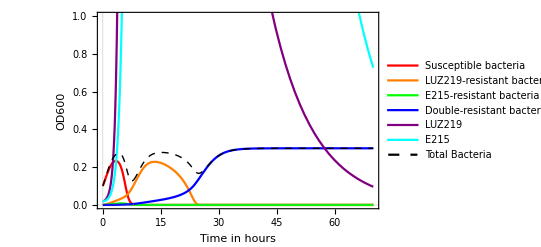

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f1_,f2_,u1_,u2_,m_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1/(1+b1*m*Bb+b1*Bb/s1)*Bb*Pa,-s2*Bib+b2*B*Pb+b2/(1+b2*m*Ba+b2*Ba/s2)*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2/(1+b2*m*Ba+b2*Ba/s2)*Ba*Pb+u1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1/(1+b1*m*Bb+b1*Bb/s1)*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-b1/(1+b1*m*Bb+b1*Bb/s1)*Bb*Pa,-0.09*Pb+h*s2*Bib-b2/(1+b2*m*Ba+b2*Ba/s2)*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.027,s1->2.98,b1->0.09,a2->0.008,s2-> 1.05,b2->0.09,h->100,f1->0,f2->0,u1->0,u2->1,m->350};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.4,0.3,0.1][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
GSiSol=Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.4,0.3,0.1][t]]],{t,0,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"Susceptible bacteria","LUZ219-resistant bacteria","E215-resistant bacteria","Double-resistant bacteria","LUZ219","E215","Total Bacteria"},LegendFunction->Framed],{0.5,0.65}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.3,0.4][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,1}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

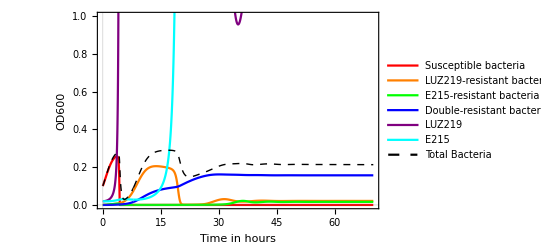

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f1_,f2_,u1_,u2_,m_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-f1*b1*B*Pa^m-f2*b2*B*Pb^m-a1*B-a2*B-a3*B,-s1*Bia+f1*b1*B*Pa^m+f1*b1*Bb*Pa^m,-s2*Bib+f2*b2*B*Pb^m+f2*b2*Ba*Pb^m,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-f2*b2*Ba*Pb^m+u1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f1*b1*Bb*Pa^m+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f1/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f2/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 1.05,b2->277,h->100,f1->1/400,f2->1/1000,u1->20,u2->10,m->1.8};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.4,0.3,0.1][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
GSiSol=Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.4,0.3,0.1][t]]],{t,0,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"Susceptible bacteria","LUZ219-resistant bacteria","E215-resistant bacteria","Double-resistant bacteria","LUZ219","E215","Total Bacteria"},LegendFunction->Framed],{0.5,0.65}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.3,0.4][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,1}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

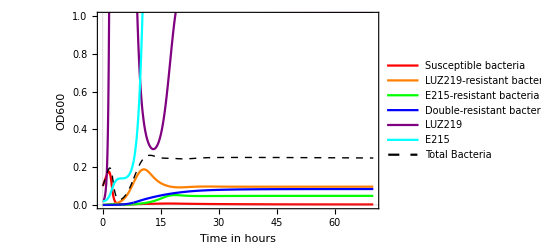

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f1_,f2_,u1_,u2_,m_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-f1*b1*B^m*Pa-f2*b2*B^m*Pb-a1*B-a2*B-a3*B,-s1*Bia+f1*b1*B^m*Pa+f1*b1*Bb^m*Pa,-s2*Bib+f2*b2*B^m*Pb+f2*b2*Ba^m*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-f2*b2*Ba^m*Pb+u1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f1*b1*Bb^m*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f1/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f2/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 1.05,b2->277,h->100,f1->1/400,f2->1/1500,u1->20,u2->5,m->1.3};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0/5,B0/5,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.4,0.3,0.1][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f1,f2,u1,u2,m]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
GSiSol=Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.4,0.3,0.1][t]]],{t,0,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"Susceptible bacteria","LUZ219-resistant bacteria","E215-resistant bacteria","Double-resistant bacteria","LUZ219","E215","Total Bacteria"},LegendFunction->Framed],{0.5,0.65}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.3,0.4][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,1}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

## Model solution and scenerio

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

```mathematica
Remove[A,B]
```

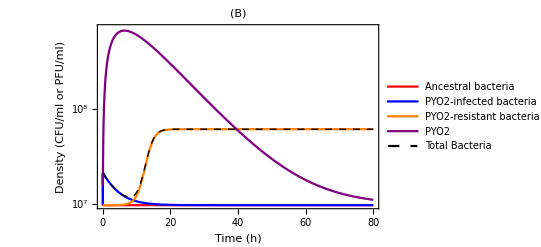

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B+a*Br,-0.25*Bi+460*B*P,0.005*B+0.8*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.25*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B-0.25*Bi+460*B*P+0.005*B+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Ancestral bacteria","PYO2-infected bacteria","PYO2-resistant bacteria","PYO2","Total Bacteria"}],{0.74,0.73}],PlotTheme->"Detailed",FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Orange},{Purple},{Black,Dashed,Thick}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

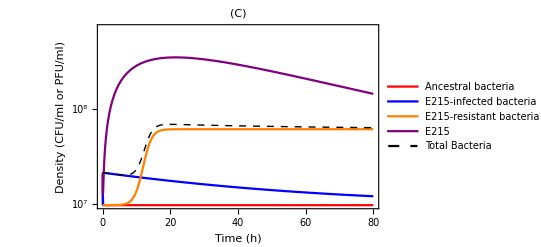

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B+a*Br,-0.02*Bi+460*B*P,0.005*B+0.81*Br*(1-(B+Br)/k)-a*Br,-0.09*P+200*0.02*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B-0.02*Bi+460*B*P+0.005*B+0.81*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Ancestral bacteria","E215-infected bacteria","E215-resistant bacteria","E215","Total Bacteria"}],{0.73,0.4}],PlotTheme->"Detailed",FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Orange},{Purple},{Black,Dashed,Thick}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(C)"]
```

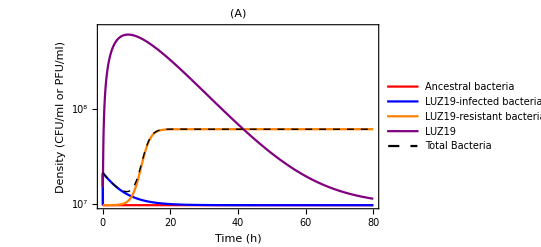

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.017*B+a*Br,-0.19*Bi+460*B*P,0.017*B+0.77*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.19*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.017*B-0.19*Bi+460*B*P+0.017*B+0.77*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Ancestral bacteria","LUZ19-infected bacteria","LUZ19-resistant bacteria","LUZ19","Total Bacteria"}],{0.74,0.75}],PlotTheme->"Detailed",FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Orange},{Purple},{Black,Dashed,Thick}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(A)"]
```

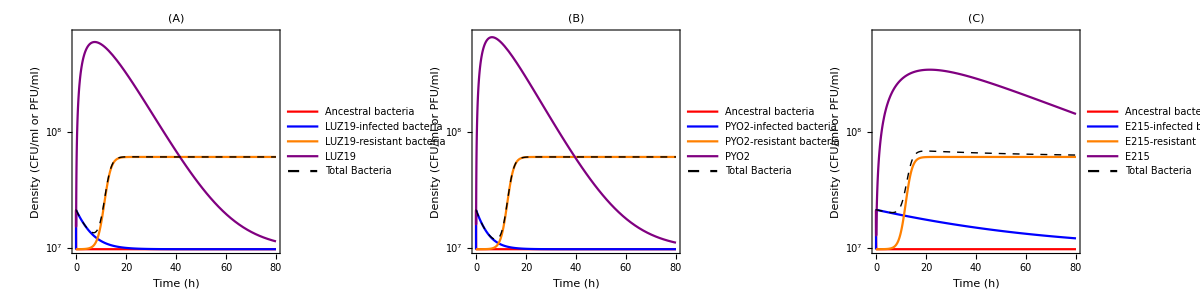

```mathematica
Solve[0.877*B*(1-(B+Br)/0.9)-0.008*B+0.008*Br==0&&0.008*B+0.8*Br*(1-(B+Br)/0.9)-0.008*Br==0,{B,Br}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{B→-9.17185,Br→10.0546},{B→0.,Br→0.},{B→0.45,Br→0.45}}

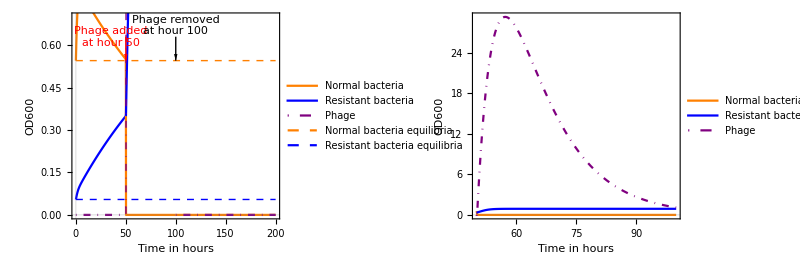

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.008*B+a*Br,-0.21*Bi+460*B*P,0.008*B+0.8*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.21*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.008*B-0.21*Bi+277*B*P+0.008*B+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
initialEquilibrium=ParametricNDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])},X[0]=={0.5454545454545454,0,0.05454545454545454,0,0.6}},{B[t],Bi[t],Br[t],P[t],Bt[t]},{t,0,50},{k,a}];
bacteriaEquil=(initialEquilibrium[k,a]/.parameterValues)[[1]];
RbacteriaEquil=(initialEquilibrium[k,a]/.parameterValues)[[3]];
PhageEquil=(initialEquilibrium[k,a]/.parameterValues)[[4]];
stateAtHour50=(initialEquilibrium[k,a]/.parameterValues)/.t->50;
stateAtHour50[[4]]=0.03;
longterm2=ParametricNDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])},X[50]==stateAtHour50},{B[t],Bi[t],Br[t],P[t],Bt[t]},{t,50,100},{k,a}];
bacteria=(longterm2[k,a]/.parameterValues)[[1]];
Rbacteria=(longterm2[k,a]/.parameterValues)[[3]];
Phage=(longterm2[k,a]/.parameterValues)[[4]];
stateAtHour100=(longterm2[k,a]/.parameterValues)/.t->100;
stateAtHour100[[4]]=0;
stateAtHour100[[2]]=0;
removePhage=ParametricNDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])},X[100]==stateAtHour100},{B[t],Bi[t],Br[t],P[t],Bt[t]},{t,100,200},{k,a}];
bacteriaAfterRemovePhage=(removePhage[k,a]/.parameterValues)[[1]];
RbacteriaAfterRemovePhage=(removePhage[k,a]/.parameterValues)[[3]];
PhageAfterRemovePhage=(removePhage[k,a]/.parameterValues)[[4]];
GraphicsGrid[{{Show[Plot[{bacteriaEquil,RbacteriaEquil,PhageEquil},{t,0,50},PlotRange->All,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Normal bacteria","Resistant bacteria","Phage"},LegendFunction->Framed],{0.83,0.57}],BaseStyle->{9,Bold},PlotStyle->{Orange,Blue,{Purple,DotDashed}},FrameLabel->{"Time in hours","OD600"}],Plot[{bacteria,Rbacteria,Phage},{t,50,100},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Orange,Blue,{Purple,Thick,DotDashed}}],Plot[{bacteriaAfterRemovePhage,RbacteriaAfterRemovePhage,PhageAfterRemovePhage},{t,100,200},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Orange,Blue,{Purple,DotDashed}}],Plot[{0.5454545454545454,0.05454545454545454},{x,0,200},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{{Orange,Dashed,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"Normal bacteria\nequilibria","Resistant bacteria\nequilibria"},LegendFunction->Framed],{0.83,0.3}]],Graphics[{Thick,Red,Arrow[{{50,0.63},{50,0.5454545454545454}}]}],Graphics[{Thick,Black,Arrow[{{100,0.63},{100,0.5454545454545454}}]}],Graphics[{Red,Text["Phage added\nat hour 50",{35,0.63}]}],Graphics[{Black,Text["Phage removed\nat hour 100",{100,0.67}]}],PlotRange->{{0,200},{0,0.7}},PlotTheme->"Scientific"],Plot[{bacteria,Rbacteria,Phage},{t,50,100},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Orange,Blue,{Purple,DotDashed}},BaseStyle->{9,Bold},PlotLegends->Placed[LineLegend[{"Normal bacteria","Resistant bacteria","Phage"},LegendFunction->Framed],{0.8,0.6}],FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Spacings->1]
```

```mathematica
stateAtHour50
```

{0.545455,0.,0.0545455,0.03,0.6}

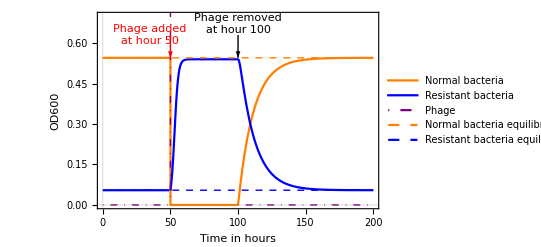

```mathematica
Show[Plot[{bacteriaEquil,RbacteriaEquil,PhageEquil},{t,0,50},PlotRange->All,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Normal bacteria","Resistant bacteria","Phage"},LegendFunction->Framed],{0.83,0.57}],BaseStyle->{16,Bold},PlotStyle->{Orange,Blue,{Purple,Thick,DotDashed}},FrameLabel->{"Time in hours","OD600"}],Plot[{bacteria,Rbacteria,Phage},{t,50,100},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Orange,Blue,{Purple,Thick,DotDashed}}],Plot[{bacteriaAfterRemovePhage,RbacteriaAfterRemovePhage,PhageAfterRemovePhage},{t,100,200},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Orange,Blue,{Purple,Thick,DotDashed}}],Plot[{0.5454545454545454,0.05454545454545454},{x,0,200},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{{Orange,Dashed,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"Normal bacteria\nequilibria","Resistant bacteria\nequilibria"},LegendFunction->Framed],{0.83,0.3}]],Graphics[{Thick,Red,Arrow[{{50,0.63},{50,0.5454545454545454}}]}],Graphics[{Thick,Black,Arrow[{{100,0.63},{100,0.5454545454545454}}]}],Graphics[{Red,Text["Phage added\nat hour 50",{35,0.63}]}],Graphics[{Black,Text["Phage removed\nat hour 100",{100,0.67}]}],PlotRange->{{0,200},{0,0.7}},PlotTheme->"Scientific",ImageSize->Full]
```

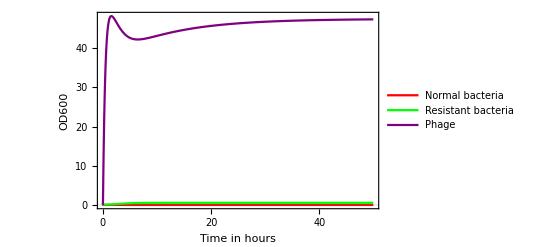

```mathematica
Plot[{bacteria,Rbacteria,Phage},{t,50,100},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Red,Green,Purple},BaseStyle->{9,Bold},PlotLegends->Placed[LineLegend[{"Normal bacteria","Resistant bacteria","Phage"},LegendFunction->Framed],{0.5,0.6}],ImageSize->Full,FrameLabel->{"Time in hours","OD600"},FrameStyle->{Bold,Black},FrameTicks->{{Table[x,{x,0,50,10}],None},{Table[{x,x-50},{x,50,100,10}],None}}]
```

```mathematica
0.5454545454545454/0.6
```

0.909091

```mathematica
longterm2[k,a]/.parameterValues/.t->80
```

{3.33301×10^-6,0.0187826,0.539997,46.7915,0.558783}

```mathematica
0.5399966924277095/(0.018782611221194588+0.5399966924277095)
```

0.966386

```mathematica
longterm2[k,a]/.parameterValues/.t->91
```

{3.30072×10^-6,0.0187826,0.539997,47.2493,0.558783}

```mathematica
longterm2[k,a]/.parameterValues/.t->92
```

{3.29909×10^-6,0.0187826,0.539997,47.2726,0.558783}

```mathematica
longterm2[k,a]/.parameterValues/.t->93
```

{3.29761×10^-6,0.0187826,0.539997,47.2939,0.558783}

```mathematica
longterm2[k,a]/.parameterValues/.t->94
```

{3.29625×10^-6,0.0187826,0.539997,47.3134,0.558783}

#### Equilibrium analysis

```mathematica
PH3[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-277*B*P-0.008*B+a*Br,-2.98*Bi+277*B*P,0.008*B+0.77*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*2.98*Bi-277*B*P};
```

```mathematica
Remove[B,Br]
Solve[{0.8772547720626924*B*(1-(B+Br)/0.6)-0.008*B+0.08*Br==0,0.008*B+0.77*Br*(1-(B+Br)/0.6)-0.08*Br==0},{B,Br}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{B→-3.82069,Br→4.35288},{B→0.,Br→0.},{B→0.545455,Br→0.0545455}}

```mathematica
PH3[0.6,0.08]/.{{B->0.5454545454545454,Br->0.05454545454545454,Bi->0,P->0}}
```

{{0.,0.,0.,0.}}

```mathematica
jacobian=Outer[D,{0.8772547720626924*B*(1-(B+Br)/0.6)-0.008*B+0.08*Br,0.008*B+0.77*Br*(1-(B+Br)/0.6)-0.08*Br},{B,Br}]//MatrixForm
```

(-0.008-1.46209 B+0.877255 (1-1.66667 (B+Br)) | 0.08-1.46209 B
0.008-1.28333 Br | -0.08-1.28333 Br+0.77 (1-1.66667 (B+Br)))

```mathematica
(* Sink *)
```

```mathematica
lambdas=Eigenvalues[jacobian[[1]]]/.{B->0.5454545454545454,Br->0.05454545454545454}
```

{-0.867504,-0.088}

```mathematica
0.5454545454545454+0.05454545454545454
```

0.6

```mathematica
FullSimplify[0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))]
```

-1/k 0.877255 (1. B (B+Ba+Bab+Bb-1. k)+0.877738 Ba (B+Ba+Bab+Bb-1. k)+0.911936 Bb (B+Ba+Bab+Bb-1. k)+1.13992 Bab (B+Ba+Bab+Bb-1. k) rab+1.13992 Bia k s1+1.13992 Bib k s2)

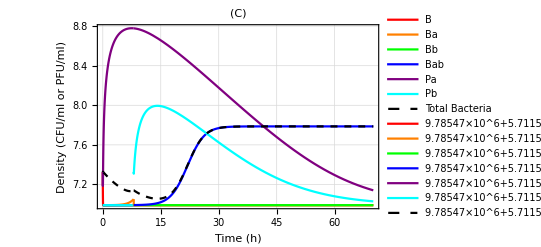

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,18},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol=Show[Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,8},PlotRange->{{0,70},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.7,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ScalingFunctions->"Log10"],Plot[Evaluate[ABMOI1After8h[0.9,0.486]],{t,8,70},PlotRange->{{0,70},{0,7*10^8}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ScalingFunctions->"Log10"],PlotRange->All,ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(C)",ScalingFunctions->"Log10"]
```

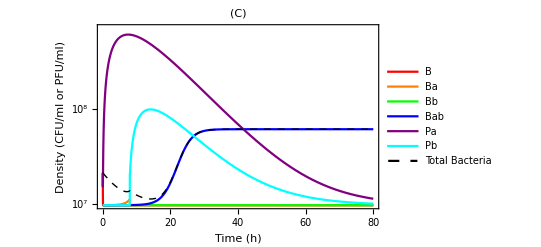

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.747,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(C)",ScalingFunctions->"Log10"]
```

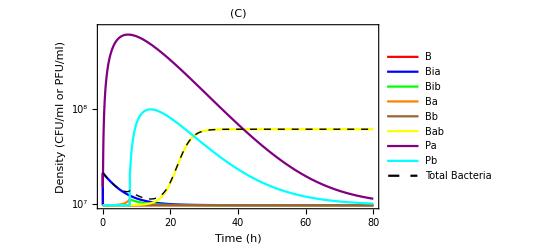

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Bia","Bib","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.67,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Green},{Orange},{Brown},{Yellow},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(C)",ScalingFunctions->"Log10"]
```

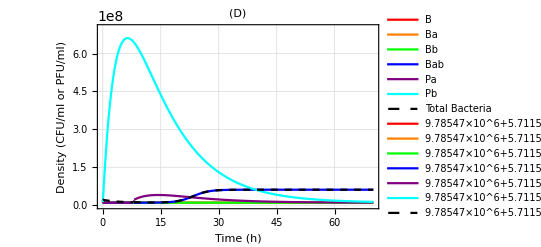

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,18},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.54,0.9,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol2=Show[Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.54,0.9,0.2]],{t,0,8},PlotRange->{{0,70},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.7,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[ABMOI1After8h[0.9,0.486]],{t,8,70},PlotRange->{{0,70},{0,7*10^8}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,7*10^8}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(D)"]
```

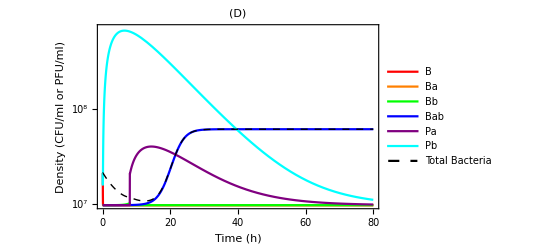

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0},WhenEvent[t==8,Pa[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.54,0.9,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol2=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.54,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.747,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(D)",ScalingFunctions->"Log10"]
```

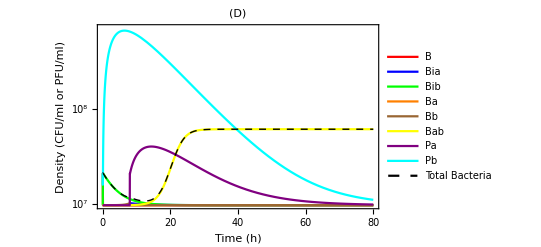

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0},WhenEvent[t==8,Pa[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.54,0.9,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
GseqSol2=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.54,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Bia","Bib","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.65,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Green},{Orange},{Brown},{Yellow},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(D)",ScalingFunctions->"Log10"]
```

```mathematica
Apply[#&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}]
```

{B[t],Ba[t],Bb[t],Bab[t],Pa[t],Pb[t],Bt[t]}

ParametricNDSolveValue::ndsz: At t == 1.07889, step size is effectively zero; singularity or stiff system suspected.

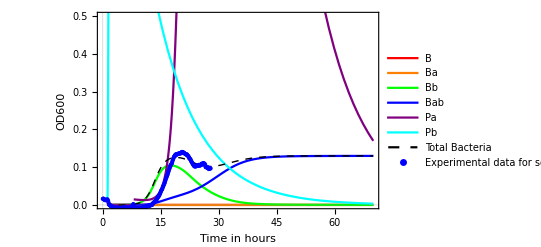

```mathematica
BAData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhage.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
BAMOI01=Transpose[{TIME,BAData[[7,1]]}];
BAMOI1=Transpose[{TIME,BAData[[8,1]]}];
BAMOI10=Transpose[{TIME,BAData[[9,1]]}];
BASEQMOI1INI=Select[BAMOI1,1.2==#[[1]]&][[1,2]];
Remove[DBPH];
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(1+Pa*20)*f*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(1+Pb*20)*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.027,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,h->100,f->1/3000,u1->0,u2->1};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={B0,0,0,0,0,0,0,1*B0,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={B0,0,0,0,0,0,0,1*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.37,0.13,BASEQMOI1INI][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+BASEQMOI1INI*1;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.37,0.13,BASEQMOI1INI][t]]],{t,1.2,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.8,0.6}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.13,0.37][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],ListPlot[BAMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],PlotRange->{{0,70},{0,0.5}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14}]
```

ParametricNDSolveValue::ndsz: At t == 1.50561, step size is effectively zero; singularity or stiff system suspected.

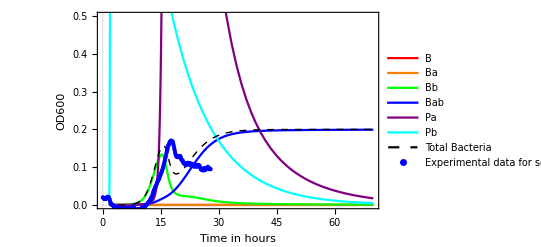

```mathematica
BAData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhage.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
BAMOI01=Transpose[{TIME,BAData[[7,1]]}];
BAMOI1=Transpose[{TIME,BAData[[8,1]]}];
BAMOI10=Transpose[{TIME,BAData[[9,1]]}];
BASEQMOI01INI=Select[BAMOI01,1.6==#[[1]]&][[1,2]];
Remove[DBPH];
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.027,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,h->100,f->1/1000,u1->0,u2->1};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,0,0.1*B0,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,0,0.1*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.37,0.2,BASEQMOI01INI][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+BASEQMOI01INI*0.1;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.37,0.2,BASEQMOI01INI][t]]],{t,1.6,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.8,0.6}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.2,0.37][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],ListPlot[BAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],PlotRange->{{0,70},{0,0.5}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14}]
```

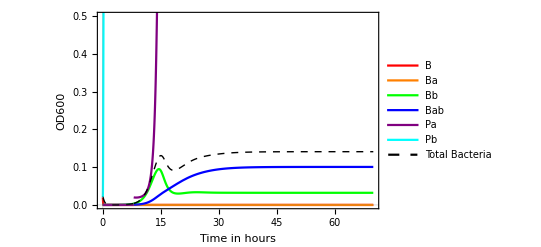

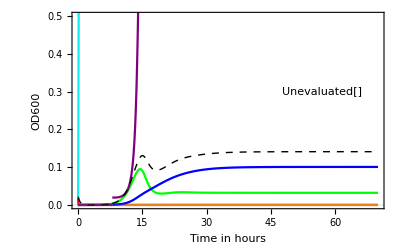

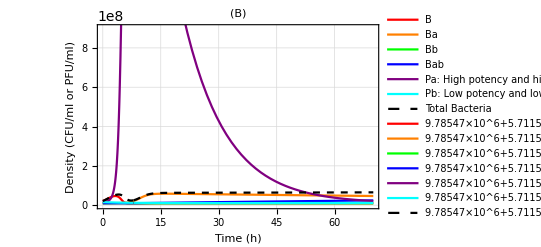

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+1/10*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.005,s1->1,b1->0.1,a2->0.005,s2-> 0.01,b2->0.1,h->60,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,18},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.51,0.9,0.2][8]];
(*ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2*)
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,100},{k,r}];
GseqSol=Show[Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,8},PlotRange->{{0,70},{0,11*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa: High potency and \n high burst size","Pb: Low potency and \nlow burst size","Total Bacteria"}],{0.65,0.7}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[ABMOI1After8h[0.9,0.486]],{t,8,70},PlotRange->{{0,70},{0,11*10^8}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,9*10^8}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)"]
```

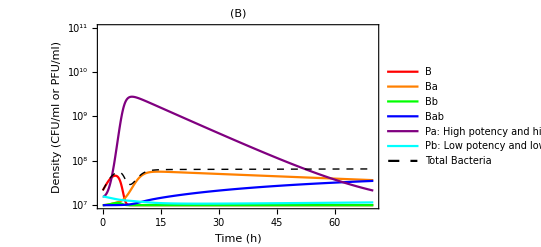

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+1/10*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.01,s1->1,b1->0.1,a2->0.01,s2-> 0.01,b2->0.1,h->60,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.51,0.9,0.2][8]];
(*ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2*)
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,100},{k,r}];
GseqSol=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,70},PlotRange->{{0,70},{0,10^11}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa: High potency and \n high burst size","Pb: Low potency and \nlow burst size","Total Bacteria"}],{0.65,0.7}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)",ScalingFunctions->"Log10"]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\double_sim_2.png",Plot[Evaluate[doublePhageBefore8hMOI1[1.12*10^-5,0.422,0.9,0.2]],
{t,0,70},
PlotRange->{{0,70},{0,10^10}},
AspectRatio->1,
BaseStyle->{Normal,40},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,40},
FrameLabel->{"Time (h)","CFU or PFU/ml"},
PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Purple,Dashed,AbsoluteThickness[5]},{Cyan,Dashed,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{Purple,AbsoluteThickness[5]},{Cyan,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]}},
ImageSize->800,
Frame->{True,True,False,False},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
ScalingFunctions->"Log10"]]
```

C:\Users\zhiyu\Desktop\phage figures\double_sim_2.png

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+1/10*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.005,s1->0.01,b1->0.1,a2->0.005,s2-> 1,b2->0.1,h->60,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,18},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
(*ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2*)
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,100},{k,r}];
GseqSol=Show[Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,8},PlotRange->{{0,70},{0,9*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa: Low potency and \n high burst size","Pb: High potency and \nlow burst size","Total Bacteria"}],{0.35,0.7}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[ABMOI1After8h[0.9,0.486]],{t,8,70},PlotRange->{{0,70},{0,9*10^8}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,9*10^8}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(A)"]
```

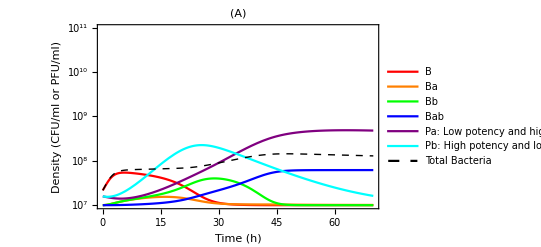

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+1/10*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.01,s1->0.01,b1->0.1,a2->0.01,s2-> 1,b2->0.1,h->60,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
(*ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2*)
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,100},{k,r}];
GseqSol=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,70},PlotRange->{{0,70},{0,10^11}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa: Low potency and \n high burst size","Pb: High potency and \nlow burst size","Total Bacteria"}],{0.35,0.7}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(A)",ScalingFunctions->"Log10"]
```

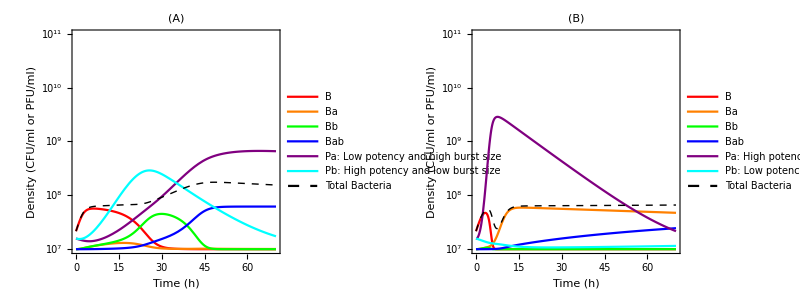

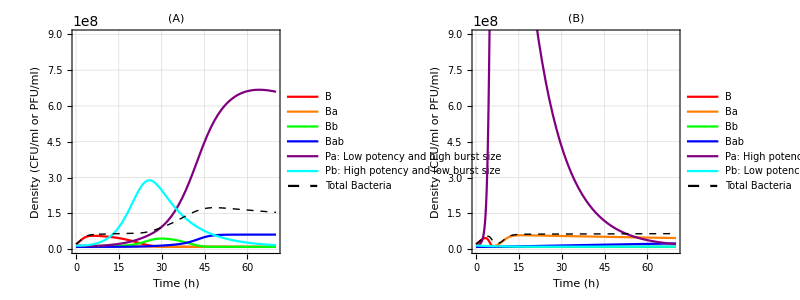

```mathematica
{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}}
```

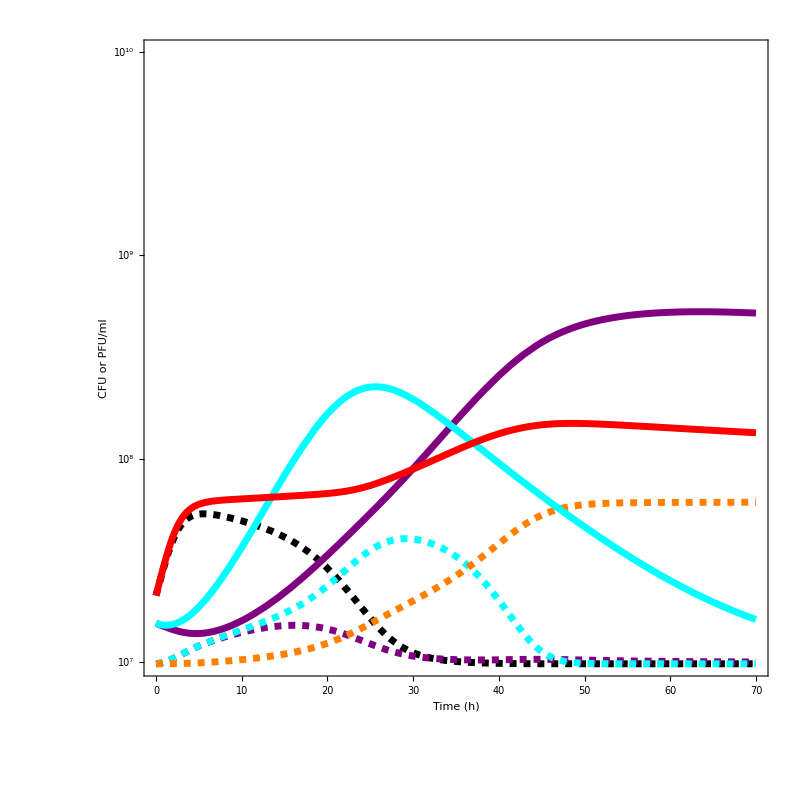

```mathematica
Plot[Evaluate[doublePhageBefore8hMOI1[1.12*10^-5,0.422,0.9,0.2]],{t,0,70},PlotRange->{{0,70},{0,10^10}},
AspectRatio->1,
BaseStyle->{Normal,40},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,40},
FrameLabel->{"Time (h)","CFU or PFU/ml"},
PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Purple,Dashed,AbsoluteThickness[5]},{Cyan,Dashed,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{Purple,AbsoluteThickness[5]},{Cyan,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]}},
ImageSize->800,
Frame->{True,True,False,False},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
ScalingFunctions->"Log10"]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\double_sim_1.png",Plot[Evaluate[doublePhageBefore8hMOI1[1.12*10^-5,0.422,0.9,0.2]],{t,0,70},PlotRange->{{0,70},{0,10^10}},
AspectRatio->1,
BaseStyle->{Normal,40},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,40},
FrameLabel->{"Time (h)","CFU or PFU/ml"},
PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Purple,Dashed,AbsoluteThickness[5]},{Cyan,Dashed,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{Purple,AbsoluteThickness[5]},{Cyan,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]}},
ImageSize->800,
Frame->{True,True,False,False},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
ScalingFunctions->"Log10"]]
```

C:\Users\zhiyu\Desktop\phage figures\double_sim_1.png

```mathematica
A=1
B=2
```

1

2

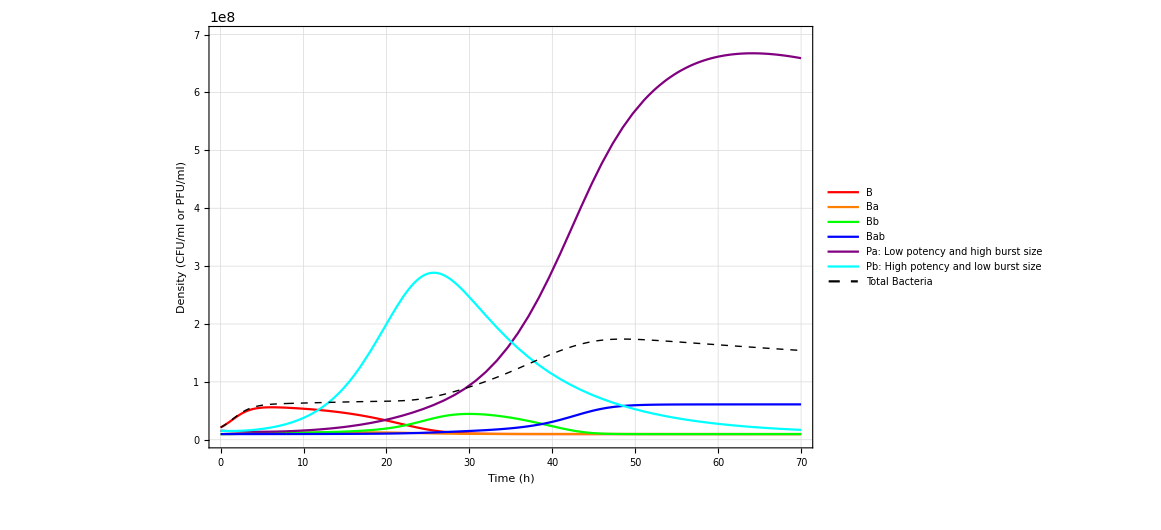
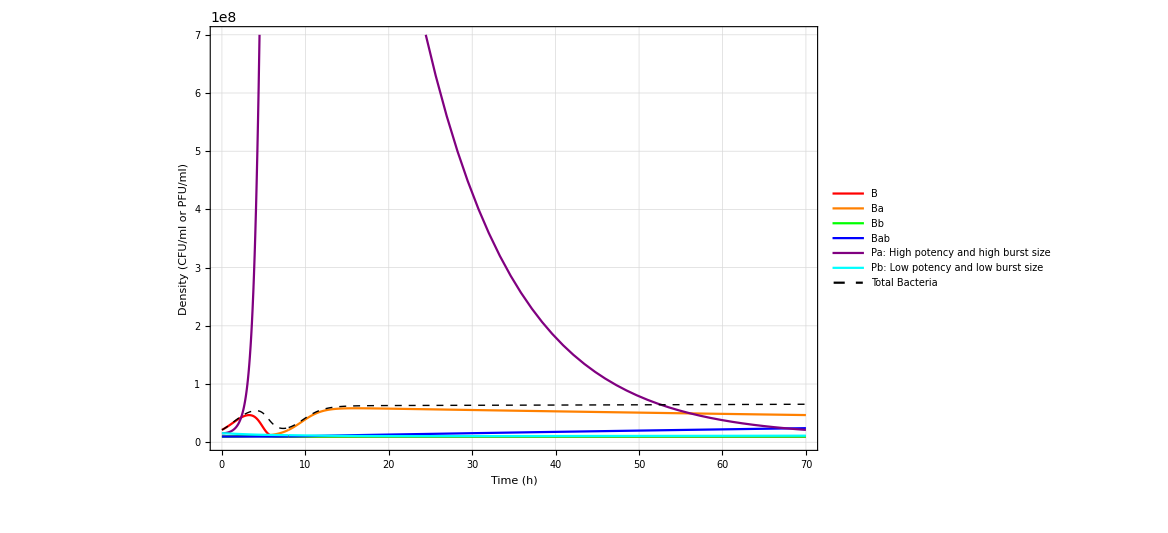
```mathematica
{{{{(A)}, {-Graphics-}}, {{(B)}, {-Graphics-}}}}
```

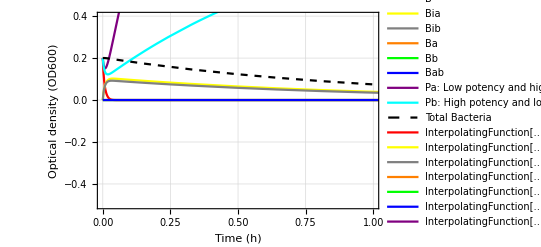

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+10*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.8*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.005,s1->1,b1->460,a2->0.005,s2-> 1,b2->460,h->60,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,B0,B0}},Apply[#&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,18},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.51,0.9,0.2][8]];
(*ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;*)
(*ABMOI1H8[[4]]=0;*)
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[#&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,100},{k,r}];
GseqSol=Show[Plot[Evaluate[doublePhageBefore8hMOI1[4.32*10^-7,0.51,0.9,0.2]],{t,0,8},PlotRange->{{0,70},{-0.5,12}},PlotLegends->Placed[LineLegend[{"B","Bia","Bib","Ba","Bb","Bab","Pa: Low potency and high burst size","Pb: High potency and low burst size","Total Bacteria"}],{0.3,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotStyle->{{Red},{Yellow},{Gray},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[ABMOI1After8h[0.9,0.51]],{t,8,70},PlotRange->{{0,70},{-0.5,12}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Yellow},{Gray},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,1},{-0.5,0.4}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
```

```mathematica
PlotRange->{{0,70},{-0.5,12}}
```

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f1_,f2_,u1_,u2_,m_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-f1*b1*B*Pa^m-f2*b2*B*Pb^m-a1*B-a2*B-a3*B,-s1*Bia+f1*b1*B*Pa^m+f1*b1*Bb*Pa^m,-s2*Bib+f2*b2*B*Pb^m+f2*b2*Ba*Pb^m,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-f2*b2*Ba*Pb^m+u1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f1*b1*Bb*Pa^m+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f1/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f2/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 1.05,b2->277,h->100,f1->1/800,f2->1/1500,u1->20,u2->5,m->1};
```

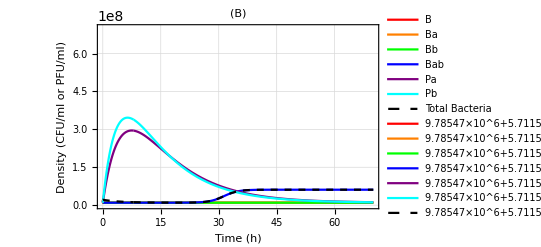

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,rab->0.54,k->0.9,a3->7.2*10^-6};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,8},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
GSiSol=Show[Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,8},PlotRange->{{0,70},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.7,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[ABMOI1After8h[0.54]],{t,8,70},PlotRange->{{0,70},{0,7*10^8}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,7*10^8}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)"]
```

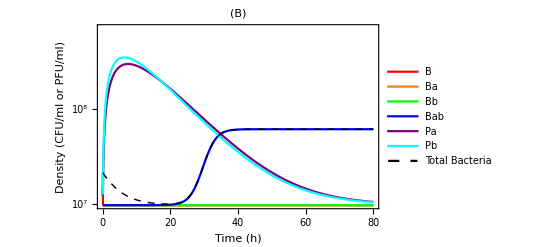

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,rab->0.54,k->0.9,a3->7.2*10^-6};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
GSiSol=Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.747,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)",ScalingFunctions->"Log10"]
```

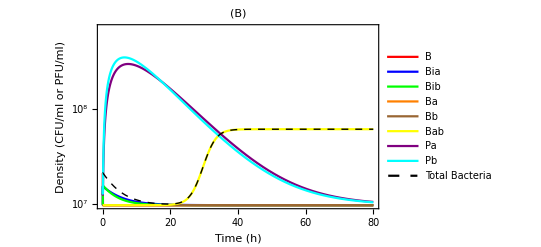

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,rab->0.54,k->0.9,a3->7.2*10^-6};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
GSiSol=Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Bia","Bib","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.65,0.747}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Green},{Orange},{Brown},{Yellow},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)",ScalingFunctions->"Log10"]
```

```mathematica
Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.4,0.2,0.1][8]]
```

{4.3039×10^-10,0.0000912949,0.00336275,0.0180105,0.0000918459,0.00364539,9.68341,0.702588,0.0251812}

```mathematica
4.303902949680204*^-10+0.0000912949034469851+0.0033627531729376217+0.01801048519315768+0.0000918459488806505+0.003645389214604355
```

0.0252018

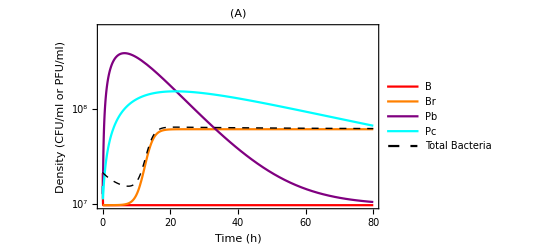

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+0.80*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+0.80*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.005,s1->0.25,b1->460,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
GCoSiSol=Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Br","Pb","Pc","Total Bacteria"}],{0.7,0.63}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Orange},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(A)",ScalingFunctions->"Log10"]
```

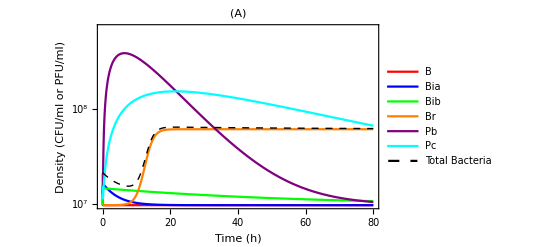

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+0.80*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+0.80*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.005,s1->0.25,b1->460,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
GCoSiSol=Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},PlotLegends->Placed[LineLegend[{"B","Bia","Bib","Br","Pb","Pc","Total Bacteria"}],{0.73,0.7}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Green},{Orange},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(A)",ScalingFunctions->"Log10"]
```

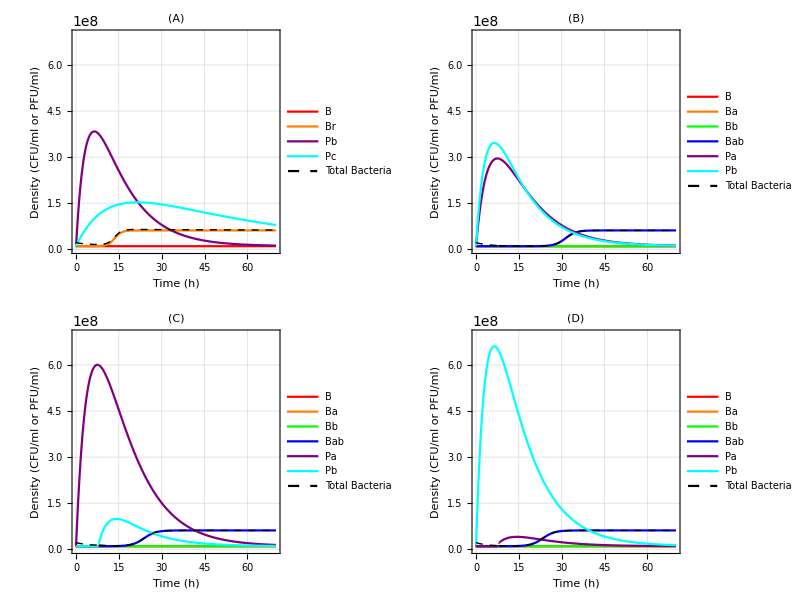

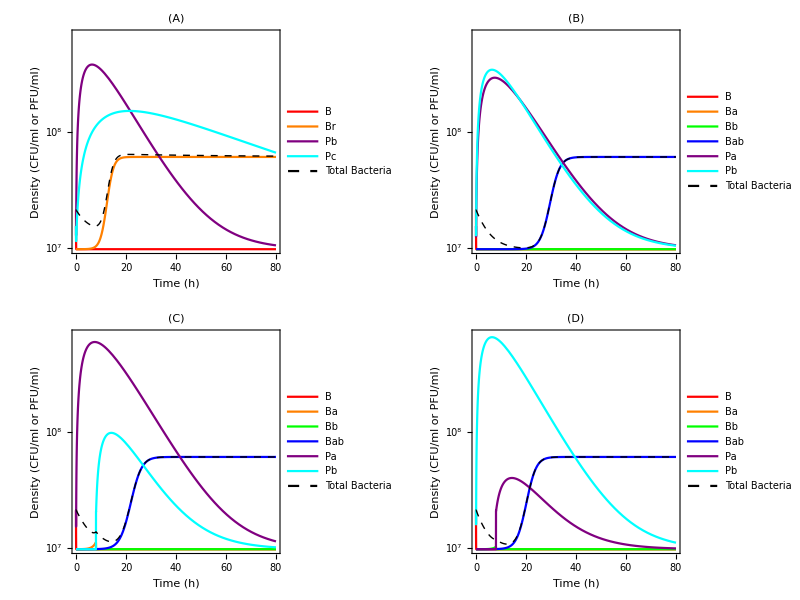

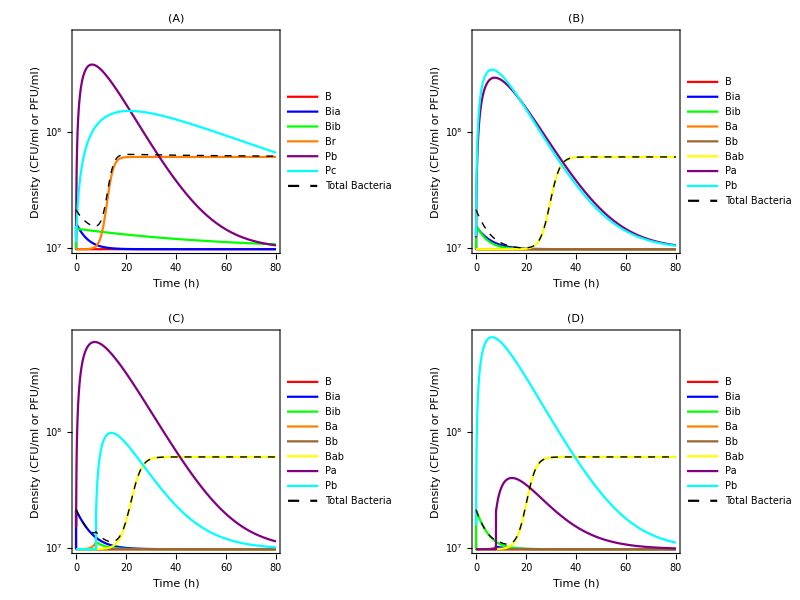

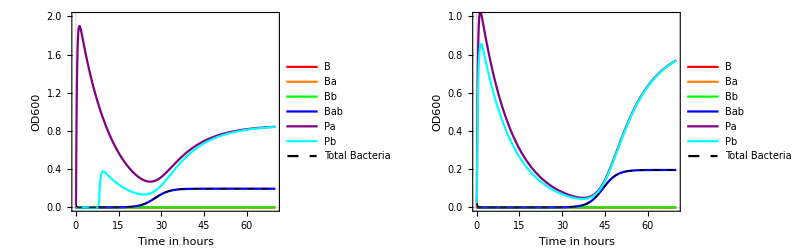

```mathematica
GraphicsGrid[{{GseqSol,GSiSol}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->5]
```

```mathematica
A=1
B=2
```

1

2

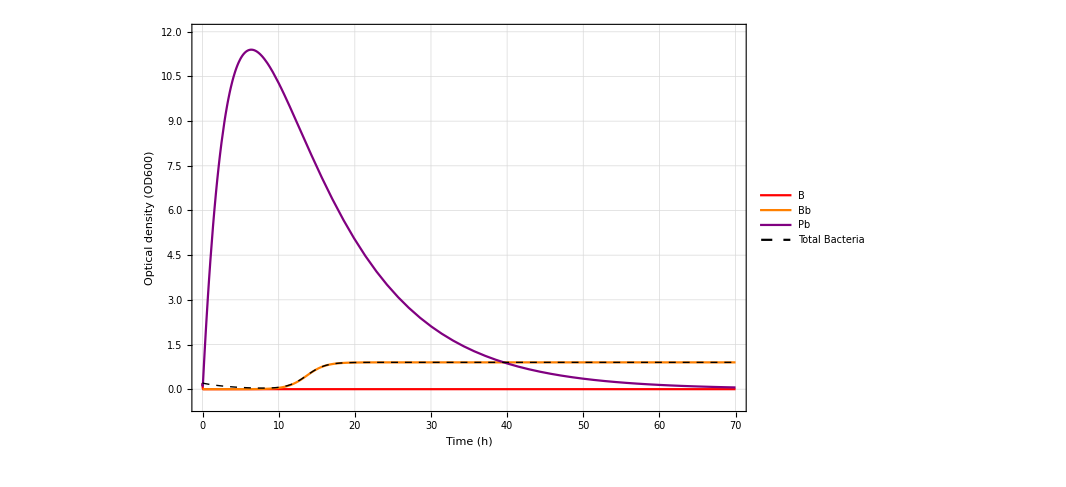
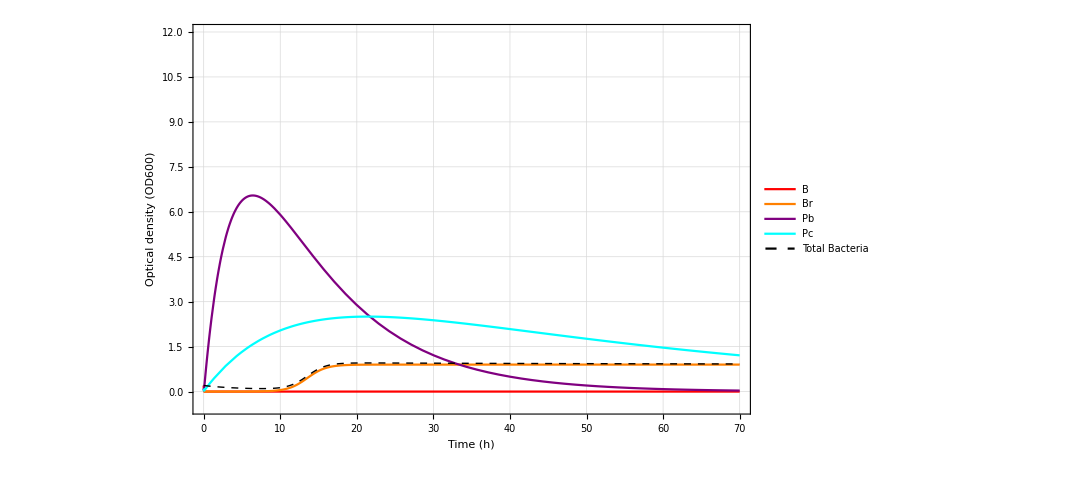
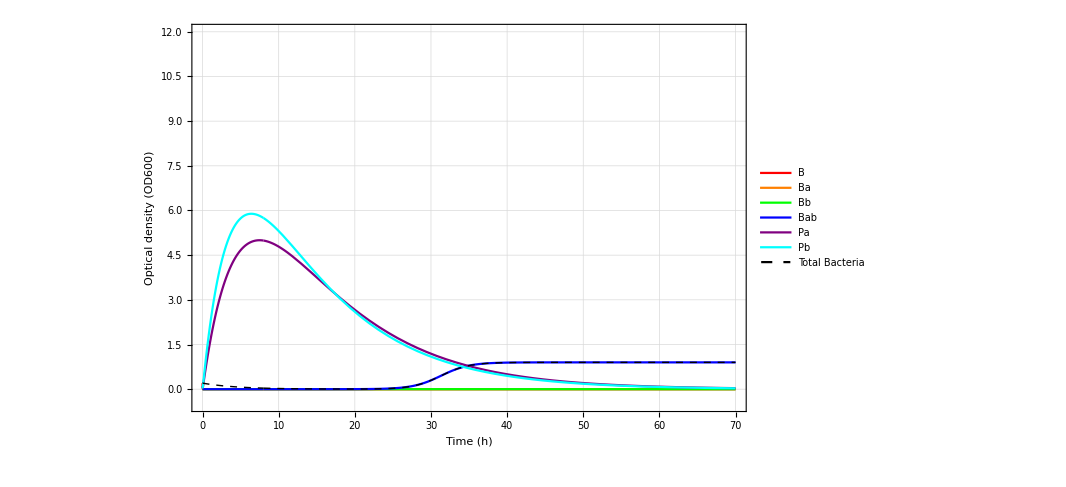
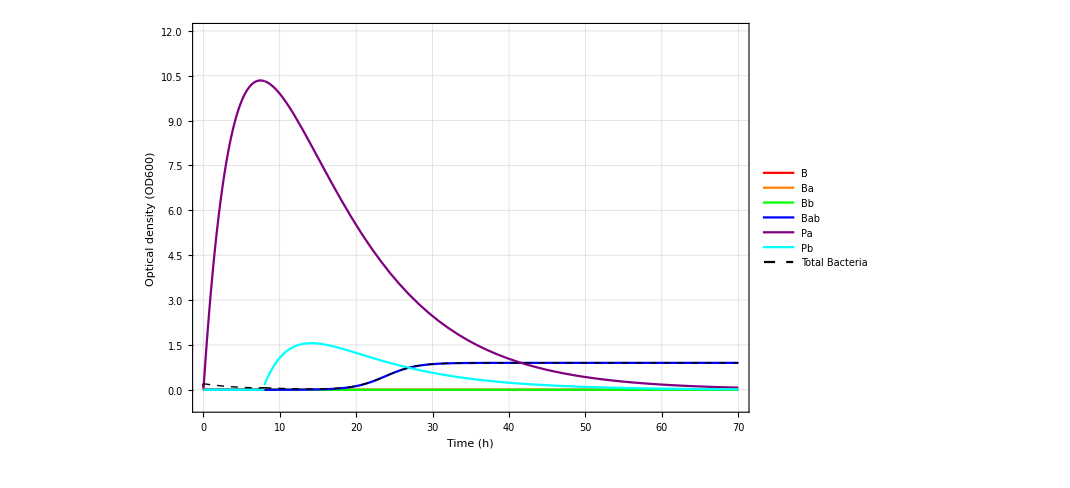
```mathematica
{{(A), (B)}, {-Graphics-, -Graphics-}, {(C), (D)}, {-Graphics-, -Graphics-}}
```

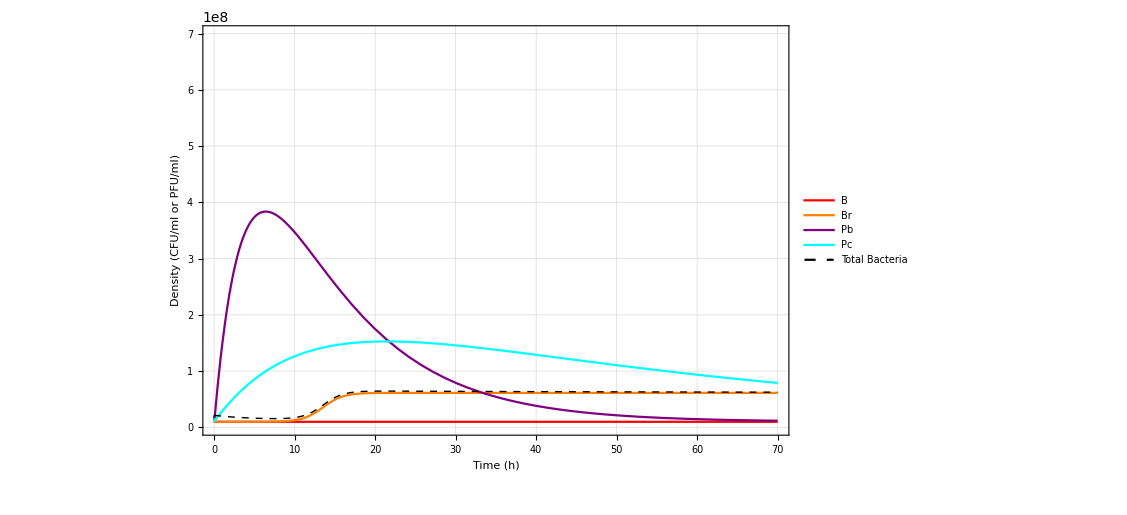
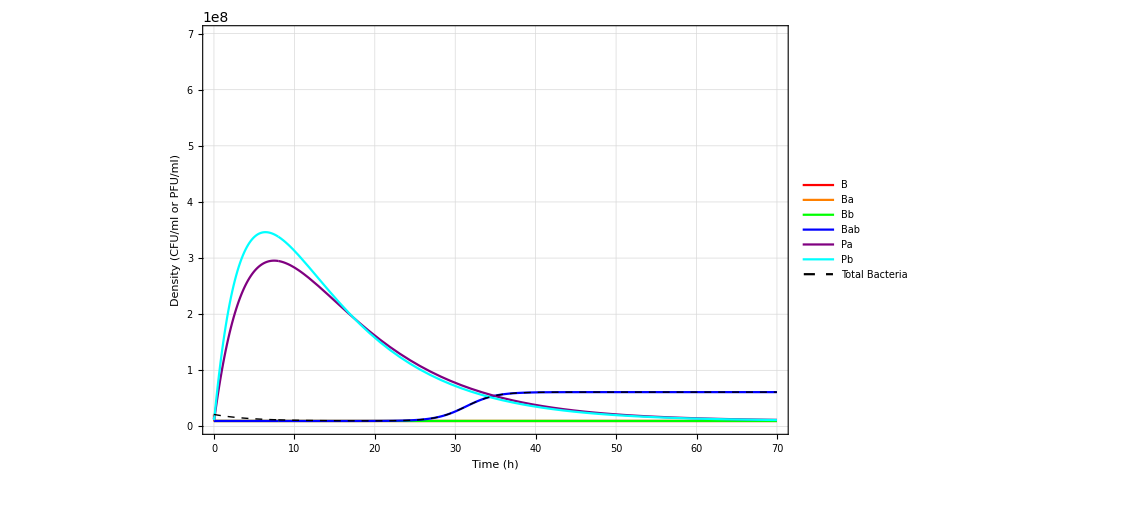
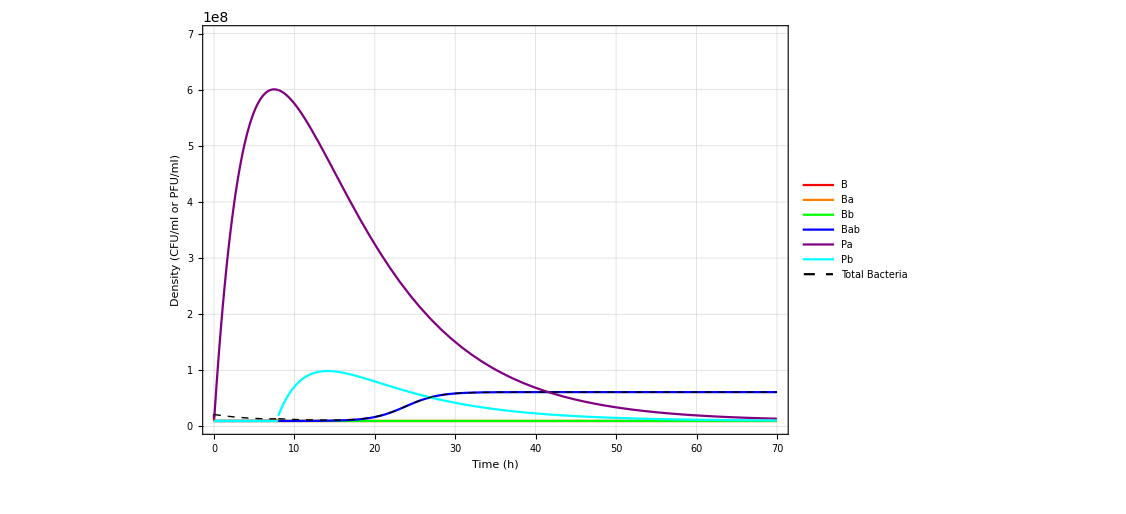
```mathematica
{{(A), (B), (C)}, {-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
A=1
B=1
C=1
```

1

1

Set::wrsym: Symbol C is Protected.

1

ParametricNDSolveValue::ndsz: At t == 0.700296, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 0.700323, step size is effectively zero; singularity or stiff system suspected.

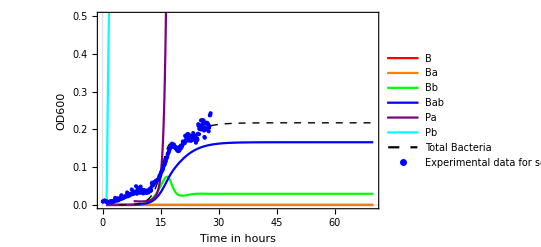

```mathematica
TIME=Table[i,{i,0,27.9,0.1}];
CAData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhage.xlsx"];
CAMOI01=Transpose[{TIME,CAData[[16,1]]}];
CAMOI1=Transpose[{TIME,CAData[[17,1]]}];
CAMOI10=Transpose[{TIME,CAData[[18,1]]}];
CASEQMOI1INI=Select[CAMOI1,0.9==#[[1]]&][[1,2]];
Remove[DBPH];
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 1.05,b2->277,h->100,f->1/700,u1->25,u2->28};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={B0,0,0,0,0,0,0,B0,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ACMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.46,0.3,CASEQMOI1INI][8]];
ACMOI1H8[[7]]=ACMOI1H8[[7]]+CASEQMOI1INI;
ACMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.46,0.28,CASEQMOI1INI][t]]],{t,0.9,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.8,0.65}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ACMOI1After8h[0.3,0.46][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],ListPlot[CAMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseq(E215 → PYO2) MOI1"},LegendFunction->Framed],{0.4,0.6}],PlotStyle->Blue],PlotRange->{{0,70},{0,0.5}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14}]
```

## Model solution final

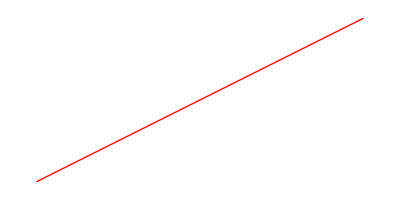

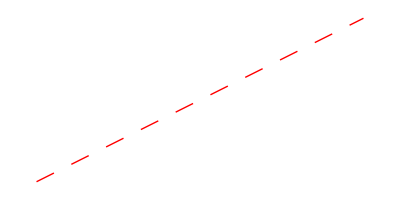

Dashing[Large]

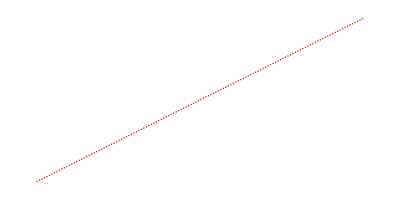

{Dashing[{0.002,0.003}],Thickness[Large]}

-Graphics-

Dashing[None]

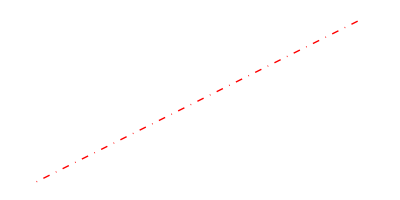

Dashing[{0,Small,Small,Small}]

-Graphics-

Dashing[None]

```mathematica
(* Total *)
Graphics[{Red,Line[{{0,0},{2,1}}]}]
(* Ancestral *)
Graphics[{Dashing[Large],Red,Line[{{0,0},{2,1}}]}]
ansLine=Dashing[Large]
(* Infected *)
Graphics[{Dashing[{0.002,0.003}],Thick,Red,Line[{{0,0},{2,1}}]}]
infLine={Dashing[{0.002,0.003}],Thick}
(* Single mutant *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
smLine=Dashing[None]
(* Double mutant *)
Graphics[{DotDashed,Red,Line[{{0,0},{2,1}}]}]
dmLine=DotDashed
(* Phage *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
pline=Dashing[None]
```

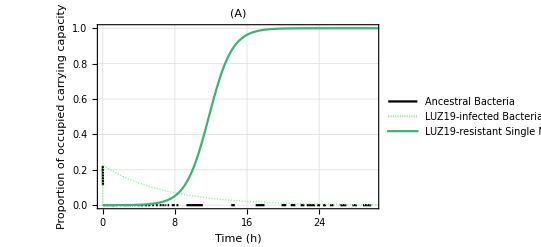

```mathematica
PH2[k_,a_]={basalr*B*(1-(B+Br)/k)-382*B*P-0.025*B+a*Br,-0.147*Bi+382*B*P,0.025*B+0.77*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.147*Bi-382*B*P,basalr*B*(1-(B+Br)/k)-460*B*P-0.025*B-0.147*Bi+382*B*P+0.025*B+luz19r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},{B[t]/0.9,Bi[t]/0.9,Br[t]/0.9},{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,30},{0,1}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},Frame->True,FrameLabel->{"Time (h)","Proportion of occupied carrying capacity"},PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","LUZ19-resistant\nSingle Mutant"}],{0.76,0.6}],PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["mediumseagreen"],smLine}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,PlotLabel->"(A)"]
```

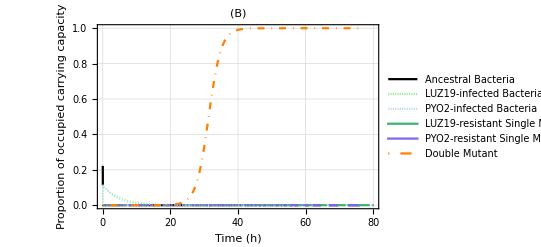

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,rab->0.54,k->0.9,a3->7.2*10^-6};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B[t]/0.9,Bia[t]/0.9,Bib[t]/0.9,Ba[t]/0.9,Bb[t]/0.9,Bab[t]/0.9},{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B[t]/0.9,Bia[t]/0.9,Bib[t]/0.9,Ba[t]/0.9,Bb[t]/0.9,Bab[t]/0.9},{t,8,70},{r}];
Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,80},PlotRange->{{0,80},{0,1}},GridLines->Automatic,BaseStyle->{Bold,25},LabelStyle->{Bold,Black},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameLabel->{"Time (h)","Proportion of occupied carrying capacity"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)",PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","PYO2-infected\nBacteria","LUZ19-resistant\nSingle Mutant","PYO2-resistant\nSingle Mutant","Double Mutant"}],{0.76,0.5}]]
```

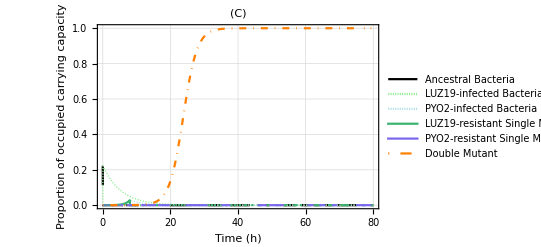

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},{B[t]/0.9,Bia[t]/0.9,Bib[t]/0.9,Ba[t]/0.9,Bb[t]/0.9,Bab[t]/0.9},{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},{B[t]/0.9,Bia[t]/0.9,Bib[t]/0.9,Ba[t]/0.9,Bb[t]/0.9,Bab[t]/0.9},{t,8,70},{k,r}];
Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,1}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Proportion of occupied carrying capacity"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(C)",PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","PYO2-infected\nBacteria","LUZ19-resistant\nSingle Mutant","PYO2-resistant\nSingle Mutant","Double Mutant"}],{0.76,0.5}]]
```

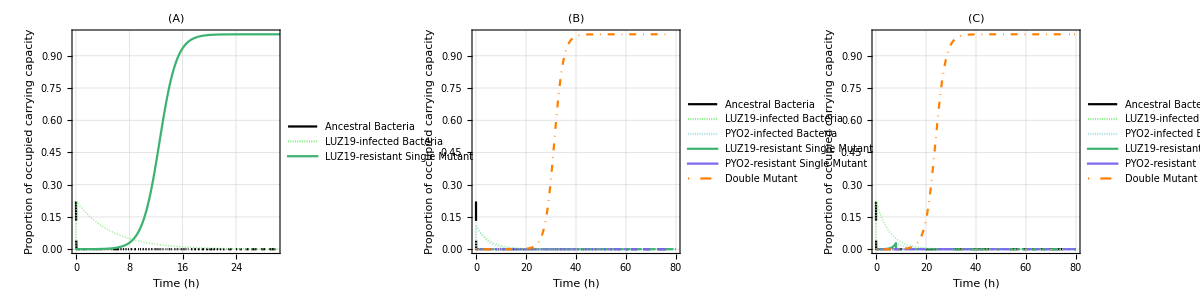

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

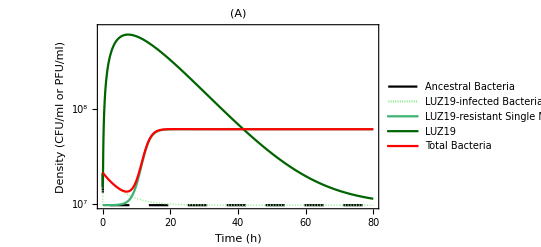

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.017*B+a*Br,-0.19*Bi+460*B*P,0.017*B+0.77*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.19*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.017*B-0.19*Bi+460*B*P+0.017*B+0.77*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
gsinL=Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},Frame->True,FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","LUZ19-resistant\nSingle Mutant","LUZ19","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["darkgreen"],pline},{Red}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(A)"]
```

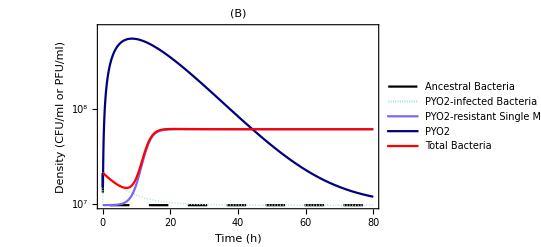

```mathematica
PH2[k_,a_]={basalr*B*(1-(B+Br)/k)-382*B*P-0.025*B+a*Br,-0.147*Bi+382*B*P,0.025*B+luz19r*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.147*Bi-382*B*P,basalr*B*(1-(B+Br)/k)-382*B*P-0.025*B-0.147*Bi+382*B*P+0.025*B+luz19r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
gsinP=Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{Red}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

```mathematica
{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}}
```

```mathematica
PH2[k_,a_]={basalr*B*(1-(B+Br)/k)-382*B*P-0.025*B+a*Br,-0.147*Bi+382*B*P,0.025*B+luz19r*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.147*Bi-382*B*P,basalr*B*(1-(B+Br)/k)-382*B*P-0.025*B-0.147*Bi+382*B*P+0.025*B+luz19r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_luz19.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*10,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_luz19_moi10.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*0.1,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_luz19_moi01.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

PH2[k_,a_]={basalr*B*(1-(B+Br)/k)-382*B*P-0.0119*B+a*Br,-0.178*Bi+382*B*P,0.0119*B+pyo2r*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.178*Bi-382*B*P,basalr*B*(1-(B+Br)/k)-382*B*P-0.0119*B-0.147*Bi+382*B*P+0.0119*B+pyo2r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_pyo2.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*10,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_pyo2_moi10.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*0.1,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_pyo2_moi01.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

PH2[k_,a_]={basalr*B*(1-(B+Br)/k)-382*B*P-0.0119*B+a*Br,-0.0506*Bi+382*B*P,0.0119*B+e215r*Br*(1-(B+Br)/k)-a*Br,-0.09*P+200*0.0506*Bi-382*B*P,basalr*B*(1-(B+Br)/k)-382*B*P-0.0119*B-0.0506*Bi+382*B*P+0.0119*B+e215r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_e215.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*0.1,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_e215_moi01.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]

sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2*10,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sol_single_e215_moi10.png",Plot[Evaluate[sol],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,
Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Blue,Dashed,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800,ScalingFunctions->"Log10"]]
```

C:\Users\zhiyu\Desktop\phage figures\sol_single_luz19.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_luz19_moi10.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_luz19_moi01.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_pyo2.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_pyo2_moi10.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_pyo2_moi01.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_e215.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_e215_moi01.png

C:\Users\zhiyu\Desktop\phage figures\sol_single_e215_moi10.png

```mathematica
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{Red}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

-Graphics-

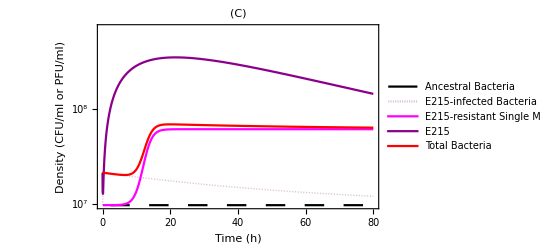

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B+a*Br,-0.02*Bi+460*B*P,0.005*B+0.81*Br*(1-(B+Br)/k)-a*Br,-0.09*P+200*0.02*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B-0.02*Bi+460*B*P+0.005*B+0.81*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
gsinE=Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","E215-infected\nBacteria","E215-resistant\nSingle Mutant","E215","Total Bacteria"}],{0.79,0.6}],PlotStyle->{{Black,ansLine},{RGBColor["thistle"],infLine},{RGBColor["magenta"],smLine},{RGBColor["darkmagenta"],pline},{Red}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(C)"]
```

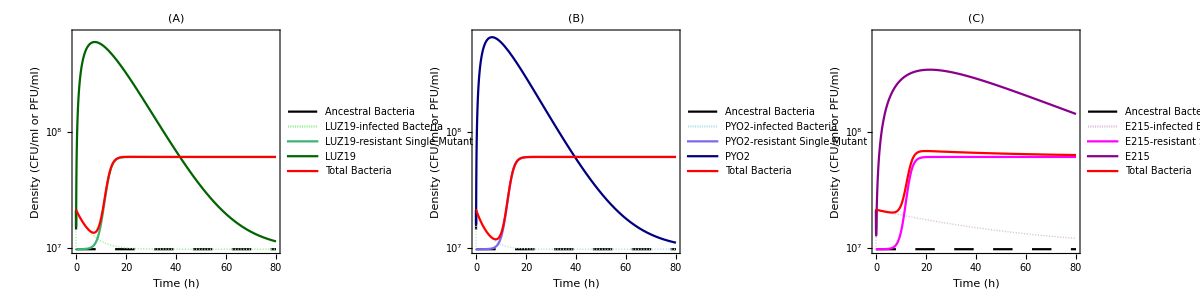

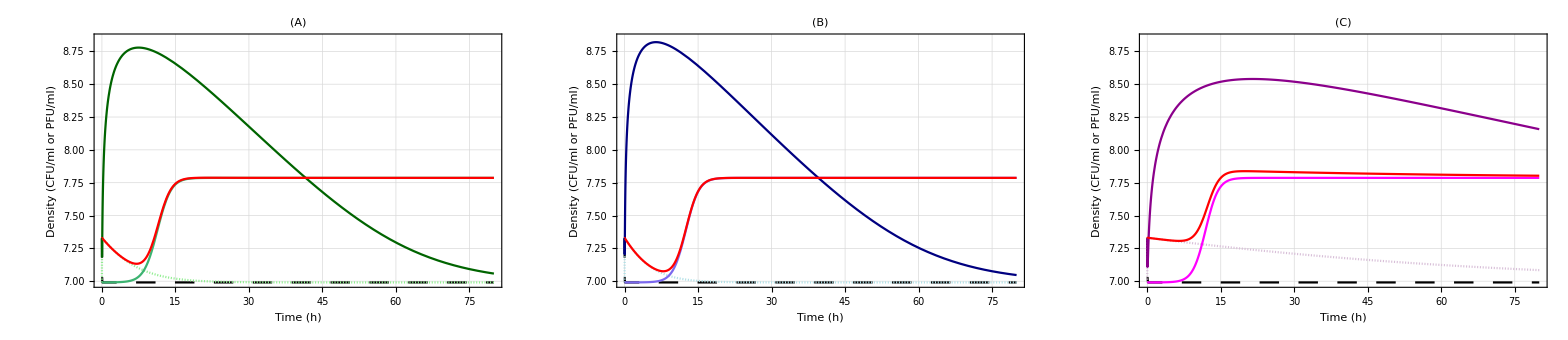

```mathematica
gallsi=Legended[GraphicsGrid[{{gsinL,gsinP,gsinE}},Alignment->Center,Spacings->0,ImageSize->3500],Placed[LineLegend[{ansLine,Directive[infLine,RGBColor["lightgreen"]],Directive[infLine,RGBColor["powderblue"]],Directive[infLine,RGBColor["thistle"]],Directive[smLine,RGBColor["mediumseagreen"]],Directive[smLine,RGBColor["mediumslateblue"]],Directive[smLine,RGBColor["magenta"]],Directive[pline,RGBColor["darkgreen"]],Directive[pline,RGBColor["navy"]],Directive[pline,RGBColor["darkmagenta"]],Red},{Style["Ancestral bacteria",Bold,25],Style["LUZ19-infected Bacteria",Bold,25],Style["PYO2-infected Bacteria",Bold,25],Style["E215-infected Bacteria",Bold,25],Style["LUZ19-resistant Single Mutant",Bold,25],Style["PYO2-resistant Single Mutant",Bold,25],Style["E215-resistant Single Mutant",Bold,25],Style["LUZ19",Bold,25],Style["PYO2",Bold,25],Style["E215",Bold,25],Style["Total Bacteira",Bold,25]},LegendLayout->{"Column",4}],Bottom]]
```

```mathematica
GraphicsGrid[{{gsinL,gsinP,gsinE}},Alignment->Center,Spacings->0,ImageSize->3500]
```

```mathematica
Export["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\Image_final\\ModelSolution_singlephage_CFU_Log_3_phages_infect-reformat.png",gallsi,"PNG",ImageResolution->300]
```

C:\Users\zhiyu\Dropbox\Stan Yu\Phage project\simulation\Image_final\ModelSolution_singlephage_CFU_Log_3_phages_infect-reformat.png

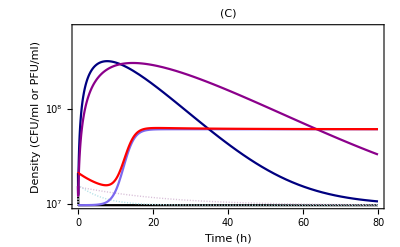

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
gdc=Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},Frame->True,GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black},{RGBColor["powderblue"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{RGBColor["darkmagenta"],pline},{Red}},ImageSize->Full,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(C)",ScalingFunctions->"Log10"]
```

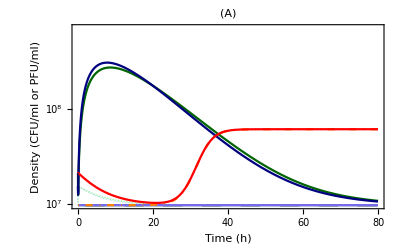

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.178,b2->382,h->100,rab->luz19pyo2r,k->0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
gda=Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,20},LabelStyle->{Bold,Black},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine},{RGBColor["darkgreen"],pline},{RGBColor["navy"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(A)",ScalingFunctions->"Log10"]
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.178,b2->382,h->100,rab->luz19pyo2r,k->0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\luz19_pyo2_sol.png",Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Cyan,infLine,AbsoluteThickness[5]},{RGBColor["darkgreen"],infLine,AbsoluteThickness[5]},{Cyan,Dashed,AbsoluteThickness[5]},{RGBColor["darkgreen"],Dashed,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{Cyan,AbsoluteThickness[5]},{RGBColor["darkgreen"],AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},ImageSize->800,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ScalingFunctions->"Log10"]]

DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,rab->luz19e215r,k->0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\luz19_e215_sol.png",Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{Cyan,infLine,AbsoluteThickness[5]},{Purple,infLine,AbsoluteThickness[5]},{Cyan,Dashed,AbsoluteThickness[5]},{Purple,Dashed,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{Cyan,AbsoluteThickness[5]},{Purple,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},ImageSize->800,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ScalingFunctions->"Log10"]]

DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\pyo2_e215_sol.png",Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],
{t,0,80},
PlotRange->{{0,80},{0,10^9}},
AspectRatio->1,
BaseStyle->{Normal,60},
PlotLegends->None,
GridLines->None,
PlotTheme->"Detailed",
Frame->{True,True,False,False},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,60},
FrameLabel->None,PlotStyle->{{Black,Dashed,AbsoluteThickness[5]},{RGBColor["darkgreen"],infLine,AbsoluteThickness[5]},{Purple,infLine,AbsoluteThickness[5]},{Orange,Dashed,AbsoluteThickness[5]},{RGBColor["darkgreen"],AbsoluteThickness[5]},{Purple,AbsoluteThickness[5]},{Red,AbsoluteThickness[5]}},ImageSize->800,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ScalingFunctions->"Log10"]]
```

C:\Users\zhiyu\Desktop\phage figures\luz19_pyo2_sol.png

C:\Users\zhiyu\Desktop\phage figures\luz19_e215_sol.png

C:\Users\zhiyu\Desktop\phage figures\pyo2_e215_sol.png

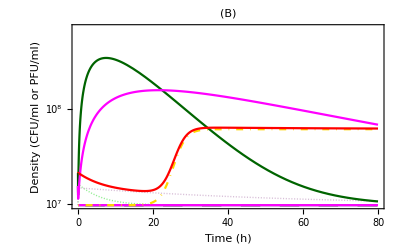

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.02,b2->460,h->100,rab->0.618,k->0.9,a3->7.2*10^-6};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0.5*B0,0.5*B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[0.2][8]];
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{r}];
gdb=Plot[Evaluate[doublePhageBefore8hMOI1[0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["magenta"],smLine},{RGBColor["gold"],dmLine},{RGBColor["darkgreen"],pline},{RGBColor["magenta"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(B)",ScalingFunctions->"Log10"]
```

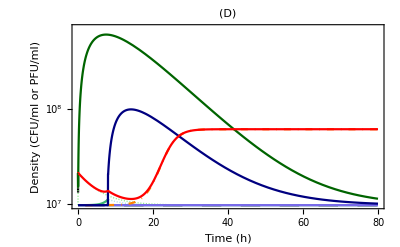

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.486,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
gdd=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.486,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine},{RGBColor["darkgreen"],pline},{RGBColor["navy"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(D)",ScalingFunctions->"Log10"]
```

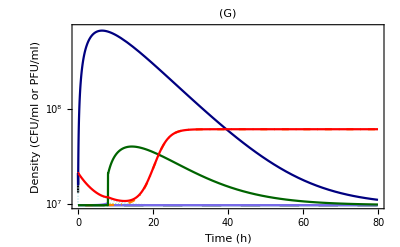

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0},WhenEvent[t==8,Pa[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.54,0.9,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
gdg=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.54,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine},{RGBColor["darkgreen"],pline},{RGBColor["navy"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(G)",ScalingFunctions->"Log10"]
```

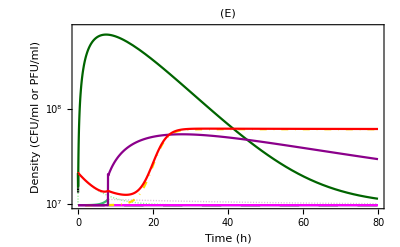

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.02,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,100},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.556,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
gde=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.556,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},Frame->True,GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["magenta"],smLine},{RGBColor["gold"],dmLine},{RGBColor["darkgreen"],pline},{RGBColor["darkmagenta"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(E)",ScalingFunctions->"Log10"]
```

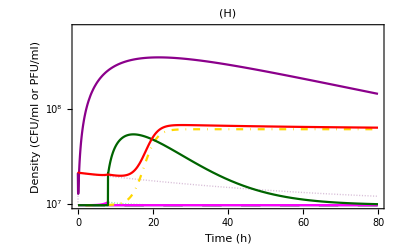

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb+1/2*u3*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa+1/2*u3*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.02,b2->460,h->100,u1->1,u2->1,u3->0};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0},WhenEvent[t==8,Pa[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,20},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[7.2*10^-6,0.618,0.9,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,7.2*10^-6,k,b1,b2,h,r,s1,s2,u1,u2,u3,f]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Apply[CFU[#]&,{{B[t]},{Ba[t]},{Bb[t]},{Bab[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,8,70},{k,r}];
gdh=Plot[Evaluate[doublePhageBefore8hMOI1[7.2*10^-6,0.618,0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},Frame->True,GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["magenta"],smLine},{RGBColor["gold"],dmLine},{RGBColor["darkgreen"],pline},{RGBColor["darkmagenta"],pline},{Red}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(H)",ScalingFunctions->"Log10"]
```

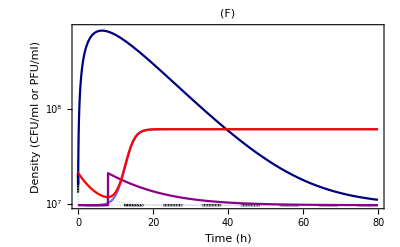

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+0.80*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+0.80*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.005,s1->0.25,b1->460,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0},WhenEvent[t==8,Pb[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
gdf=Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},Frame->True,GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["powderblue"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{RGBColor["darkmagenta"],pline},{Red}},ImageSize->Full,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(F)",ScalingFunctions->"Log10"]
```

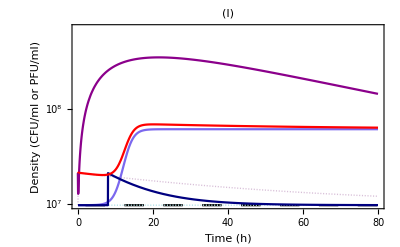

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+0.80*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+0.80*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.005,s1->0.25,b1->460,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0,B0},WhenEvent[t==8,Pa[t]->0.2]},Apply[CFU[#]&,{{B[t]},{Bia[t]},{Bib[t]},{Br[t]},{Pa[t]},{Pb[t]},{Bt[t]}},{1}],{t,0,100},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},{B,Br,Pa,Pb,Bt},{t,0,100},{k,B0}];
gdi=Plot[Evaluate[doublePhageBefore8hMOI1[0.9,0.2]],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},Frame->True,GridLines->Automatic,BaseStyle->{Bold,20},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Black,ansLine},{RGBColor["powderblue"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{RGBColor["darkmagenta"],pline},{Red}},ImageSize->Full,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotLabel->"(I)",ScalingFunctions->"Log10"]
```

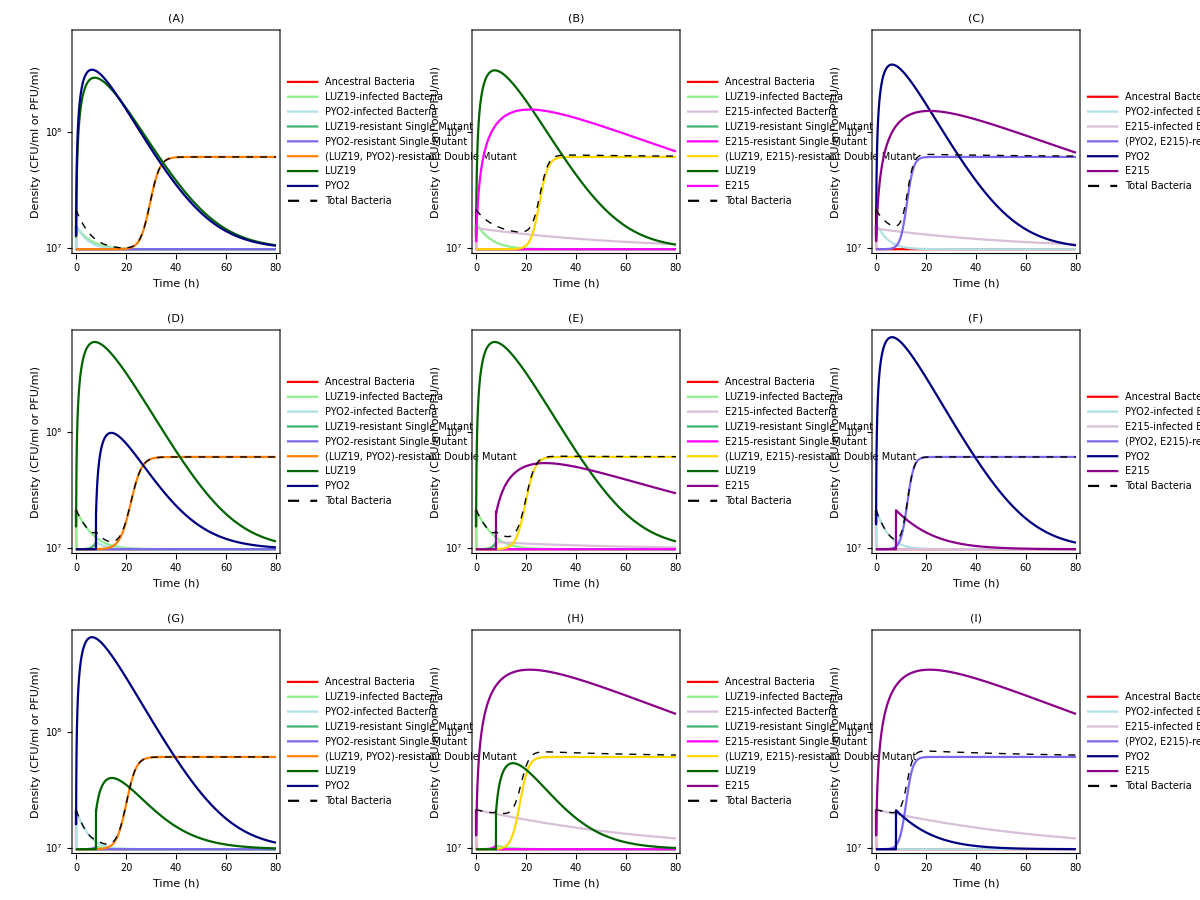

```mathematica
num=GraphicsGrid[{{"(1)"},{"(2)"},{"(3)"}}]
```

-Graphics-

```mathematica
gall=GraphicsGrid[{{sub1,sub2,sub3}},Alignment->Center,Spacings->0,ImageSize->3500]
```

-Graphics-

```mathematica
Export["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\Image_final\\ModelSolution_doublephageWithMOI0.5eachPhageForSimultaneous_CFU_log_infect_all_conditions-reformat.png",gall,"PNG",ImageResolution->300]
```

C:\Users\zhiyu\Dropbox\Stan Yu\Phage project\simulation\Image_final\ModelSolution_doublephageWithMOI0.5eachPhageForSimultaneous_CFU_log_infect_all_conditions-reformat.png

```mathematica
{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine},{RGBColor["darkgreen"],pline},{RGBColor["navy"],pline},{Red}
```

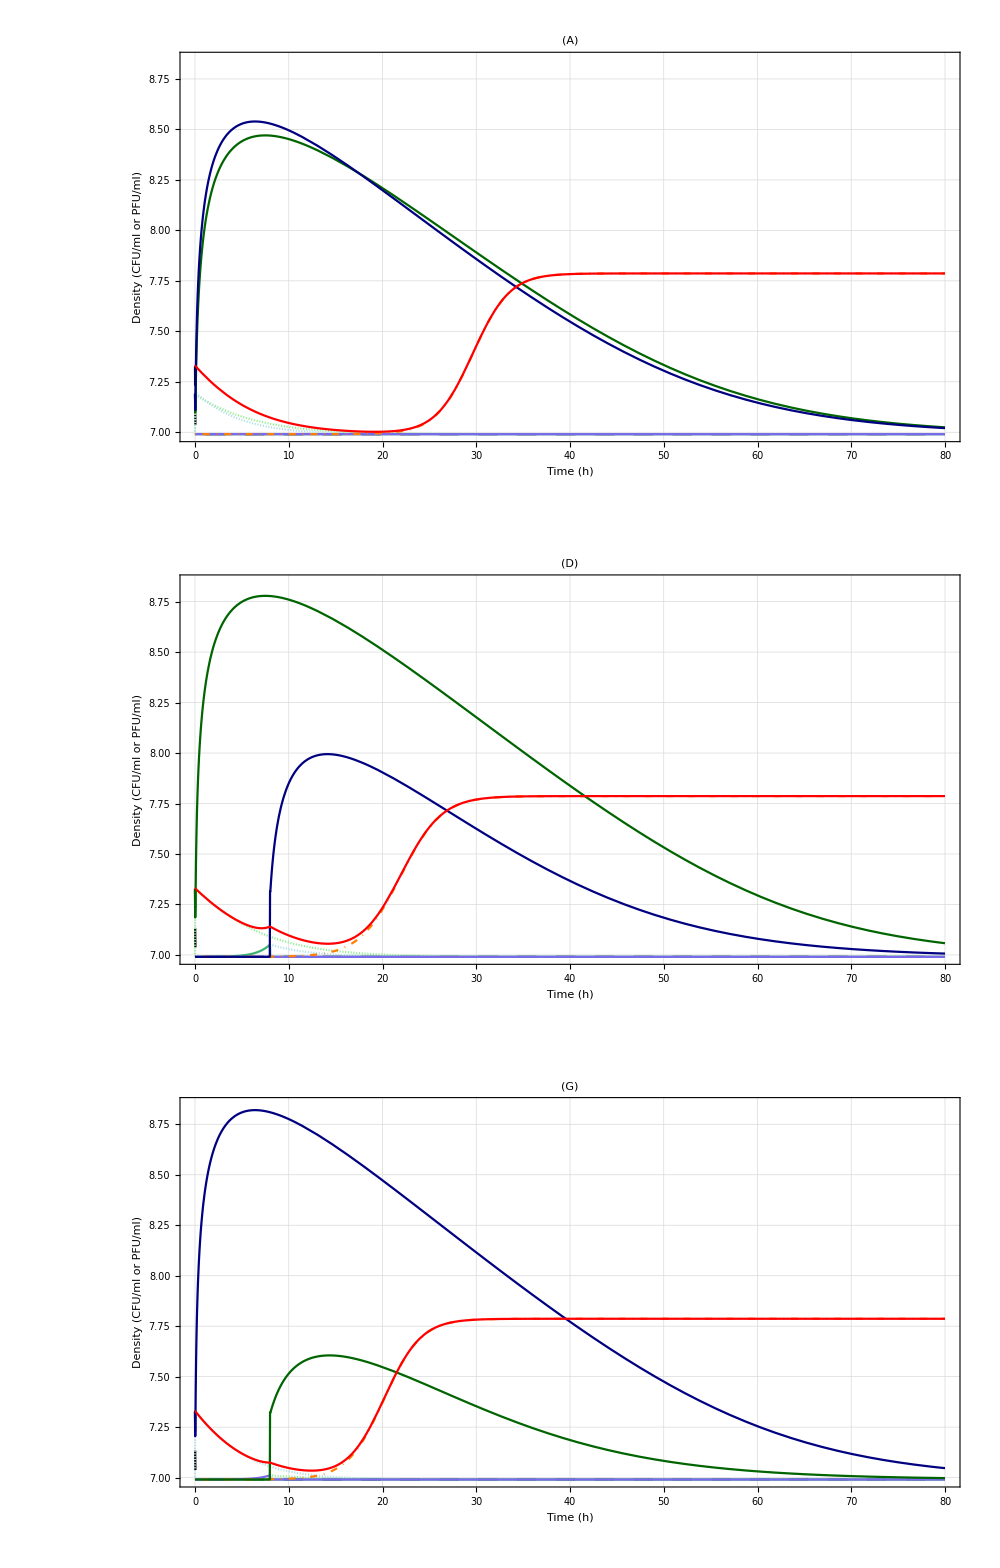

```mathematica
sub1=Legended[GraphicsGrid[{{gda},{gdd},{gdg}},Alignment->Center,Spacings->0,ImageSize->1000],Placed[LineLegend[{Directive[Black,ansLine],{RGBColor["lightgreen"],infLine},{RGBColor["powderblue"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["mediumslateblue"],smLine},{Orange,dmLine},{RGBColor["darkgreen"],pline},{RGBColor["navy"],pline},{Red}},{Style["Ancestral bacteria",Bold,20],Style["LUZ19-infected Bacteria",Bold,20],Style["PYO2-infected Bacteria",Bold,20],Style["LUZ19-resistant Single Mutant",Bold,20],Style["PYO2-resistant Single Mutant",Bold,20],Style["(LUZ19, PYO2)-resistant Double Mutant",Bold,20],Style["LUZ19",Bold,20],Style["PYO2",Bold,20],Style["Total Bacteira",Bold,20]},LegendLayout->{"Column",3}],Bottom]]
```

```mathematica
PlotStyle->{{Black,ansLine},{RGBColor["lightgreen"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["magenta"],smLine},{RGBColor["gold"],dmLine},{RGBColor["darkgreen"],pline},{RGBColor["magenta"],pline},{Red}}
```

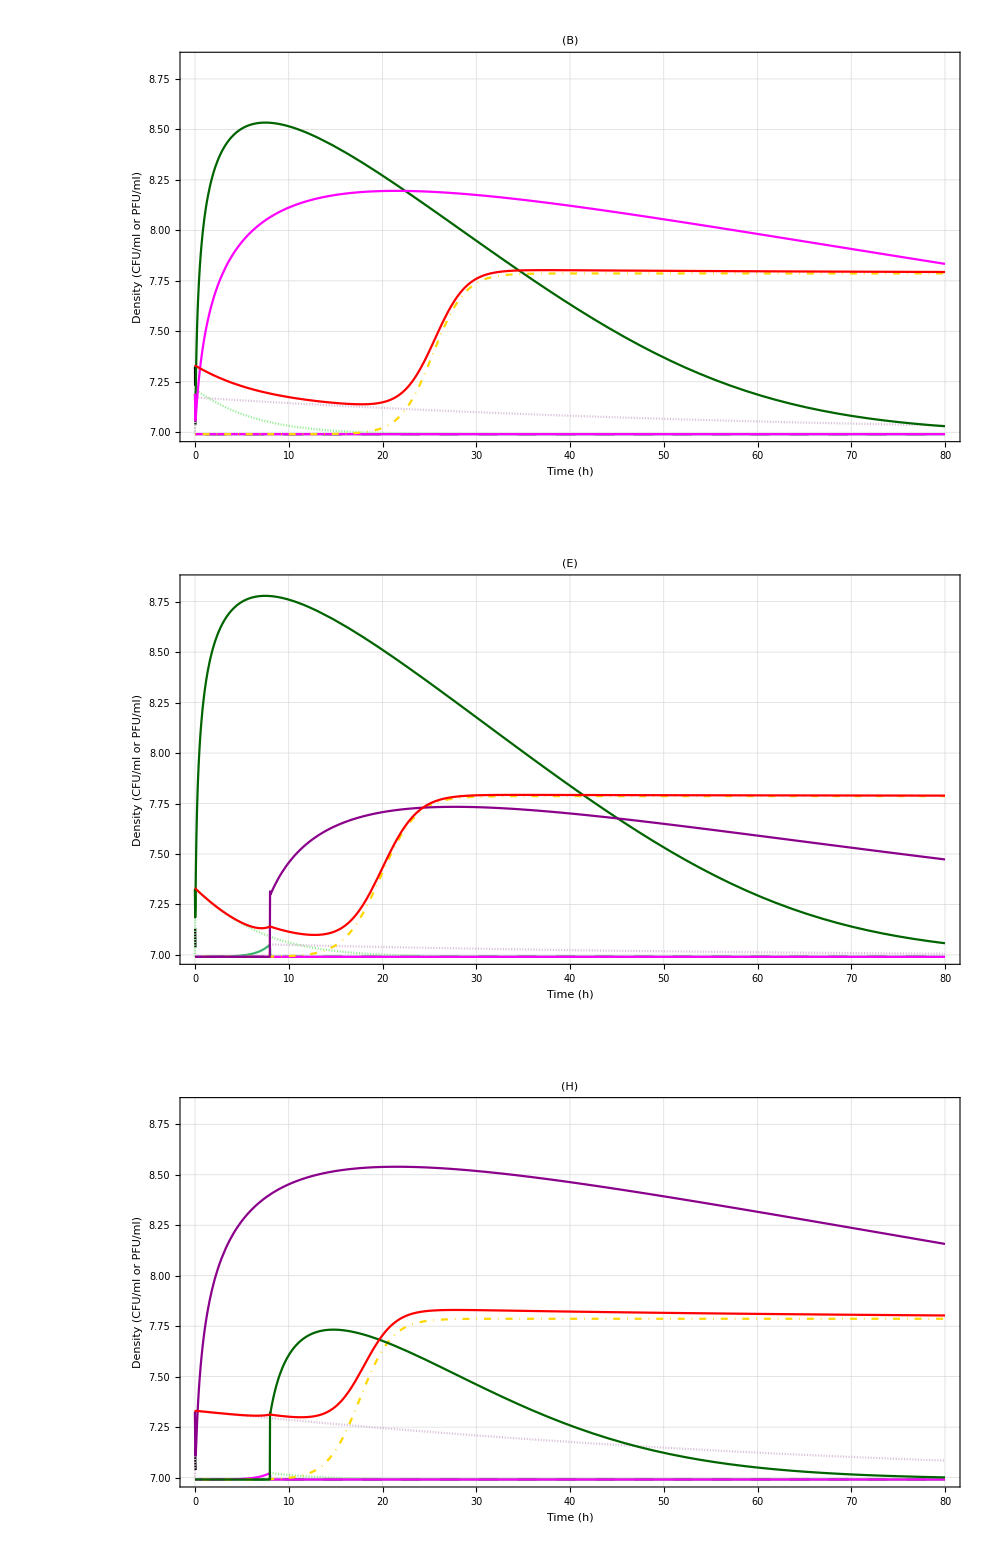

```mathematica
sub2=Legended[GraphicsGrid[{{gdb},{gde},{gdh}},Alignment->Center,Spacings->0,ImageSize->1000],Placed[LineLegend[{Directive[Black,ansLine],{RGBColor["lightgreen"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumseagreen"],smLine},{RGBColor["magenta"],smLine},{RGBColor["gold"],dmLine},{RGBColor["darkgreen"],pline},{RGBColor["magenta"],pline},{Red}},{Style["Ancestral bacteria",Bold,20],Style["LUZ19-infected Bacteria",Bold,20],Style["E215-infected Bacteria",Bold,20],Style["LUZ19-resistant Single Mutant",Bold,20],Style["E215-resistant Single Mutant",Bold,20],Style["(LUZ19, E215)-resistant Double Mutant",Bold,20],Style["LUZ19",Bold,20],Style["E215",Bold,20],Style["Total Bacteira",Bold,20]},LegendLayout->{"Column",3}],Bottom]]
```

```mathematica
PlotStyle->{{Black},{RGBColor["powderblue"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{RGBColor["darkmagenta"],pline},{Red}}
```

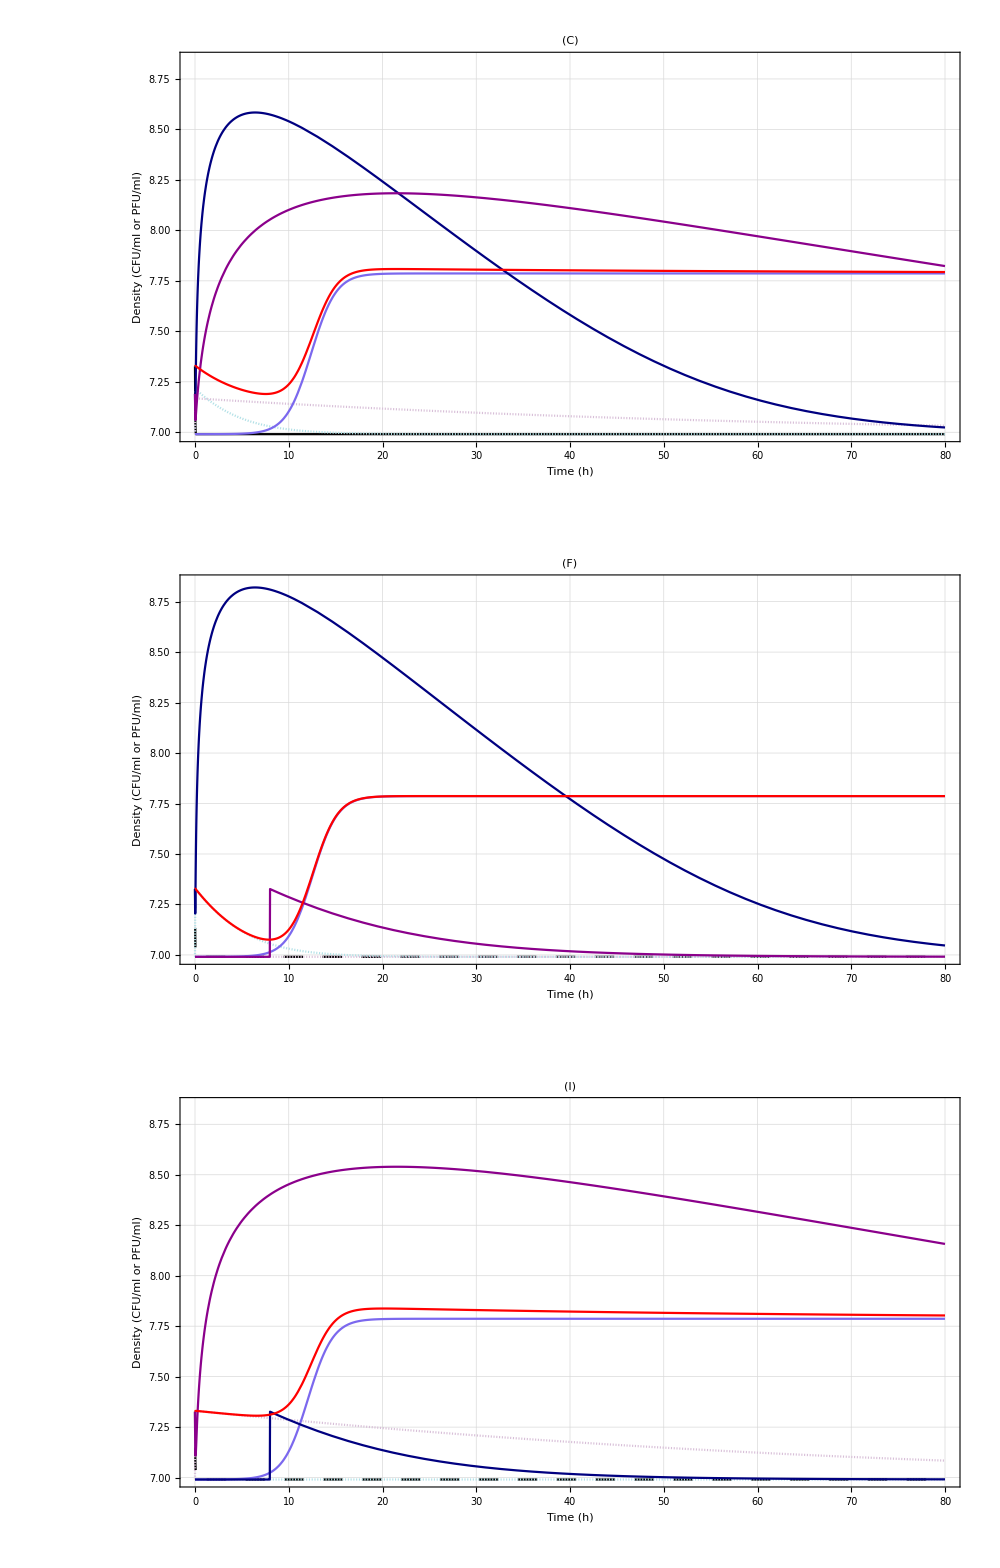

```mathematica
sub3=Legended[GraphicsGrid[{{gdc},{gdf},{gdi}},Alignment->Center,Spacings->0,ImageSize->1000],Placed[LineLegend[{Directive[Black,ansLine],{RGBColor["powderblue"],infLine},{RGBColor["thistle"],infLine},{RGBColor["mediumslateblue"],smLine},{RGBColor["navy"],pline},{RGBColor["magenta"],pline},{Red}},{Style["Ancestral bacteria",Bold,20],Style["PYO2-infected Bacteria",Bold,20],Style["E215-infected Bacteria",Bold,20],Style["(PYO2, E215)-resistant Single Mutant",Bold,20],Style["PYO2",Bold,20],Style["E215",Bold,20],Style["Total Bacteira",Bold,20]},LegendLayout->{"Column",3}],Bottom]]
```

```mathematica
Export["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\Image_final\\ModelSolution_doublephageWithMOI0.5eachPhageForSimultaneous_CFU_log_infect_all_conditions-reformat-LUZ19-PYO2.png",%228,"PNG"]
```

C:\Users\zhiyu\Dropbox\Stan Yu\Phage project\simulation\Image_final\ModelSolution_doublephageWithMOI0.5eachPhageForSimultaneous_CFU_log_infect_all_conditions-reformat-LUZ19-PYO2.png

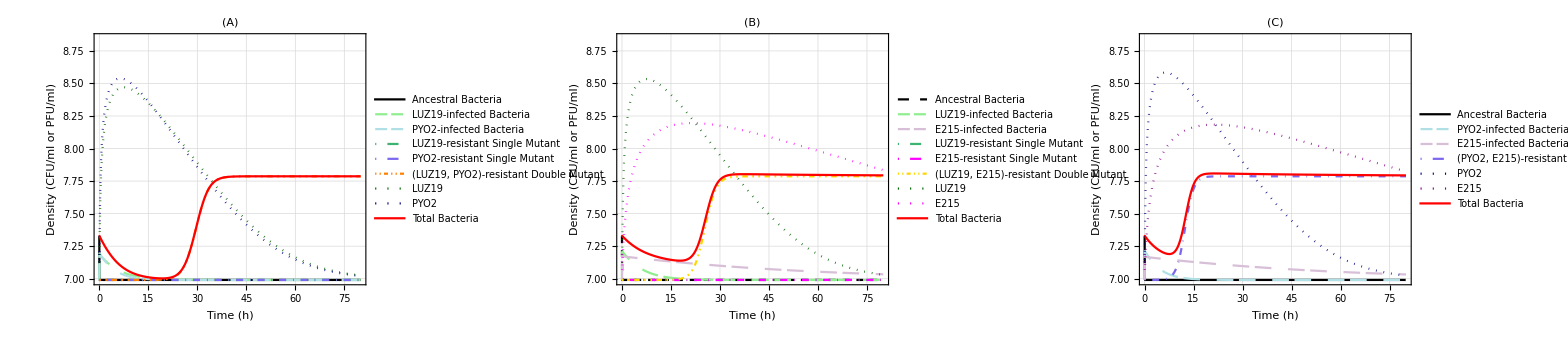

```mathematica
"Ancestral Bacteria","LUZ19-infected\nBacteria","PYO2-infected\nBacteria","LUZ19-resistant\nSingle Mutant","PYO2-resistant\nSingle Mutant","(LUZ19, PYO2)-resistant\nDouble Mutant","LUZ19","PYO2","Total Bacteria"
```

## Double phage simulations

### Phage AB simultaneous

#### Initialization cell for simultaneous cocktail

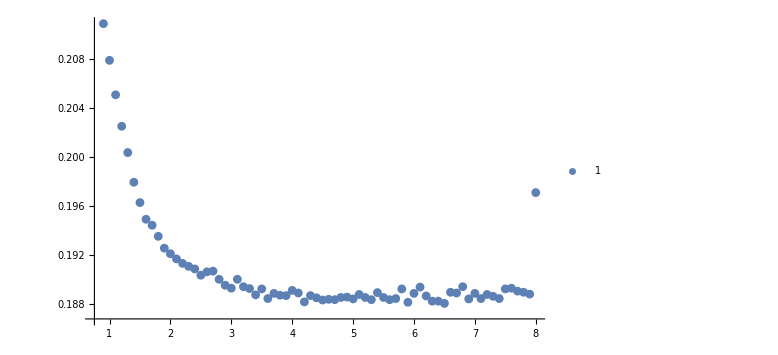
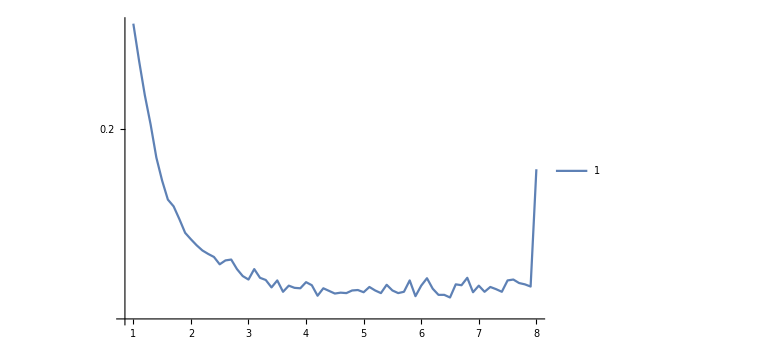

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
ABSIMOI01=Replace[Transpose[{TIME,ABData[[4,1]]}],{x_,y_}/;y<0->{x,0},1];
ABSIMOI1=Replace[Transpose[{TIME,ABData[[5,1]]}],{x_,y_}/;y<0->{x,0},1];
ABSIMOI10=Replace[Transpose[{TIME,ABData[[6,1]]}],{x_,y_}/;y<0->{x,0},1];
ABSIMOI01INI=Select[ABSIMOI01,#[[1]]==1.2&][[1,2]];
ABSIMOI1INI=Select[ABSIMOI1,#[[1]]==0.9&][[1,2]];
ABSIMOI10INI=Select[ABSIMOI10,#[[1]]==0.5&][[1,2]];
doublePhageSIMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={ABSIMOI01INI,0,0,0,0,0,ABSIMOI01INI*0.1,ABSIMOI01INI*0.1,ABSIMOI01INI}},Bt,{t,0,27.9},{a3,rab,k}];
doublePhageSIMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={ABSIMOI1INI,0,0,0,0,0,ABSIMOI1INI*0.5,ABSIMOI1INI*0.5,ABSIMOI1INI}},Bt,{t,0,50},{a3,rab,k}];
doublePhageSIMOI1All=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={ABSIMOI1INI,0,0,0,0,0,ABSIMOI1INI,ABSIMOI1INI,ABSIMOI1INI}},Y[t],{t,0,50},{a3,rab,k}];
doublePhageSIMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={ABSIMOI10INI,0,0,0,0,0,ABSIMOI10INI*10,ABSIMOI10INI*10,ABSIMOI10INI}},Bt,{t,0,27.9},{a3,rab,k}];
ListLogPlot[Select[ABSIMOI1,1<=#[[1]]≤8&],Joined->True,PlotLegends->{"1"},ImageSize->Large,PlotRange->All]ListPlot[Select[ABSIMOI1,0.9<=#[[1]]≤8&],PlotLegends->{"1"},ImageSize->Large,PlotRange->All]
```

#### Parameter estimation and simulations

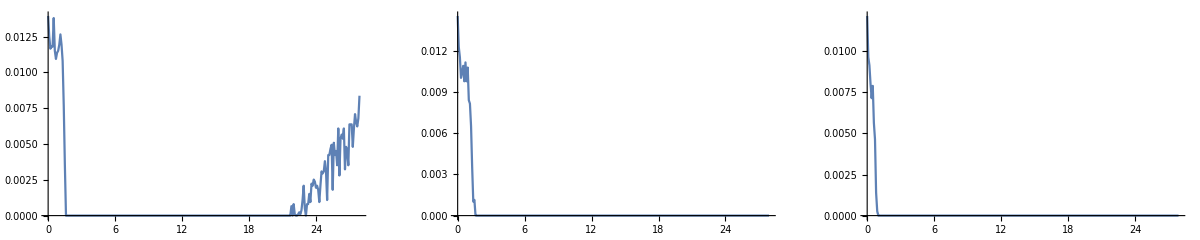

```mathematica
GraphicsGrid[{{ListLinePlot[ABSIMOI01,ImageSize->Large,PlotRange->All],ListLinePlot[ABSIMOI1,ImageSize->Large],ListLinePlot[ABSIMOI10,ImageSize->Large]}},ImageSize->Full]
```

```mathematica
ABSIMOI01NoLag=Select[ABSIMOI01,#[[1]]≥1.2&];
ABSIMOI1NoLag=Select[ABSIMOI1,#[[1]]≥0.9&];
ABSIMOI10NoLag=Select[ABSIMOI10,#[[1]]≥0.5&];
```

```mathematica
fitABSIMOI01[a3_,rab_,k_,t_]:=doublePhageSIMOI01[a3,rab,k][t];
fitModelABSIMOI01=NonlinearModelFit[ABSIMOI01NoLag,{fitABSIMOI01[a3,rab,0.03,t],a3==4.32*10^-7,0.4<rab<0.87},{a3,{rab,0.56}},t];
fitModelABSIMOI01[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 1.03495, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

{a3→4.32×10^-7,rab→0.486332}

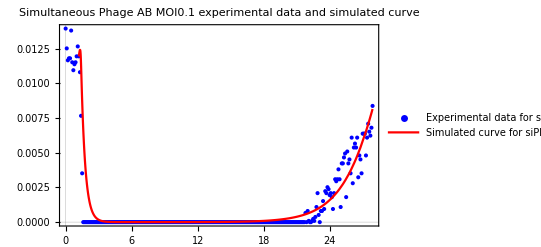

```mathematica
GABSIMOI01=Show[ListPlot[ABSIMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage AB MOI0.1"},LegendFunction->Framed],{0.5,0.4}],PlotStyle->Blue],Plot[fitModelABSIMOI01[t],{t,1.2,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage AB MOI0.1"},LegendFunction->Framed],{0.5,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage AB MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
fitABSIMOI1[a3_,rab_,k_,t_]:=doublePhageSIMOI1[a3,rab,k][t];
fitModelABSIMOI1=NonlinearModelFit[ABSIMOI1NoLag,{fitABSIMOI1[a3,rab,0.6,t],a3==7.2*10^-6,rab==0.54},{a3,{rab,0.56}},t]
fitModelABSIMOI1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.889875, step size is effectively zero; singularity or stiff system suspected.

FittedModel[InterpolatingFunction[…][t]]

{a3→7.2×10^-6,rab→0.54}

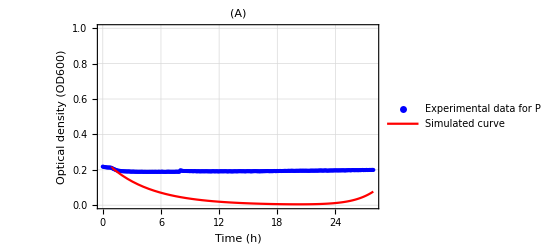

```mathematica
GABSIMOI1=Show[ListPlot[ABSIMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\nPhage LUZ19+PYO2 MOI1"}],{0.5,0.4}],PlotStyle->Blue,PlotRange->{{0,27.9},{0,1}},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(A)"],Plot[fitModelABSIMOI1[t],{t,0.9,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.5,0.6}]],PlotRange->{{0,27.9},{0,1}},Frame->True,ImageSize->Full]
```

```mathematica
doublePhageSIMOI1All[7.2*^-6,0.54,0.6]/.t->9
Y[t]
```

{1.53055×10^-13,0.0226103,0.0141101,-5.29439×10^-16,5.7196×10^-14,1.0692×10^-6,5.40552,5.8942,0.0367215}

{B[t],Bia[t],Bib[t],Ba[t],Bb[t],Bab[t],Pa[t],Pb[t],Bt[t]}

```mathematica
fitABSIMOI10[a3_,rab_,k_,t_]:=doublePhageSIMOI10[a3,rab,k][t];
fitModelABSIMOI10=NonlinearModelFit[ABSIMOI10NoLag,{fitABSIMOI10[a3,rab,0.03,t],a3==4.32*10^-7,0.48<rab<0.87},{a3,{rab,0.56}},t]
fitModelABSIMOI10[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.448846, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

ParametricNDSolveValue::ndsz: At t == 0.448846, step size is effectively zero; singularity or stiff system suspected.

FittedModel[InterpolatingFunction[…][t]]

{a3→4.32×10^-7,rab→0.481655}

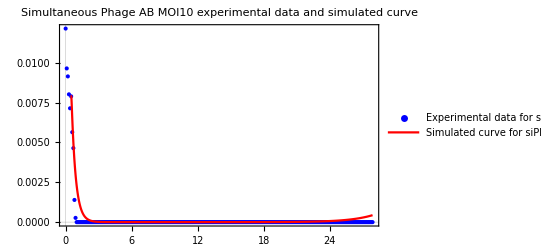

```mathematica
GABSIMOI10=Show[ListPlot[ABSIMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage AB MOI10"},LegendFunction->Framed],{0.5,0.4}],PlotStyle->Blue],Plot[fitModelABSIMOI10[t],{t,0.5,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage AB MOI10"},LegendFunction->Framed],{0.5,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage AB MOI10 experimental data and simulated curve",ImageSize->Full]
```

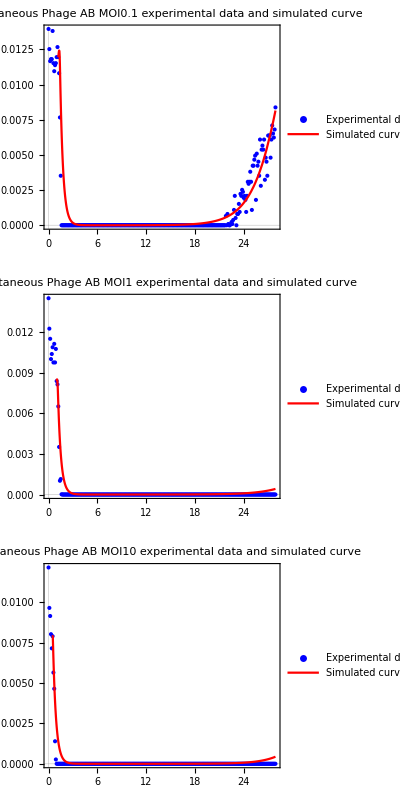

```mathematica
GABSI=GraphicsGrid[{{GABSIMOI01},{GABSIMOI1},{GABSIMOI10}},ImageSize->Full,Alignment->Center,Frame->True]
```

```mathematica
(* mutation rate from normal bacteria to bacteria resistant to both phage A and B*)
```

```mathematica
Mean[{7.00015189363841*^-7,2.222800865079936*^-7,3.7512133958409754*^-7}]
```

4.32472×10^-7

```mathematica
(* basal growth rate for acteria resistant to both phage A and B *)
```

```mathematica
Mean[{0.4863322378054661,0.401596792111701,0.4816552094548496}]
```

0.456528

### Phage AB sequential

#### Initialization cell for sequential cocktail

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia,-0.09*Pb+h*s2*Bib,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-b1*Bb*Pa,a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia,-0.09*Pb+h*s2*Bib,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-b1*Bb*Pa)+(a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-10*a2*Ba-b2*Ba*Pb+a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-10*a1*Bb-b1*Bb*Pa,10*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-a1*Bab,-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

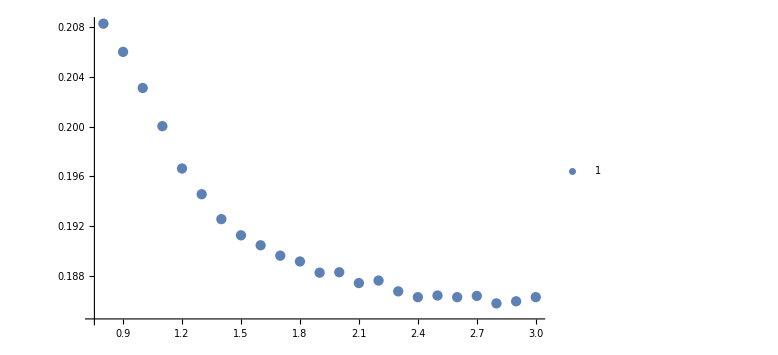
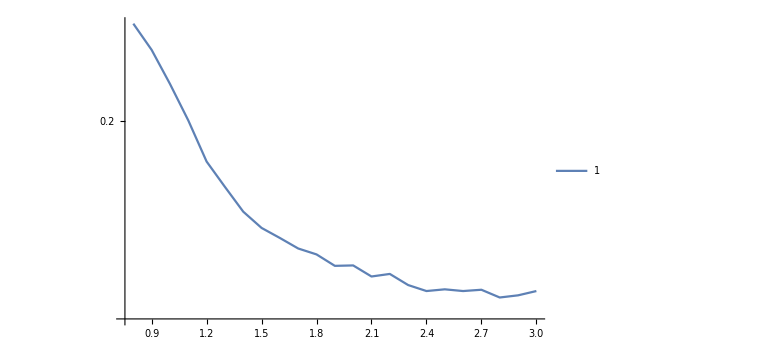

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2->0.25,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
ABMOI01=Transpose[{TIME,ABData[[1,1]]}];
ABMOI1=Transpose[{TIME,ABData[[2,1]]}];
ABMOI10=Transpose[{TIME,ABData[[3,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
ListLogPlot[{Select[ABMOI1,0.8<=#[[1]]≤3&]},Joined->True,PlotLegends->{"1"},ImageSize->Large]ListPlot[{Select[ABMOI1,0.8<=#[[1]]≤3&]},PlotLegends->{"1"},ImageSize->Large]
```

#### simulations

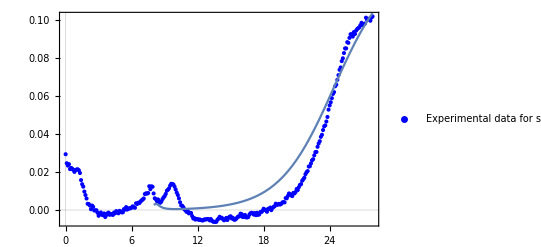

{k→0.129236,r→0.400001,u1→3.00019,u2→5.5}

```mathematica
Remove[ABSEQMOI01Model]
ABSEQMOI01INI=Select[ABMOI01,1.3==#[[1]]&][[1,2]];
ABMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.4,0.17,ABSEQMOI01INI,3,5.5][8]];
ABMOI01H8[[8]]=ABMOI01H8[[8]]+ABSEQMOI01INI*0.1;
ABMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI01H8},Bt,{t,8,27.9},{k,r,u1,u2}];
ABMOI01After8hFull=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI01H8},{Ba[t],Bb[t],Bab[t],Pa[t],Pb[t]},{t,8,50},{k,r,u1,u2}];
ABMOI01FitModel=NonlinearModelFit[Select[ABMOI01,8<=#[[1]]&],{ABMOI01After8h[k,r,u1,u2][t],0.1<k<0.18,0.5>r>0.4,3<u1<10,1<u2<10},{k,{r,0.5},{u1,10},{u2,10}},t];
Show[ListPlot[ABMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ABMOI01FitModel[t],{t,8,27.9}]]
ABMOI01FitModel[[1,2]]
```

```mathematica
Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.4,0.17,ABSEQMOI01INI][7.4]][[4;;8]]
Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.4,0.17,ABSEQMOI01INI][7.6]][[4;;8]]
Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.4,0.17,ABSEQMOI01INI][7.8]][[4;;8]]
ABMOI01H8[[4;;8]]
ABMOI01After8hFull[0.17,0.4]/.t->10
ABMOI01After8hFull[0.17,0.4]/.t->12
ABMOI01After8hFull[0.17,0.4]/.t->14
ABMOI01After8hFull[0.17,0.4]/.t->16
ABMOI01After8hFull[0.17,0.4]/.t->18
ABMOI01After8hFull[0.17,0.4]/.t->20
ABMOI01After8hFull[0.17,0.4]/.t->22
ABMOI01After8hFull[0.17,0.4]/.t->24
ABMOI01After8hFull[0.17,0.4]/.t->26
ABMOI01After8hFull[0.17,0.4]/.t->27.9
ABMOI01After8hFull[0.17,0.4]/.t->30
ABMOI01After8hFull[0.17,0.4]/.t->35
```

{0.000880489,9.30878×10^-8,0.00027621,1.28498,0.}

{0.00100115,1.08292×10^-7,0.000315561,1.26193,0.}

{0.00113821,1.25914×10^-7,0.000360323,1.23927,0.}

{0.00130985,1.61654×10^-7,0.000454248,1.21687,0.00195028}

{3.47483×10^-6,3.27444×10^-7,0.000766226,1.01512,0.0973288}

{5.44966×10^-6,5.39253×10^-7,0.00105246,0.846893,0.0849197}

{9.18396×10^-6,8.87678×10^-7,0.00144381,0.706007,0.0693306}

{0.0000156715,1.46063×10^-6,0.00197728,0.587829,0.0558519}

{0.0000270487,2.40272×10^-6,0.00270151,0.488449,0.0444365}

{0.0000461207,3.95277×10^-6,0.00367901,0.404558,0.0357866}

{0.0000712613,6.50668×10^-6,0.00498693,0.333353,0.0318126}

{0.0000913588,0.000010723,0.00671295,0.272498,0.0336213}

{0.000103717,0.0000177092,0.00894853,0.220152,0.0392455}

{0.000113455,0.0000286069,0.0116236,0.177223,0.0462329}

{0.000123866,0.0000485237,0.0152726,0.137504,0.0552228}

{0.000144846,0.000123925,0.0267925,0.0951855,0.0818109}

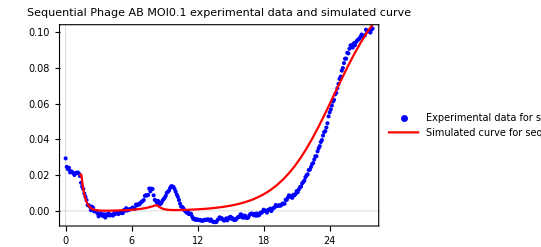

```mathematica
ABSEQMOI01Model[t_]:=doublePhageBefore8hMOI01[4.32*10^-7,0.4,0.13,ABSEQMOI01INI,3,5.5][t]/;1.3<=t<8
ABSEQMOI01Model[t_]:=ABMOI01After8h[0.13,0.4,3,5.5][t]/;t≥8
ABSEQG1=Show[ListPlot[ABMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI0.1"},LegendFunction->Framed],{0.34,0.4}],PlotStyle->Blue],Plot[ABSEQMOI01Model[t],{t,1.3,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage AB MOI0.1"},LegendFunction->Framed],{0.34,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage AB MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
ABMOI1
```

{{0.,0.2155},{0.1,0.2139},{0.2,0.212967},{0.3,0.211433},{0.4,0.210533},{0.5,0.210367},{0.6,0.209533},{0.7,0.2095},{0.8,0.208267},{0.9,0.206},{1.,0.2031},{1.1,0.200033},{1.2,0.196633},{1.3,0.194567},{1.4,0.192567},{1.5,0.191267},{1.6,0.190467},{1.7,0.189633},{1.8,0.189167},{1.9,0.188267},{2.,0.1883},{2.1,0.187433},{2.2,0.187633},{2.3,0.186767},{2.4,0.1863},{2.5,0.186433},{2.6,0.1863},{2.7,0.1864},{2.8,0.1858},{2.9,0.185967},{3.,0.1863},{3.1,0.185733},{3.2,0.185433},{3.3,0.185533},{3.4,0.185133},{3.5,0.1856},{3.6,0.1849},{3.7,0.185933},{3.8,0.185467},{3.9,0.1851},{4.,0.185167},{4.1,0.185033},{4.2,0.1853},{4.3,0.1852},{4.4,0.185267},{4.5,0.185233},{4.6,0.1847},{4.7,0.184633},{4.8,0.1857},{4.9,0.185833},{5.,0.185167},{5.1,0.185533},{5.2,0.185833},{5.3,0.185467},{5.4,0.185367},{5.5,0.1851},{5.6,0.186033},{5.7,0.185033},{5.8,0.1854},{5.9,0.1855},{6.,0.185567},{6.1,0.185733},{6.2,0.185133},{6.3,0.1852},{6.4,0.185667},{6.5,0.186},{6.6,0.185833},{6.7,0.1859},{6.8,0.186033},{6.9,0.186033},{7.,0.1859},{7.1,0.186067},{7.2,0.186067},{7.3,0.185933},{7.4,0.186567},{7.5,0.186433},{7.6,0.187},{7.7,0.187467},{7.8,0.1873},{7.9,0.187433},{8.,0.193418},{8.1,0.192506},{8.2,0.191261},{8.3,0.190783},{8.4,0.190943},{8.5,0.191187},{8.6,0.1908},{8.7,0.190533},{8.8,0.1907},{8.9,0.191467},{9.,0.190733},{9.1,0.1912},{9.2,0.1914},{9.3,0.191967},{9.4,0.191533},{9.5,0.1917},{9.6,0.191333},{9.7,0.191267},{9.8,0.191567},{9.9,0.191133},{10.,0.190567},{10.1,0.1907},{10.2,0.190333},{10.3,0.1903},{10.4,0.190833},{10.5,0.190067},{10.6,0.190433},{10.7,0.1911},{10.8,0.1912},{10.9,0.1902},{11.,0.1901},{11.1,0.189933},{11.2,0.189767},{11.3,0.190167},{11.4,0.19},{11.5,0.190167},{11.6,0.190367},{11.7,0.1898},{11.8,0.189833},{11.9,0.190233},{12.,0.189567},{12.1,0.189933},{12.2,0.1903},{12.3,0.1902},{12.4,0.189733},{12.5,0.1901},{12.6,0.190267},{12.7,0.19},{12.8,0.189933},{12.9,0.190067},{13.,0.190533},{13.1,0.190267},{13.2,0.1906},{13.3,0.1903},{13.4,0.189933},{13.5,0.189867},{13.6,0.19},{13.7,0.1906},{13.8,0.190133},{13.9,0.190367},{14.,0.190767},{14.1,0.1906},{14.2,0.189967},{14.3,0.190367},{14.4,0.1907},{14.5,0.191067},{14.6,0.1903},{14.7,0.190267},{14.8,0.1909},{14.9,0.1914},{15.,0.191},{15.1,0.1904},{15.2,0.1911},{15.3,0.191367},{15.4,0.190633},{15.5,0.190733},{15.6,0.191067},{15.7,0.191333},{15.8,0.191233},{15.9,0.1916},{16.,0.191167},{16.1,0.191433},{16.2,0.191767},{16.3,0.191867},{16.4,0.1922},{16.5,0.191967},{16.6,0.191467},{16.7,0.191733},{16.8,0.192833},{16.9,0.192633},{17.,0.193133},{17.1,0.1926},{17.2,0.193},{17.3,0.192767},{17.4,0.193033},{17.5,0.193567},{17.6,0.1939},{17.7,0.1938},{17.8,0.1942},{17.9,0.194433},{18.,0.194767},{18.1,0.195067},{18.2,0.195933},{18.3,0.196},{18.4,0.1968},{18.5,0.196467},{18.6,0.197233},{18.7,0.197333},{18.8,0.198467},{18.9,0.198667},{19.,0.199167},{19.1,0.1996},{19.2,0.2006},{19.3,0.200767},{19.4,0.200967},{19.5,0.201367},{19.6,0.202567},{19.7,0.202867},{19.8,0.2032},{19.9,0.204567},{20.,0.205067},{20.1,0.206433},{20.2,0.206933},{20.3,0.207933},{20.4,0.2087},{20.5,0.210033},{20.6,0.2118},{20.7,0.213967},{20.8,0.215867},{20.9,0.2164},{21.,0.218433},{21.1,0.2191},{21.2,0.2193},{21.3,0.220667},{21.4,0.221567},{21.5,0.222333},{21.6,0.223767},{21.7,0.225867},{21.8,0.2276},{21.9,0.228967},{22.,0.230233},{22.1,0.230733},{22.2,0.2319},{22.3,0.232133},{22.4,0.2331},{22.5,0.234767},{22.6,0.233533},{22.7,0.235033},{22.8,0.235367},{22.9,0.236433},{23.,0.238467},{23.1,0.237867},{23.2,0.2385},{23.3,0.24},{23.4,0.2405},{23.5,0.242767},{23.6,0.243},{23.7,0.244633},{23.8,0.2455},{23.9,0.247767},{24.,0.2494},{24.1,0.251267},{24.2,0.2538},{24.3,0.254933},{24.4,0.255633},{24.5,0.256567},{24.6,0.2576},{24.7,0.258667},{24.8,0.2593},{24.9,0.259667},{25.,0.2611},{25.1,0.2626},{25.2,0.262933},{25.3,0.264733},{25.4,0.265733},{25.5,0.267067},{25.6,0.2683},{25.7,0.269967},{25.8,0.271333},{25.9,0.2733},{26.,0.275367},{26.1,0.277733},{26.2,0.279233},{26.3,0.281267},{26.4,0.281933},{26.5,0.284967},{26.6,0.286933},{26.7,0.2889},{26.8,0.2901},{26.9,0.291133},{27.,0.291833},{27.1,0.293467},{27.2,0.2946},{27.3,0.296033},{27.4,0.2972},{27.5,0.298133},{27.6,0.299033},{27.7,0.2999},{27.8,0.300867},{27.9,0.3018}}

ParametricNDSolveValue::ndsz: At t == 0.789737, step size is effectively zero; singularity or stiff system suspected.

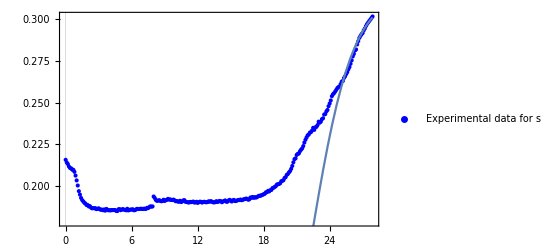

{k→0.316,r→0.51}

```mathematica
Remove[ABSEQMOI1Model]
ABSEQMOI1INI=Select[ABMOI1,0.8==#[[1]]&][[1,2]];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.51,0.316,ABSEQMOI1INI,1,1][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+ABSEQMOI1INI;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Bt,{t,8,27.9},{k,r,u1,u2}];
ABMOI1FitModel=NonlinearModelFit[Select[ABMOI1,8<=#[[1]]&],{ABMOI1After8h[k,r,1,1][t],0.1<k<0.316,0.51>r>0.37},{k,{r,0.5}},t];
Show[ListPlot[ABMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ABMOI1FitModel[t],{t,8,27.9}]]
ABMOI1FitModel[[1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.320377,r→0.284883}

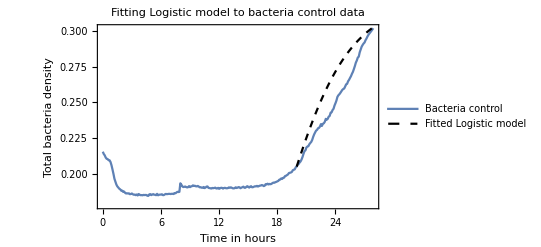

```mathematica
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[20]==0.20506666666666665} ,y[t],t][[1,1,2]];
para=FindFit[Select[ABMOI1,27.9>=#[[1]]≥20&],{germGrowth[k,r,t],0.35>r>0.2,0.4>k>0},{{k,0.4},{r,0.37}},t]
Show[ListLinePlot[ABMOI1,PlotLegends->Placed[LineLegend[{"Bacteria control"}],{0.15,0.9}]],Plot[germGrowth[k,r,t]/.para,{t,20,27.9},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}],PlotRange->All],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to bacteria control data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

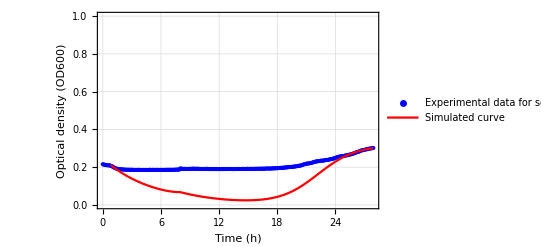

```mathematica
ABSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[4.32*10^-7,0.51,0.316,ABSEQMOI1INI,1,1][t]/;0.8<=t<8
ABSEQMOI1Model[t_]:=ABMOI1After8h[0.316,0.51,1,1][t]/;t≥8
ABSEQG2=Show[ListPlot[ABMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI1"}],{0.25,0.5}],PlotStyle->Blue,FrameLabel->{"Time (h)","Optical density (OD600)"}],Plot[ABSEQMOI1Model[t],{t,0.8,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

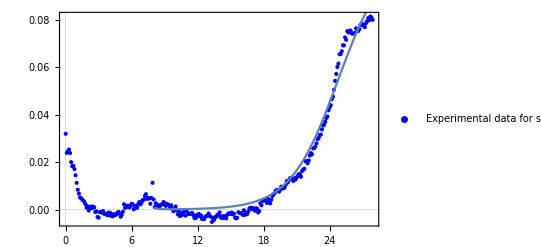

{k→0.109043,r→0.459271,u1→3.02402,u2→5.5}

```mathematica
Remove[ABSEQMOI10Model]
ABSEQMOI10INI=Select[ABMOI10,0.5==#[[1]]&][[1,2]];
ABMOI10H8=Through[doublePhageBefore8hMOI10Full[4.32*10^-7,0.46,0.105,ABSEQMOI10INI,3,10][8]];
ABMOI10H8[[8]]=ABMOI10H8[[8]]+ABSEQMOI10INI*10;
ABMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI10H8},Bt,{t,8,27.9},{k,r,u1,u2}];
ABMOI10FitModel=NonlinearModelFit[Select[ABMOI10,9<=#[[1]]&],{ABMOI10After8h[k,r,u1,u2][t],0.1<k<0.18,3<u1<4,u2==5.5},{k,{r,0.5},u1,u2},t];
Show[ListPlot[ABMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI10"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ABMOI10FitModel[t],{t,8,27.9}]]
ABMOI10FitModel[[1,2]]
```

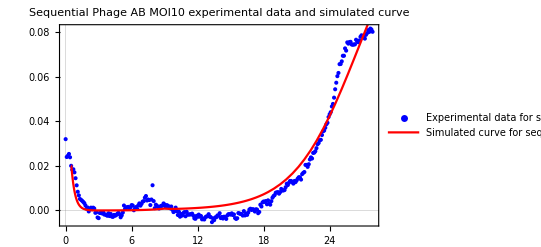

```mathematica
ABSEQMOI10Model[t_]:=doublePhageBefore8hMOI10[4.32*10^-7,0.51,0.16,ABSEQMOI10INI][t]/;0.5<=t<9
ABSEQMOI10Model[t_]:=ABMOI10After8h[0.16,0.51][t]/;t≥9
ABSEQG3=Show[ListPlot[ABMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI10"},LegendFunction->Framed],{0.34,0.4}],PlotStyle->Blue],Plot[ABSEQMOI10Model[t],{t,0.5,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage AB MOI10"},LegendFunction->Framed],{0.34,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage AB MOI10 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
(* Before data processing *)
```

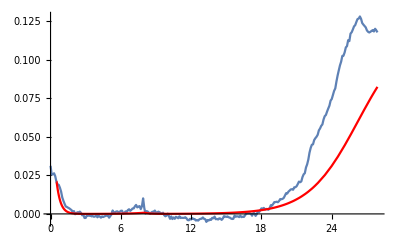

-Graphics-

```mathematica
Mean[{0.4,0.4,0.46}]
```

0.42

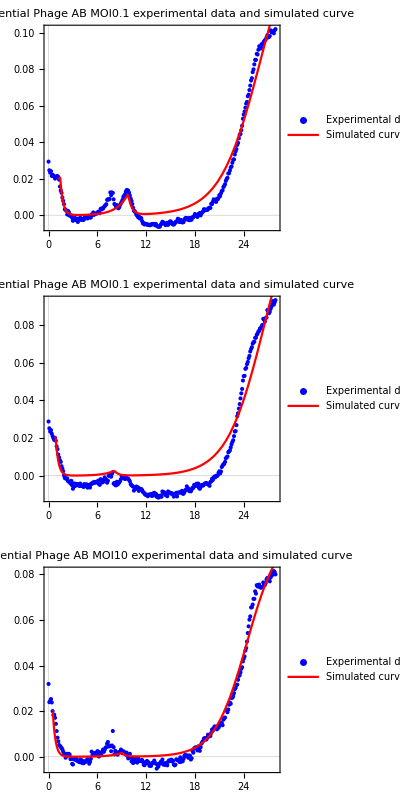

```mathematica
GABSEQ=GraphicsGrid[{{ABSEQG1},{ABSEQG2},{ABSEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

#### Estimate rab

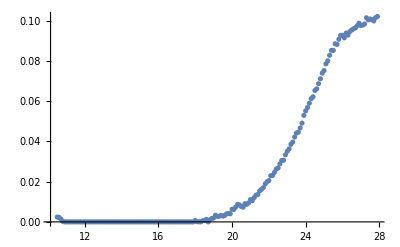

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

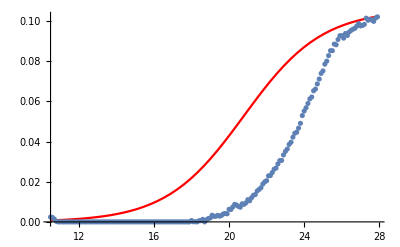

{k→0.105597,r→0.48161}

```mathematica
Remove[para]
BabGrowth=Replace[Select[ABMOI01,10.5<=#[[1]]≤27.9&],{x_,y_}/;y<0->{x,0},1];
ListPlot[BabGrowth]
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t]*(1-y[t]/k),y[13]==BabGrowth[[1,2]]} ,y[t],t][[1,1,2]];
para=FindFit[BabGrowth,{germGrowth[k,r,t],0.46<r<0.5,0.09<k<0.12},{k,{r,0.4}},t];
Show[Plot[germGrowth[para[[1,2]],para[[2,2]],t],{t,10.5,27.9},PlotRange->All,PlotStyle->Red],ListPlot[BabGrowth]]
para
```

```mathematica
germGrowth[para[[1,2]],para[[2,2]],10]
```

0.000580577

### Phage BA sequential

```mathematica
(* 解释delay *)
```

#### Initialization cell for sequential cocktail

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia,-0.09*Pb+h*s2*Bib,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))}
```

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
BAData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
BAMOI01=Transpose[{TIME,BAData[[7,1]]}];
BAMOI1=Transpose[{TIME,BAData[[8,1]]}];
BAMOI10=Transpose[{TIME,BAData[[9,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,0,B0*0.1,B0}},Bt,{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,0,B0*0.1,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={B0,0,0,0,0,0,0,B0,B0}},Bt,{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.2]=={B0,0,0,0,0,0,0,B0*10,B0}},Bt,{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.2]=={B0,0,0,0,0,0,0,B0*10,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,25},{a3,rab,k,B0,f,u1,u2}];
GraphicsGrid[{{ListLogPlot[{Select[BAMOI1,1.2<=#[[1]]≤5&]},Joined->True,PlotLegends->{"1"},ImageSize->Medium],ListPlot[{Select[BAMOI1,1.2<=#[[1]]≤5&]},PlotLegends->{"1"},ImageSize->Medium]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

#### Simulations

```mathematica
Remove[BASEQMOI01Model]
BASEQMOI01INI=Select[BAMOI01,1.6==#[[1]]&][[1,2]];
BAMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.8,0.12,BASEQMOI01INI,1,0,5.5][8]];
BAMOI01H8[[7]]=BAMOI01H8[[7]]+BASEQMOI01INI*0.1;
BAMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI01H8},Bt,{t,8,27.9},{k,r,f,u1,u2}];
```

ParametricNDSolveValue::ndsz: At t == 1.431, step size is effectively zero; singularity or stiff system suspected.

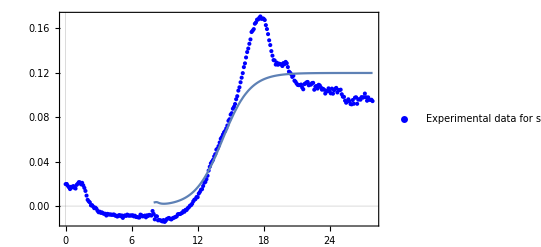

{k→0.119809,r→0.799999}

```mathematica
BAMOI01After8hFull=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI01H8},{Ba[t],Bia[t],Bib[t],Bb[t],Bab[t],Pa[t],Pb[t]},{t,8,40},{k,r,f,u1,u2}];
BAMOI01FitModel=NonlinearModelFit[Select[BAMOI01,8<=#[[1]]&],{BAMOI01After8h[k,r,1,0,5.5][t],0<k,0.8>=r>0.46},{k,{r,0.5}},t];
Show[ListPlot[BAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BAMOI01FitModel[t],{t,8,27.9}]]
BAMOI01FitModel[[1,2]]
```

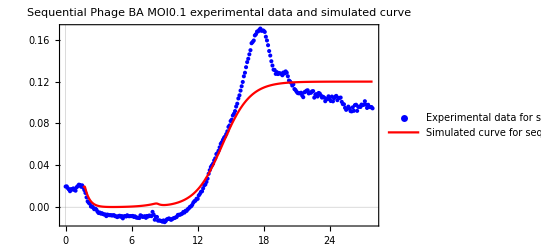

```mathematica
BASEQMOI01Model[t_]:=doublePhageBefore8hMOI01[4.32*10^-7,0.8,0.12,BASEQMOI01INI,1,0,5.5][t]/;1.6<=t<8
BASEQMOI01Model[t_]:=BAMOI01After8h[0.12,0.8,1,0,5.5][t]/;t≥8
BASEQG1=
Show[ListPlot[BAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BASEQMOI01Model[t],{t,1.6,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage BA MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

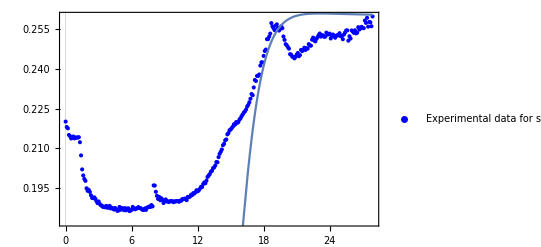

{k→0.260002,r→0.86}

```mathematica
Remove[BASEQMOI1Model]
BASEQMOI1INI=Select[BAMOI1,1.2==#[[1]]&][[1,2]];
BAMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.86,0.26,BASEQMOI1INI,1,0,1][8]];
BAMOI1H8[[7]]=BAMOI1H8[[7]]+BASEQMOI1INI;
BAMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI1H8},Bt,{t,8,27.9},{k,r,f,u1,u2}];
BAMOI1FitModel=NonlinearModelFit[Select[BAMOI1,8<=#[[1]]&],{BAMOI1After8h[k,r,1,0,1][t],0.26<k<0.27,0.86>=r>0.46},{{k,0.15},{r,0.5}},t];
Show[ListPlot[BAMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BAMOI1FitModel[t],{t,8,27.9}]]
BAMOI1FitModel[[1,2]]
```

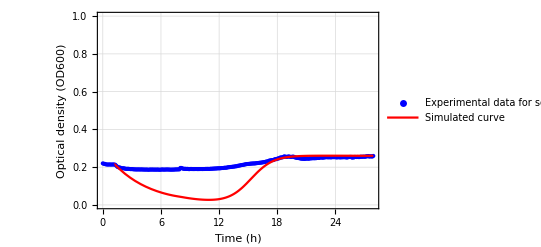

```mathematica
BASEQMOI1Model[t_]:=doublePhageBefore8hMOI1[4.32*10^-7,0.86,0.26,BASEQMOI1INI,1,0,1][t]/;1.2<=t<8
BASEQMOI1Model[t_]:=BAMOI1After8h[0.26,0.86,1,0,1][t]/;t≥8
BASEQG2=Show[ListPlot[BAMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI1"}],{0.25,0.5}],PlotStyle->Blue],Plot[BASEQMOI1Model[t],{t,1.2,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

ParametricNDSolveValue::ndsz: At t == 0.158765, step size is effectively zero; singularity or stiff system suspected.

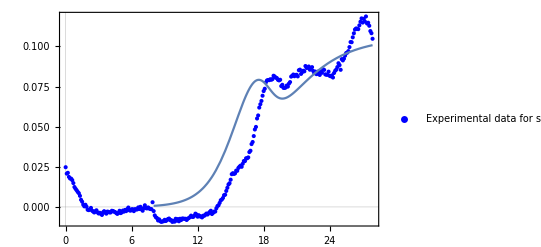

{k→0.165242,r→0.564425,f→0.00111111,u1→30.0001,u2→19.9999}

```mathematica
Remove[BASEQMOI10Model]
BASEQMOI10INI=Select[BAMOI10,0.2==#[[1]]&][[1,2]];
BAMOI10H8=Through[doublePhageBefore8hMOI10Full[4.32*10^-7,0.5,0.17,BASEQMOI10INI,1/900,30,20][8]];
BAMOI10H8[[7]]=BAMOI10H8[[7]]+BASEQMOI10INI*10;
BAMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI10H8},Bt,{t,8,27.9},{k,r,f,u1,u2}];
BAMOI10FitModel=NonlinearModelFit[Select[BAMOI10,8<=#[[1]]&],{BAMOI10After8h[k,r,f,u1,u2][t],0.15<k,r>0.5,1/3000<f<1/900,30<u1<31,10<u2<20},{{k,0.15},{r,0.5},{f,1/600},{u1,24},{u2,20}},t];
Show[ListPlot[BAMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI10"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BAMOI10FitModel[t],{t,8,27.9}]]
BAMOI10FitModel[[1,2]]
```

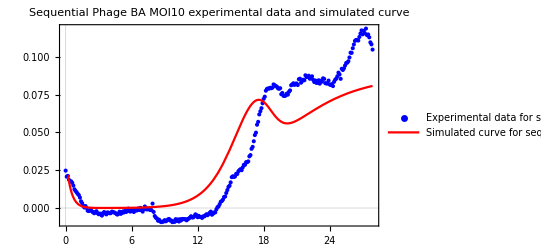

```mathematica
BASEQMOI10Model[t_]:=doublePhageBefore8hMOI10[4.32*10^-7,0.5,0.15,BASEQMOI10INI,1/900,30,20][t]/;0.2<=t<8
BASEQMOI10Model[t_]:=BAMOI10After8h[0.15,0.5,1/900,30,20][t]/;t≥8
BASEQG3=Show[ListPlot[BAMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI10"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BASEQMOI10Model[t],{t,0.2,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage BA MOI10"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage BA MOI10 experimental data and simulated curve",ImageSize->Full]
```

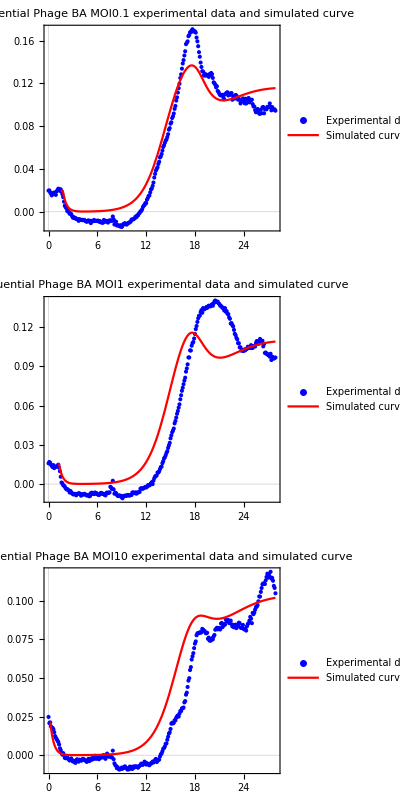

```mathematica
GBASEQ=GraphicsGrid[{{BASEQG1},{BASEQG2},{BASEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

#### Estimate rba

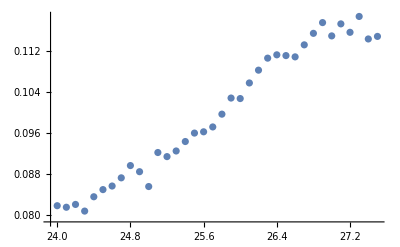

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
BbaGrowth=Select[BAMOI10,24<=#[[1]]≤27.5&];
ListPlot[BbaGrowth]
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[24]==BbaGrowth[[1,2]]} ,y[t],t][[1,1,2]];
```

```mathematica
FindFit[BbaGrowth,germGrowth[k,r,t],{{k,0.14},{r,0.4}},t]
```

{k→0.440521,r→0.144545}

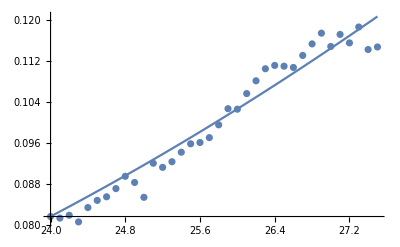

```mathematica
Show[Plot[germGrowth[0.44052146338898307,0.1445454134293657,t],{t,24,27.5},PlotRange->All],ListPlot[BbaGrowth]]
```

### Phage AC simultaneous

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+a3*Bab+a1*Ba+a2*Bb,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb-a1*Ba+1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa-a2*Bb+1/2*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-a3*Bab-a1*Bab,-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.01,s2-> 1.05,b2->277,h->100,u1->3,u2->5.5};
```

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
doubleData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
ACSIMOI01Ori=Transpose[{TIME,doubleData[[10,1]]}];
ACSIMOI01=Replace[Transpose[{TIME,doubleData[[10,1]]}],{x_,y_}/;y<0->{x,0},1];
ACSIMOI1=Replace[Transpose[{TIME,doubleData[[11,1]]}],{x_,y_}/;y<0->{x,0},1];
ACSIMOI10=Replace[Transpose[{TIME,doubleData[[12,1]]}],{x_,y_}/;y<0->{x,0},1];
ACSIMOI01INI=Select[ACSIMOI01,#[[1]]==1.2&][[1,2]];
ACSIMOI1INI=Select[ACSIMOI1,#[[1]]==0.7&][[1,2]];
ACSIMOI10INI=Select[ACSIMOI10,#[[1]]==0.1&][[1,2]];
doublePhageSIMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.2]=={ACSIMOI01INI,0,0,0,0,0,ACSIMOI01INI*0.1,ACSIMOI01INI*0.1,ACSIMOI01INI}},Bt,{t,0,27.9},{a3,rab,k}];
doublePhageSIMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.7]=={ACSIMOI1INI,0,0,0,0,0,ACSIMOI1INI*0.5,ACSIMOI1INI*0.5,ACSIMOI1INI}},Bt,{t,0,50},{a3,rab,k}];
doublePhageSIMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.7]=={ACSIMOI1INI,0,0,0,0,0,ACSIMOI1INI,ACSIMOI1INI,ACSIMOI1INI}},Y[t],{t,0,70},{a3,rab,k}];
doublePhageSIMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.1]=={ACSIMOI10INI,0,0,0,0,0,ACSIMOI10INI*10,ACSIMOI10INI*10,ACSIMOI10INI}},Bt,{t,0,27.9},{a3,rab,k}];
GraphicsGrid[{{ListLogPlot[{Select[ACSIMOI1,0.8<=#[[1]]≤5&]},Joined->True,PlotLegends->{"0.1","1","10"},ImageSize->Medium,PlotRange->All],ListPlot[{Select[ACSIMOI1,0.8<=#[[1]]≤5&]},PlotLegends->{"0.1","1","10"},ImageSize->Medium,PlotRange->All]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Select[ACSIMOI01,#[[1]]==22&][[1,2]]
```

0.235071

```mathematica
Select[ACSIMOI01,#[[1]]>=24&]
```

{{24.,0.220707},{24.1,0.222116},{24.2,0.223889},{24.3,0.223389},{24.4,0.225798},{24.5,0.22748},{24.6,0.228116},{24.7,0.229434},{24.8,0.231343},{24.9,0.233843},{25.,0.235071},{25.1,0.237116},{25.2,0.239434},{25.3,0.242071},{25.4,0.244434},{25.5,0.248071},{25.6,0.250843},{25.7,0.253889},{25.8,0.257252},{25.9,0.259525},{26.,0.261662},{26.1,0.263934},{26.2,0.265571},{26.3,0.267389},{26.4,0.269889},{26.5,0.272571},{26.6,0.276116},{26.7,0.279116},{26.8,0.281707},{26.9,0.283798},{27.,0.287071},{27.1,0.289934},{27.2,0.293616},{27.3,0.29548},{27.4,0.29798},{27.5,0.298571},{27.6,0.300752},{27.7,0.301707},{27.8,0.303025},{27.9,0.304525}}

```mathematica
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[25]==Select[ACSIMOI01,#[[1]]==25&][[1,2]]} ,y[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
para=FindFit[Select[ACSIMOI01,#[[1]]>=25&],{germGrowth[k,r,t],0.62>r>0.61,0.323>k>0.322},{{k,0.5},{r,0.5}},t]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{k→0.322561,r→0.612106}

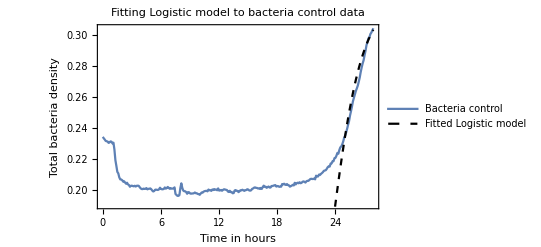

```mathematica
Show[ListLinePlot[ACSIMOI01,PlotLegends->Placed[LineLegend[{"Bacteria control"}],{0.15,0.9}],PlotRange->All],Plot[germGrowth[k,r,t]/.para,{t,20,27.9},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}],PlotRange->All],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to bacteria control data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

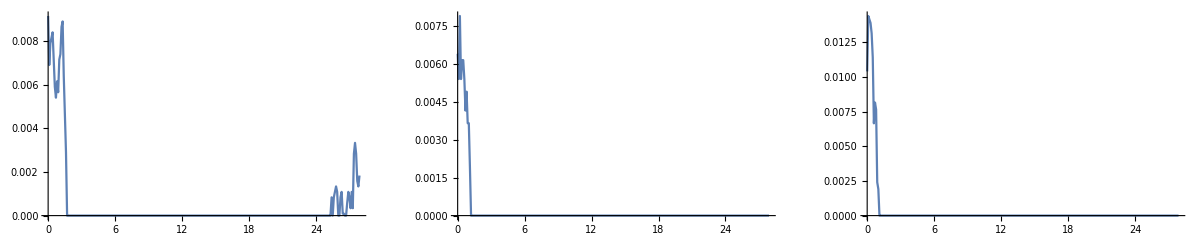

```mathematica
GraphicsGrid[{{ListLinePlot[ACSIMOI01,ImageSize->Large,PlotRange->All],ListLinePlot[ACSIMOI1,ImageSize->Large],ListLinePlot[ACSIMOI10,ImageSize->Large]}},ImageSize->Full]
```

```mathematica
ACSIMOI01NoLag=Select[ACSIMOI01,#[[1]]≥1.2&];
ACSIMOI1NoLag=Select[ACSIMOI1,#[[1]]≥0.7&];
ACSIMOI10NoLag=Select[ACSIMOI10,#[[1]]≥0.1&];
```

```mathematica
fitACSIMOI01[a3_,rab_,k_,t_]:=doublePhageSIMOI01[a3,rab,k][t];
fitModelACSIMOI01=NonlinearModelFit[ACSIMOI01NoLag,{fitACSIMOI01[a3,rab,0.03,t],a3==4.32*10^-7,0.4<rab<0.87},{a3,{rab,0.56}},t];
fitModelACSIMOI01[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.98739, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

{a3→4.32×10^-7,rab→0.400565}

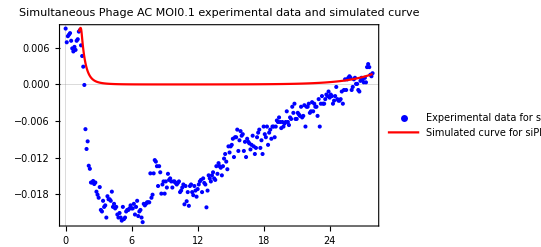

```mathematica
GACSIMOI01=Show[ListPlot[ACSIMOI01Ori,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage AC MOI0.1"},LegendFunction->Framed],{0.5,0.4}],PlotStyle->Blue],Plot[fitModelACSIMOI01[t],{t,1.2,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage AC MOI0.1"},LegendFunction->Framed],{0.5,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage AC MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
8.5*10^-5>a3>0
```

```mathematica
fitACSIMOI1[a3_,rab_,k_,t_]:=doublePhageSIMOI1[a3,rab,k][t];
fitModelACSIMOI1=NonlinearModelFit[ACSIMOI1NoLag,{fitACSIMOI1[a3,rab,k,t],8*10^-6>a3>0,rab==0.6183213675629227,k==0.22},{{a3,7.2*10^-6},k,{rab,0.56}},t]
fitModelACSIMOI1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.69061, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {22.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {22.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {22.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {5.72242×10^-25,99.5,2.86123×10^-25}, is returned.

ParametricNDSolveValue::ndsz: At t == 0.69061, step size is effectively zero; singularity or stiff system suspected.

FittedModel[InterpolatingFunction[…][t]]

{a3→7.2×10^-6,k→0.22,rab→0.618321}

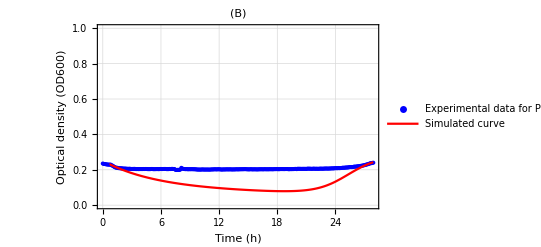

```mathematica
GACSIMOI1=Show[ListPlot[ACSIMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\nPhage LUZ19+E215 MOI1"}],{0.5,0.4}],PlotStyle->Blue,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(B)"],Plot[fitModelACSIMOI1[t],{t,0.7,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.5,0.6}]],Frame->True,ImageSize->Full,PlotRange->{{0,27.9},{0,1}}]
```

```mathematica
Y[t]
doublePhageSIMOI1Full[7.2*^-6,0.6183213675629227,0.4401180885682189]/.t->9
```

{B[t],Bia[t],Bib[t],Ba[t],Bb[t],Bab[t],Pa[t],Pb[t],Bt[t]}

{2.03913×10^-20,0.0242082,0.0955827,1.83528×10^-13,-1.7234×10^-19,2.37546×10^-6,5.99469,2.46047,0.119793}

```mathematica
{2.0391319582628527*^-20,0.0242081571112024,0.09558272169633696,1.8352819638655815*^-13,-1.723401413699491*^-19,2.3754630397544605*^-6,5.994693152100199,2.4604725265151304,0.11979325427076273}
```

```mathematica
{1.5305492656368726*^-13,0.022610326706154718,0.014110067379842679,-5.294385593166595*^-16,5.719597620404973*^-14,1.0691973205923251*^-6,5.405515131615506,5.8941970371867285,0.036721463283527656}
```

ParametricNDSolveValue::ndsz: At t == 0.341342, step size is effectively zero; singularity or stiff system suspected.

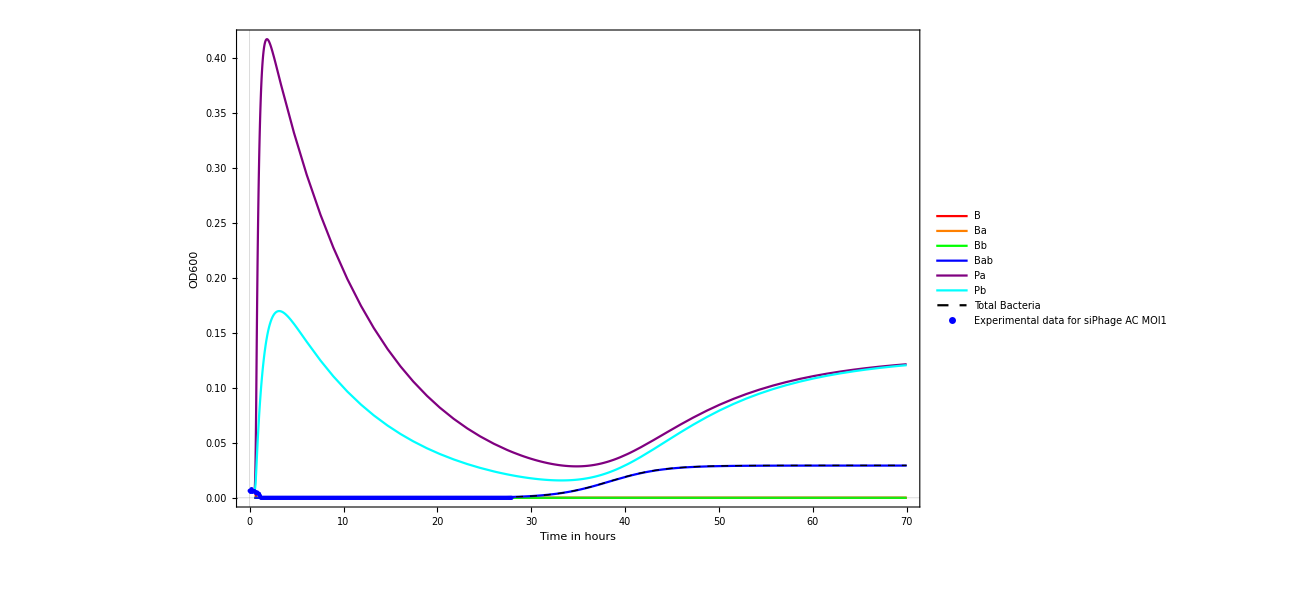

```mathematica
Show[Plot[Evaluate[Through[doublePhageSIMOI1Full[4.32*^-7,0.35490972927709863,0.03][t]]],{t,0.5,70},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.8,0.6}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],ListPlot[ACSIMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage AC MOI1"},LegendFunction->Framed],{0.5,0.4}],PlotStyle->{PointSize[Medium],Blue}]]
```

```mathematica
fitACSIMOI10[a3_,rab_,k_,t_]:=doublePhageSIMOI10[a3,rab,k][t];
fitModelACSIMOI10=NonlinearModelFit[ACSIMOI10NoLag,{fitACSIMOI10[a3,rab,0.03,t],a3==4.32*10^-7,0.48<rab<0.49},{a3,{rab,0.48}},t]
fitModelACSIMOI10[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.0680421, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

ParametricNDSolveValue::ndsz: At t == 0.0680421, step size is effectively zero; singularity or stiff system suspected.

FittedModel[InterpolatingFunction[…][t]]

{a3→4.32×10^-7,rab→0.480489}

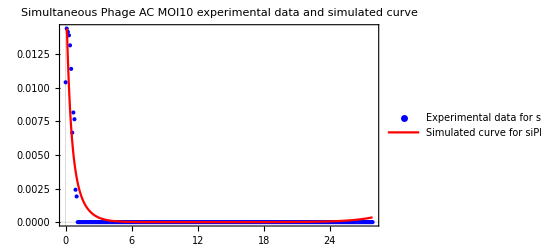

```mathematica
GACSIMOI10=Show[ListPlot[ACSIMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage AC MOI10"},LegendFunction->Framed],{0.5,0.4}],PlotStyle->Blue],Plot[fitModelACSIMOI10[t],{t,0.1,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage AC MOI10"},LegendFunction->Framed],{0.5,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage AC MOI10 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
Mean[{0.40206867556325165,0.40075561131425774,0.4824376384593157}](* old *)
```

0.428421

```mathematica
Mean[{0.40056529834353327,0.35490972927709863,0.4804891622661983}]
```

0.411988

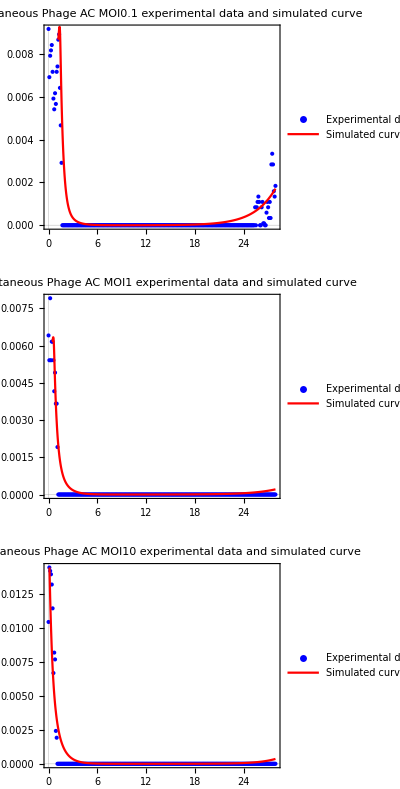

```mathematica
GACSI=GraphicsGrid[{{GACSIMOI01},{GACSIMOI1},{GACSIMOI10}},ImageSize->Full,Alignment->Center,Frame->True]
```

### Phage AC sequential

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+a3*Bab+a1*Ba+a2*Bb,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb-a1*Ba+1/2*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa-a2*Bb+1/2*a1*Bab,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-a3*Bab-a1*Bab,-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-b2*Ba*Pb,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
ACMOI01=Transpose[{TIME,ABData[[13,1]]}];
ACMOI1=Transpose[{TIME,ABData[[14,1]]}];
ACMOI10=Transpose[{TIME,ABData[[15,1]]}];
doublePhageBefore8hMOI1New=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={B0,0,0,0,0,0,B0,0,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.5]=={B0,0,0,0,0,0,B0*0.1,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.5]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{a3,rab,k,B0,u1,u2}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0,u1,u2}];
GraphicsGrid[{{ListLogPlot[{Select[ACMOI1,0.9<=#[[1]]≤3&]},Joined->True,PlotLegends->{"1"},ImageSize->Medium],ListPlot[{Select[ACMOI1,0.9<=#[[1]]≤3&]},PlotLegends->{"1"},ImageSize->Medium]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

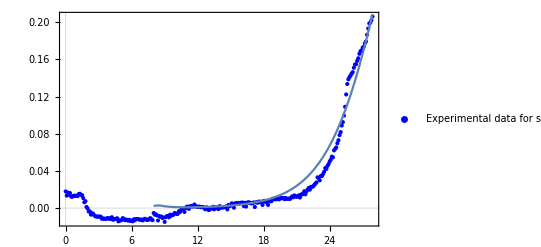

{k→0.599988,r→0.370165,u1→3.00033,u2→5.5}

```mathematica
Remove[ACSEQMOI01Model]
ACSEQMOI01INI=Select[ACMOI01,1.5==#[[1]]&][[1,2]];
ACMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.427,0.57,ACSEQMOI01INI,3,5.5][8]];
ACMOI01H8[[8]]=ACMOI01H8[[8]]+ACSEQMOI01INI*0.1;
ACMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,R,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI01H8},Bt,{t,8,27.9},{k,R,u1,u2}];
ACMOI01FitModel=NonlinearModelFit[Select[ACMOI01,8<=#[[1]]&],{ACMOI01After8h[k,r,u1,u2][t],0.1<k<0.6,3<u1<10,1<u2<10},{k,{r,0.5},u1,u2},t];
Show[ListPlot[ACMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AB MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ACMOI01FitModel[t],{t,8,27.9}]]
ACMOI01FitModel[[1,2]]
```

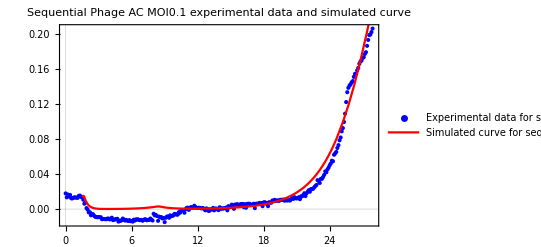

```mathematica
ACSEQMOI01Model[t_]:=doublePhageBefore8hMOI01[4.32*10^-7,0.43,0.6,ACSEQMOI01INI][t]/;1.5<=t<8
ACSEQMOI01Model[t_]:=ACMOI01After8h[0.6,0.43][t]/;t≥8
ACSEQG1=Show[ListPlot[ACMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI0.1"},LegendFunction->Framed],{0.34,0.4}],PlotStyle->Blue],Plot[ACSEQMOI01Model[t],{t,1.5,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage AC MOI0.1"},LegendFunction->Framed],{0.34,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage AC MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

ParametricNDSolveValue::ndsz: At t == 0.890138, step size is effectively zero; singularity or stiff system suspected.

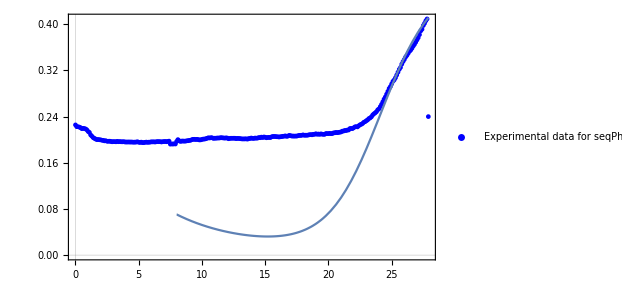

{k→0.467,r→0.48}

```mathematica
Remove[ACSEQMOI1Model]
ACSEQMOI1INI=Select[ACMOI1,0.9==#[[1]]&][[1,2]];
ACMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.48,0.467,ACSEQMOI1INI,1,1][8]];
ACMOI1H8[[8]]=ACMOI1H8[[8]]+ACSEQMOI1INI;
ACMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI1H8},Bt,{t,8,27.9},{k,r,u1,u2}];
ACMOI1After8hNew=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r,u1,u2}];
ACMOI1FitModel=NonlinearModelFit[Select[ACMOI1,8<=#[[1]]&],{ACMOI1After8h[k,r,1,1][t],0.467==k,0.4<r<0.48},{k,{r,0.5}},t];
Show[ListPlot[ACMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ACMOI1FitModel[t],{t,8,27.9}]]
ACMOI1FitModel[[1,2]]
```

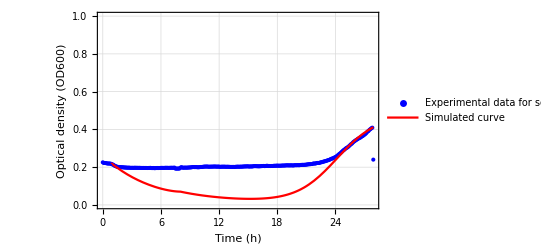

```mathematica
ACSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[4.32*10^-7,0.48,0.467,ACSEQMOI1INI,1,1][t]/;0.9<=t<8
ACSEQMOI1Model[t_]:=ACMOI1After8h[0.467,0.48,1,1][t]/;t≥8
ACSEQG2=Show[ListPlot[ACMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI1"}],{0.25,0.5}],PlotStyle->Blue],Plot[ACSEQMOI1Model[t],{t,0.9,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

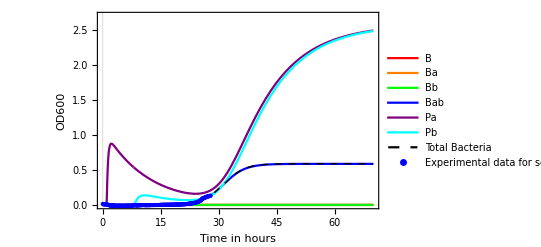

```mathematica
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1New[4.32*10^-7,0.37,0.6,ACSEQMOI1INI,3,10][t]]],{t,0.9,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.8,0.5}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ACMOI1After8hNew[0.6,0.37,3,10][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],ListPlot[ACMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],PlotRange->{{0,70},{0,2.7}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14}]
```

ParametricNDSolveValue::ndsz: At t == 0.46319, step size is effectively zero; singularity or stiff system suspected.

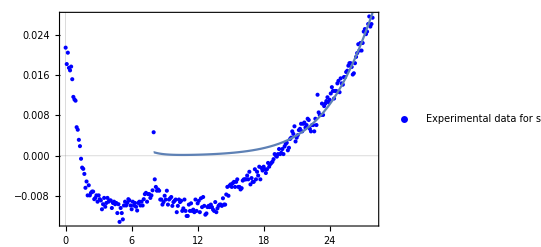

{k→0.082801,r→0.335777,u1→3.19665,u2→5.5}

```mathematica
Remove[ACSEQMOI10Model]
ACSEQMOI10INI=Select[ACMOI10,0.5==#[[1]]&][[1,2]];
ACMOI10H8=Through[doublePhageBefore8hMOI10Full[4.32*10^-7,0.41,0.04,ACSEQMOI10INI,3,5.5][8]];
ACMOI10H8[[8]]=ACMOI10H8[[8]]+ACSEQMOI10INI*10;
ACMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI10H8},Bt,{t,8,27.9},{k,r,u1,u2}];
ACMOI10FitModel=NonlinearModelFit[Select[ACMOI10,8<=#[[1]]&],{ACMOI10After8h[k,r,u1,u2][t],k<0.6,3<u1<10,1<u2<10},{k,{r,0.5},u1,u2},t];
Show[ListPlot[ACMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI10"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[ACMOI10FitModel[t],{t,8,27.9}]]
ACMOI10FitModel[[1,2]]
```

ParametricNDSolveValue::fpct: Too many parameters in {a3,rab,k,B0,u1,u2} to be filled from {4.32×10^-7,0.41,0.046,0.0176636}.

General::stop: Further output of ParametricNDSolveValue::fpct will be suppressed during this calculation.

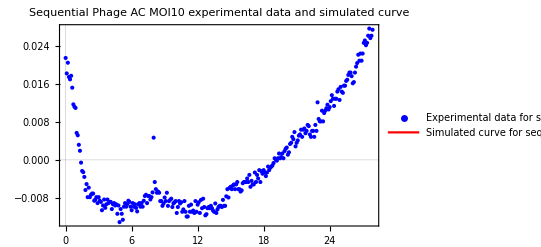

```mathematica
ACSEQMOI10Model[t_]:=doublePhageBefore8hMOI10[4.32*10^-7,0.41,0.046,ACSEQMOI10INI][t]/;0.5<=t<8
ACSEQMOI10Model[t_]:=ACMOI10After8h[0.046,0.41][t]/;t≥8
ACSEQG3=Show[ListPlot[ACMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage AC MOI10"},LegendFunction->Framed],{0.34,0.55}],PlotStyle->Blue],Plot[ACSEQMOI10Model[t],{t,0.5,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage AC MOI10"},LegendFunction->Framed],{0.34,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage AC MOI10 experimental data and simulated curve",ImageSize->Full]
```

```mathematica
Mean[{0.37016511898827376,0.3642262070041008,0.33577666297577197}]
```

0.356723

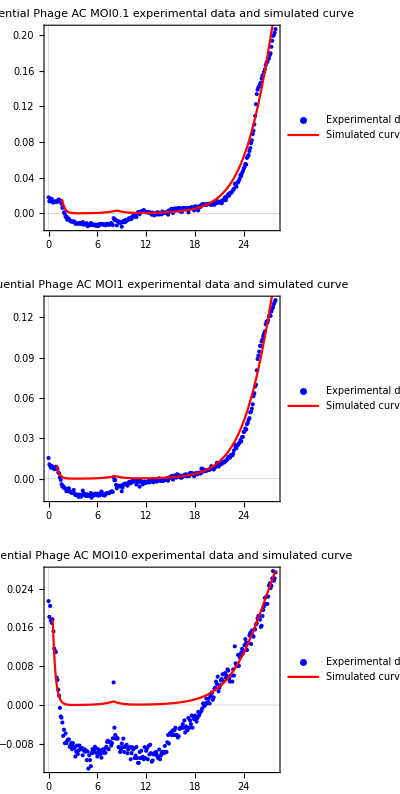

```mathematica
GACSEQ=GraphicsGrid[{{ACSEQG1},{ACSEQG2},{ACSEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

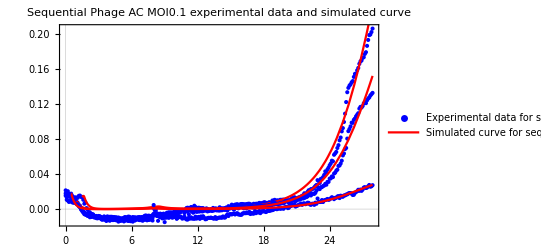

```mathematica
Show[{ACSEQG1,ACSEQG2,ACSEQG3}]
```

### Phage CA sequential

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+1/900*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-20*a2*Ba-b2*Ba*Pb+15*a1*Bab,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-20*a1*Bb-1/800*b1*Bb*Pa+15*a1*Bab,20*a2*Ba+20*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-30*a1*Bab,-0.09*Pa+h*s1*Bia-900*(Pa/(Bb+0.000001))/(450+Pa/(Bb+0.000001))*1/900*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-900*(Pb/(Ba+0.000001))/(450+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-16*a1*Bb-b1*Bb*Pa)+(a2*Ba+16*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
```

```mathematica
FullSimplify[0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-16*a1*Bb-b1*Bb*Pa)+(a2*Ba+16*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))]
```

-1/k 0.877255 (1. B (B+Ba+Bab+Bb-1. k)+0.877738 Ba (B+Ba+Bab+Bb-1. k)+0.923335 Bb (B+Ba+Bab+Bb-1. k)+1.13992 Bab (B+Ba+Bab+Bb-1. k) rab+1.13992 Bia k s1+1.13992 Bib k s2)

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-b1*Bb*Pa,a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.81*Bb*(1-(B+Ba+Bb+Bab)/k)-16*a1*Bb-b1*Bb*Pa)+(a2*Ba+16*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.017,s1->0.19,b1->460,a2->0.005,s2->0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
CAData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
CAMOI01=Transpose[{TIME,CAData[[16,1]]}];
CAMOI1=Transpose[{TIME,CAData[[17,1]]}];
CAMOI10=Transpose[{TIME,CAData[[18,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.8]=={B0,0,0,0,0,0,0,B0*0.1,B0}},Bt,{t,0,27},{a3,rab,k,B0,u2}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.8]=={B0,0,0,0,0,0,0,B0*0.1,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,27},{a3,rab,k,B0,u2}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[2]=={B0,0,0,0,0,0,0,B0,B0}},Bt,{t,0,27},{a3,rab,k,B0,u2}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[2]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,27},{a3,rab,k,B0,u2}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.4]=={B0,0,0,0,0,0,0,B0*10,B0}},Bt,{t,0,27},{a3,rab,k,B0,u2}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.4]=={B0,0,0,0,0,0,0,B0*10,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,27},{a3,rab,k,B0,u2}];
GraphicsGrid[{{ListLogPlot[{Select[CAMOI1,2<=#[[1]]≤3&]},Joined->True,PlotLegends->{"1"},ImageSize->Medium],ListPlot[{Select[CAMOI1,2<=#[[1]]≤5&]},PlotLegends->{"1"},ImageSize->Medium]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[CASEQMOI01Model]
CASEQMOI01INI=Select[CAMOI01,1.8==#[[1]]&][[1,2]];
CAMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.5,0.3,CASEQMOI01INI][8]];
CAMOI01H8[[7]]=CAMOI01H8[[7]]+CASEQMOI01INI*0.1;
CAMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CAMOI01H8},Bt,{t,8,27.9},{k,r}];
```

ParametricNDSolveValue::ndsz: At t == 1.58858, step size is effectively zero; singularity or stiff system suspected.

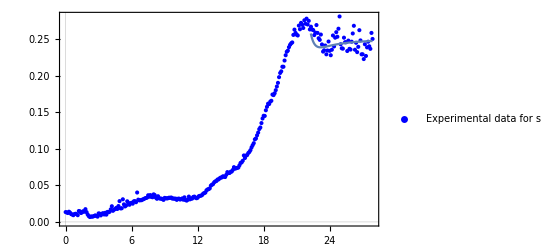

{k→0.248433,r→0.5}

```mathematica
CAMOI01FitModel=NonlinearModelFit[Select[CAMOI01,22<=#[[1]]&],{CAMOI01After8h[k,r][t],0.1<k<0.6,r==0.5},{k,{r,0.5}},t];
Show[ListPlot[CAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[CAMOI01FitModel[t],{t,22,27.9}]]
CAMOI01FitModel[[1,2]]
```

```mathematica
CASEQMOI01Model[t_]:=doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.35,CASEQMOI01INI][t]/;1.8<=t<8
CASEQMOI01Model[t_]:=CAMOI01After8h[0.35,0.46][t]/;t≥8
CASEQG1=Show[ListPlot[CAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI0.1"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[CASEQMOI01Model[t],{t,1.8,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage CA MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage CA MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

-Graphics-

```mathematica
Remove[CASEQMOI1Model]
CASEQMOI1INI=Select[CAMOI1,2==#[[1]]&][[1,2]];
CAMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.88,0.167,CASEQMOI1INI,1][8]];
CAMOI1H8[[7]]=CAMOI1H8[[7]]+CASEQMOI1INI;
CAMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CAMOI1H8},Bt,{t,8,27.9},{k,r,u2}];
```

```mathematica
CAMOI1FitModel=NonlinearModelFit[Select[CAMOI1,8<=#[[1]]&],{CAMOI1After8h[k,r,1][t],0.167<k<0.65,0.88>r>0},{k,{r,0.5}},t];
Show[ListPlot[CAMOI1,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[CAMOI1FitModel[t],{t,8,27.9}]]
CAMOI1FitModel[[1,2]]
```

-Graphics-

{k→0.167,r→0.88}

```mathematica
CASEQMOI1Model[t_]:=doublePhageBefore8hMOI1[4.32*10^-7,0.88,0.167,CASEQMOI1INI,1][t]/;2<=t<8
CASEQMOI1Model[t_]:=CAMOI1After8h[0.167,0.88,1][t]/;t≥8
CASEQG2=Show[ListPlot[CAMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI1"}],{0.25,0.5}],PlotStyle->Blue],Plot[CASEQMOI1Model[t],{t,2,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

-Graphics-

```mathematica
Remove[CASEQMOI10Model]
CASEQMOI10INI=Select[CAMOI10,0.4==#[[1]]&][[1,2]];
CAMOI10H8=Through[doublePhageBefore8hMOI10Full[4.32*10^-7,0.445,0.3,CASEQMOI10INI][8]];
CAMOI10H8[[7]]=CAMOI10H8[[7]]+CASEQMOI10INI*10;
CAMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CAMOI10H8},Bt,{t,8,27.9},{k,r}];
```

```mathematica
CAMOI10FitModel=NonlinearModelFit[Select[CAMOI10,17.2<=#[[1]]&],{CAMOI10After8h[k,r][t],0.1<k<0.6,r<0.5},{k,{r,0.5}},t];
Show[ListPlot[CAMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI10"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[CAMOI10FitModel[t],{t,17.2,27.9}]]
CAMOI10FitModel[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.363371, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

{k→0.127832,r→0.448109}

```mathematica
CASEQMOI10Model[t_]:=doublePhageBefore8hMOI10[4.32*10^-7,0.46,0.3,CASEQMOI10INI][t]/;0.2<=t<8
CASEQMOI10Model[t_]:=CAMOI10After8h[0.2,0.46][t]/;t≥8
CASEQG3=Show[ListPlot[CAMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CA MOI10"},LegendFunction->Framed],{0.25,0.47}],PlotStyle->Blue],Plot[CASEQMOI10Model[t],{t,0.4,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage CA MOI10"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage CA MOI10 experimental data and simulated curve",ImageSize->Full]
```

-Graphics-

```mathematica
Mean[{0.5,0.44,0.45}]
```

0.463333

```mathematica
GCASEQ=GraphicsGrid[{{CASEQG1},{CASEQG2},{CASEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

-Graphics-

#### Estimate rca

```mathematica
BcaGrowth=Select[CAMOI1,20<=#[[1]]&];
ListPlot[BcaGrowth]
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[20]==BcaGrowth[[1,2]]} ,y[t],t][[1,1,2]];
FindFit[BcaGrowth,germGrowth[k,r,t],{{k,0.14},{r,0.4}},t]
```

-Graphics-

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.314275,r→0.118076}

```mathematica
Show[Plot[germGrowth[0.31427465302599367,0.11807598624820771,t],{t,20,27.9},PlotRange->All],ListPlot[BcaGrowth]]
```

-Graphics-

```mathematica
BcaGrowth2=Select[CAMOI10,26.5<=#[[1]]&];
ListPlot[BcaGrowth2]
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[26.5]==BcaGrowth2[[1,2]]} ,y[t],t][[1,1,2]];
FindFit[BcaGrowth2,{germGrowth[k,r,t],r>0.3},{{k,0.14},{r,0.4}},t]
```

-Graphics-

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.143622,r→0.436929}

```mathematica
Show[Plot[germGrowth[0.4,0.43692948205245075,t],{t,26.5,27.9},PlotRange->All],ListPlot[BcaGrowth2]]
```

-Graphics-

```mathematica
(0.11807598624820771+0.43692948205245075)/2
```

0.277503

### Phage BC simultaneous

```mathematica
Remove[DBPH]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+0.8*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,0.8772547720626924*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+0.8*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.005,s1->0.25,b1->460,s2-> 0.02,b2->460,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
BCData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
BCSIMOI01=Replace[Transpose[{TIME,BCData[[19,1]]}],{x_,y_}/;y<0->{x,0},1];
BCSIMOI1=Replace[Transpose[{TIME,BCData[[20,1]]}],{x_,y_}/;y<0->{x,0},1];
BCSIMOI10=Replace[Transpose[{TIME,BCData[[21,1]]}],{x_,y_}/;y<0->{x,0},1];
BCSIMOI01INI=Select[BCSIMOI01,#[[1]]==1.4&][[1,2]];
BCSIMOI1INI=Select[BCSIMOI1,#[[1]]==0.9&][[1,2]];
BCSIMOI10INI=Select[BCSIMOI10,#[[1]]==0&][[1,2]];
doublePhageSIMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.4]=={BCSIMOI01INI,0,0,0,BCSIMOI01INI*0.1,BCSIMOI01INI*0.1,BCSIMOI01INI}},{Bt[t],Pa[t],Pb[t]},{t,0,27.9},{k}];
doublePhageSIMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.9]=={BCSIMOI1INI,0,0,0,BCSIMOI1INI*0.5,BCSIMOI1INI*0.5,BCSIMOI1INI}},{Bt[t],Pa[t],Pb[t]},{t,0,27.9},{k}];
doublePhageSIMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={BCSIMOI10INI,0,0,0,BCSIMOI10INI*10,BCSIMOI10INI*10,BCSIMOI10INI}},{Bt[t],Pa[t],Pb[t]},{t,0,27.9},{k}];
GraphicsGrid[{{ListLogPlot[{Select[BCSIMOI1,0.9<=#[[1]]≤5&]},Joined->True,PlotLegends->{"1"},ImageSize->Medium],ListPlot[{Select[BCSIMOI1,1<=#[[1]]≤5&]},PlotLegends->{"1"},ImageSize->Medium,PlotRange->All]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListLinePlot[BCSIMOI01,ImageSize->Large,PlotRange->All],ListLinePlot[BCSIMOI1,ImageSize->Large],ListLinePlot[BCSIMOI10,ImageSize->Large]}},ImageSize->Full]
```

-Graphics-

```mathematica
GBCSIMOI01=Show[ListPlot[BCSIMOI01,PlotRange->{{0,27.9},{0,0.8}},PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage BC MOI0.1"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[doublePhageSIMOI01[0.635][[1]],{t,1.4,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage BC MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage BC MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

-Graphics-

```mathematica
Remove[A,B]
```

```mathematica
GBCSIMOI1=Show[ListPlot[BCSIMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\nPhage PYO2+E215 MOI1"}],{0.25,0.6}],PlotStyle->Blue,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(C)"],Plot[doublePhageSIMOI1[0.825][[1]],{t,0.9,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.8}]],Frame->True,ImageSize->Full,PlotRange->{{0,27.9},{0,1}}]
```

-Graphics-

```mathematica
Plot[doublePhageSIMOI1[0.9][[1]],{t,0,27.9},PlotStyle->Red,PlotRange->{{0,27.9},{0,1.1}},PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.8}],ImageSize->Full]
```

-Graphics-

```mathematica
GBCSIMOI10=Show[ListPlot[BCSIMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Experimental data for\nsiPhage BC MOI10"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[doublePhageSIMOI10[0.76][[1]],{t,0,27.9},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLegends->Placed[LineLegend[{"Simulated curve for\nsiPhage BC MOI10"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},PlotLabel->"Simultaneous Phage BC MOI10 experimental data and simulated curve",ImageSize->Full]
```

-Graphics-

```mathematica
GBCSI=GraphicsGrid[{{GBCSIMOI01},{GBCSIMOI1},{GBCSIMOI10}},ImageSize->Full,Alignment->Center,Frame->True]
```

-Graphics-

### Phage BC sequential

```mathematica
(* 需要数据支持 *)
```

```mathematica
Remove[DBPH]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
BCData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
BCMOI01=Transpose[{TIME,BCData[[22,1]]}];
BCMOI1=Transpose[{TIME,BCData[[23,1]]}];
BCMOI10=Transpose[{TIME,BCData[[24,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.9]=={B0,0,0,0,B0*0.1,0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.9]=={B0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.6]=={B0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.6]=={B0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];GraphicsGrid[{{ListLogPlot[{Select[BCMOI1,1.3<=#[[1]]≤3&]},Joined->True,PlotLegends->{"1"},ImageSize->Medium],ListPlot[{Select[BCMOI1,1.3<=#[[1]]≤3&]},PlotLegends->{"1"},ImageSize->Medium]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[BCSEQMOI01Model]
BCSEQMOI01INI=Select[BCMOI01,1.9==#[[1]]&][[1,2]];
BCMOI01H8=Through[doublePhageBefore8hMOI01Full[0.668,BCSEQMOI01INI][8]];
BCMOI01H8[[6]]=BCMOI01H8[[6]]+BCSEQMOI01INI*0.1;
BCMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BCMOI01H8},Bt,{t,8,27.9},{k}];
BCSEQMOI01Model[t_]:=doublePhageBefore8hMOI01[0.668,BCSEQMOI01INI][t]/;1.9<=t<8
BCSEQMOI01Model[t_]:=BCMOI01After8h[0.668][t]/;t≥8
BCSEQG1=Show[ListPlot[BCMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BC MOI0.1"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[BCSEQMOI01Model[t],{t,1.9,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage BC MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage BC MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

ParametricNDSolveValue::ndsz: At t == 1.73689, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
Remove[BCSEQMOI1Model]
BCSEQMOI1INI=0.2;
BCMOI1H8=Through[doublePhageBefore8hMOI1Full[0.9,BCSEQMOI1INI][8]];
BCMOI1H8[[6]]=BCMOI1H8[[6]]+BCSEQMOI1INI;
BCMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BCMOI1H8},Bt,{t,8,27.9},{k}];
BCSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[0.9,BCSEQMOI1INI][t]/;t<8
BCSEQMOI1Model[t_]:=BCMOI1After8h[0.9][t]/;t≥8
BCSEQG2=Show[ListPlot[BCMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BC MOI1"}],{0.25,0.5}],PlotStyle->Blue],Plot[BCSEQMOI1Model[t],{t,0,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

-Graphics-

```mathematica
Remove[DBPH]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,B0,0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
BCSEQMOI1INI=0.2;
BCMOI1H8=Through[doublePhageBefore8hMOI1Full[0.9,BCSEQMOI1INI][8]];
BCMOI1H8[[6]]=BCMOI1H8[[6]]+BCSEQMOI1INI;
BCMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BCMOI1H8},Bt,{t,8,27.9},{k}];
BCSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[0.9,BCSEQMOI1INI][t]/;t<8
BCSEQMOI1Model[t_]:=BCMOI1After8h[0.9][t]/;t≥8
```

```mathematica
doublePhageBefore8hMOI1[]
```

```mathematica
Plot[BCSEQMOI1Model[t],{t,0,27.9},PlotRange-> {{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage PYO2→E215 treatment"}],{0.3,0.8}],ImageSize->Full,PlotLabel->"(E)"]
```

-Graphics-

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\pyo2_e215.png",Plot[BCSEQMOI1Model[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#FBBE7F"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\pyo2_e215.png

```mathematica
Remove[BCSEQMOI10Model]
BCSEQMOI10INI=Select[BCMOI10,0.6==#[[1]]&][[1,2]];
BCMOI10H8=Through[doublePhageBefore8hMOI10Full[0.63,BCSEQMOI10INI][8]];
BCMOI10H8[[6]]=BCMOI10H8[[6]]+BCSEQMOI10INI*10;
BCMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BCMOI10H8},Bt,{t,8,27.9},{k}];
BCSEQMOI10Model[t_]:=doublePhageBefore8hMOI10[0.63,BCSEQMOI10INI][t]/;0.6<=t<8
BCSEQMOI10Model[t_]:=BCMOI10After8h[0.63][t]/;t≥8
BCSEQG3=Show[ListPlot[BCMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BC MOI10"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[BCSEQMOI10Model[t],{t,0.6,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage BC MOI10"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage BC MOI10 experimental data and simulated curve",ImageSize->Full]
```

ParametricNDSolveValue::ndsz: At t == 0.54543, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
GBCSEQ=GraphicsGrid[{{BCSEQG1},{BCSEQG2},{BCSEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

-Graphics-

### Phage CB sequential

```mathematica
Remove[DBPH]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
CBData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
CBMOI01=Transpose[{TIME,CBData[[25,1]]}];
CBMOI1=Transpose[{TIME,CBData[[26,1]]}];
CBMOI10=Transpose[{TIME,CBData[[27,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.9]=={B0,0,0,0,0,B0*0.1,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.9]=={B0,0,0,0,0,B0*0.1,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0*10,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0*10,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
GraphicsGrid[{{ListLogPlot[{Select[CBMOI1,2<=#[[1]]≤5&]},Joined->True,PlotLegends->{"0.1","1","10"},ImageSize->Medium],ListLinePlot[{Select[CBMOI1,2<=#[[1]]≤5&]},PlotLegends->{"0.1","1","10"},ImageSize->Medium]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[CBSEQMOI01Model]
CBSEQMOI01INI=Select[CBMOI01,1.9==#[[1]]&][[1,2]];
CBMOI01H8=Through[doublePhageBefore8hMOI01Full[0.57,CBSEQMOI01INI][8]];
CBMOI01H8[[5]]=CBMOI01H8[[5]]+CBSEQMOI01INI*0.1;
CBMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CBMOI01H8},Bt,{t,8,27.9},{k}];
CBSEQMOI01Model[t_]:=doublePhageBefore8hMOI01[0.57,CBSEQMOI01INI][t]/;1.9<=t<8
CBSEQMOI01Model[t_]:=CBMOI01After8h[0.57][t]/;t≥8
CBSEQG1=Show[ListPlot[CBMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CB MOI0.1"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[CBSEQMOI01Model[t],{t,1.9,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage CB MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage CB MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

ParametricNDSolveValue::ndsz: At t == 1.65838, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
Remove[CBSEQMOI1Model]
CBSEQMOI1INI=0.2;
CBMOI1H8=Through[doublePhageBefore8hMOI1Full[0.9,CBSEQMOI1INI][8]];
CBMOI1H8[[5]]=CBMOI1H8[[5]]+CBSEQMOI1INI;
CBMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CBMOI1H8},Bt,{t,8,27.9},{k}];
CBSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[0.9,CBSEQMOI1INI][t]/;t<8
CBSEQMOI1Model[t_]:=CBMOI1After8h[0.9][t]/;t≥8
CBSEQG2=Show[ListPlot[CBMOI1,PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CB MOI1"}],{0.25,0.5}],PlotStyle->Blue],Plot[CBSEQMOI1Model[t],{t,0,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.25,0.7}]],Frame->True,ImageSize->Full,PlotRange-> {{0,27.9},{0,1}}]
```

-Graphics-

```mathematica
Plot[CBSEQMOI1Model[t],{t,0,27.9},PlotRange-> {{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage E215→PYO2 treatment"}],{0.7,0.25}],ImageSize->Full,PlotLabel->"(F)"]
```

```mathematica
Remove[DBPH]
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValuesAB={a1->0.0119,s1->0.178,b1->382,s2-> 0.0506,b2->382,h->100};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]]
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0,B0}},Bt,{t,0,10},{k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,B0,B0}},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,10},{k,B0}];
CBSEQMOI1INI=0.2;
CBMOI1H8=Through[doublePhageBefore8hMOI1Full[0.9,CBSEQMOI1INI][8]];
CBMOI1H8[[5]]=CBMOI1H8[[5]]+CBSEQMOI1INI;
CBMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CBMOI1H8},Bt,{t,8,27.9},{k}];
CBSEQMOI1Model[t_]:=doublePhageBefore8hMOI1[0.9,CBSEQMOI1INI][t]/;t<8
CBSEQMOI1Model[t_]:=CBMOI1After8h[0.9][t]/;t≥8
```

{B[t],Bia[t],Bib[t],Br[t],Pa[t],Pb[t],Bt[t]}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\e215_pyo2.png",Plot[CBSEQMOI1Model[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#726CAF"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\e215_pyo2.png

```mathematica
Remove[CBSEQMOI10Model]
CBSEQMOI10INI=Select[CBMOI10,0==#[[1]]&][[1,2]];
CBMOI10H8=Through[doublePhageBefore8hMOI10Full[0.635,CBSEQMOI10INI][8]];
CBMOI10H8[[5]]=CBMOI10H8[[5]]+CBSEQMOI10INI*10;
CBMOI10After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CBMOI10H8},Bt,{t,8,27.9},{k}];
CBSEQMOI10Model[t_]:=doublePhageBefore8hMOI10[0.635,CBSEQMOI10INI][t]/;0<=t<8
CBSEQMOI10Model[t_]:=CBMOI10After8h[0.635][t]/;t≥8
CBSEQG3=Show[ListPlot[CBMOI10,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage CB MOI10"},LegendFunction->Framed],{0.25,0.4}],PlotStyle->Blue],Plot[CBSEQMOI10Model[t],{t,0,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage CB MOI10"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage CA MOI10 experimental data and simulated curve",ImageSize->Full]
```

-Graphics-

```mathematica
GCBSEQ=GraphicsGrid[{{CBSEQG1},{CBSEQG2},{CBSEQG3}},ImageSize->Full,Alignment->Center,Frame->True]
```

-Graphics-

### Comparison of simultaneous therapies

#### Simulations

```mathematica
GraphicsGrid[{{GABSI,GACSI,GBCSI}},ImageSize->Full,Frame->True]
```

-Graphics-

#### growth rates

```mathematica
rates=TableForm[{{"rab",0.46},{"rac",0.41},{"rbc",0.78}}]
```

rab | 0.46
rac | 0.41
rbc | 0.78

```mathematica
A=1
B=2
```

1

2

```mathematica
{{-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
GraphicsGrid[{{ListPlot[ABSIMOI1,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\n Phage A+B MOI1"}],{0.5,0.4}],PlotStyle->Blue,PlotRange->{{0,27.9},{0,1}},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(A)",ImageSize->Full],ListPlot[ACSIMOI1,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\n Phage A+C MOI1"}],{0.5,0.4}],PlotStyle->Blue,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(B)",ImageSize->Full,PlotRange->{{0,27.9},{0,1}}],ListPlot[BCSIMOI1,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Experimental data for\n Phage B+C MOI1"}],{0.25,0.6}],PlotStyle->Blue,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(C)",ImageSize->Full,PlotRange->{{0,27.9},{0,1}}]}},Alignment->Center,Spacings->0]
```

-Graphics-

```mathematica
GraphicsGrid[{{GABSIMOI1,GACSIMOI1,GBCSIMOI1}},ImageSize->Full,Spacings->0,Alignment->Center]
```

-Graphics-

```mathematica
{{-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
A=1
B=2
F=3
```

1

2

3

```mathematica
{{(A), (B)}, {-Graphics-, -Graphics-}, {(C), (D)}, {-Graphics-, -Graphics-}, {(E), (F)}, {-Graphics-, -Graphics-}}
```

### Comparison of sequential therapies

```mathematica
GraphicsGrid[{{GABSEQ,GACSEQ,GBCSEQ},{GBASEQ,GCASEQ,GCBSEQ}},ImageSize->Full,Frame->True]
```

-Graphics-

### No data simulation

#### Growth rates estimation

```mathematica
cocktail_growth_data.xlsx
```

```mathematica
cocktailData =Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\data_final\\cocktail_growth_data.xlsx"];
TIME=Table[i,{i,0,18,0.1}];
ABResistantGrowthData=Transpose[{TIME,cocktailData[[1,1]]}];
ACResistantGrowthData=Transpose[{TIME,cocktailData[[2,1]]}];
BCResistantGrowthData=Transpose[{TIME,cocktailData[[3,1]]}];
```

```mathematica
ListLogPlot[Select[ABResistantGrowthData,#[[1]]>=3&]]
ListLogPlot[Select[ACResistantGrowthData,#[[1]]>=3&]]
ListLogPlot[Select[BCResistantGrowthData,#[[1]]>=3&]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Mean[Select[ABResistantGrowthData,18>=#[[1]]>=17&][[All,2]]]
```

0.931214

```mathematica
noLagAB=Select[ABResistantGrowthData,#[[1]]>=3&];
initialAB=Select[ABResistantGrowthData,#[[1]]==3&][[1,2]]
noLagAC=Select[ACResistantGrowthData,#[[1]]>=3&];
initialAC=Select[ACResistantGrowthData,#[[1]]==3&][[1,2]]
noLagBC=Select[BCResistantGrowthData,#[[1]]>=4&];
initialBC=Select[BCResistantGrowthData,#[[1]]==4&][[1,2]]
```

0.272271

0.22251

0.365965

```mathematica
Remove[germGrowth,germGrowth2]
```

```mathematica
germGrowth[k_,r_,t_,initial_]:=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==initial} ,y[t],t][[1,1,2]];
```

```mathematica
germGrowth2[k_,r_,t_,initial_]:=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4]==initial} ,y[t],t][[1,1,2]];
```

```mathematica
paraAB=FindFit[noLagAB,{germGrowth[k,r,t,initialAB],0.88>r>0.54,k>0.9},{{k,0.9},{r,0.88}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.9,r→0.54}

```mathematica
paraAB=NonlinearModelFit[noLagAB,{germGrowth[0.9,r,t,initialAB],0.88>r>0.54},{{r,0.88}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.9 2.71828^(0.54 t))/(11.6501+1. 2.71828^(0.54 t))]

```mathematica
paraAB["ParameterTable"]
paraAB["ParameterConfidenceIntervalTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
r | 0.54 | 0.00907077 | 59.5319 | 2.92588×10^-106

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
r | 0.54 | 0.00907077 | {0.522077,0.557923}

```mathematica
0.5400000842075531-0.5220770921744337
```

0.017923

```mathematica
paraAC=FindFit[noLagAC,{germGrowth[k,r,t,initialAC],0.88>r>0.5,1.1>k>0},{{k,0.9},{r,0.88}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.678533,r→0.618322}

```mathematica
paraAC=NonlinearModelFit[noLagAC,{germGrowth[0.67853,r,t,initialAC],0.88>r>0.5},{{r,0.88}},t]
```

FittedModel[(0.67853 ⅇ^(0.618328 t))/(13.0992+1. ⅇ^(0.618328 t))]

```mathematica
paraAC["ParameterTable"]
paraAC["ParameterConfidenceIntervalTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
r | 0.618328 | 0.0088399 | 69.9473 | 2.12423×10^-116

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
r | 0.618328 | 0.0088399 | {0.600861,0.635795}

```mathematica
0.6183277352944918-0.6008609222058129
```

0.0174668

```mathematica
paraBC=FindFit[noLagBC,{germGrowth2[k,r,t,initialBC],0.88>r>0.81,1.2>k>1.04},{{k,0.9},{r,0.88}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→1.04,r→0.81}

```mathematica
paraBC=NonlinearModelFit[noLagBC,{germGrowth2[1.04,r,t,initialBC],0.88>r>0.81},{{r,0.88}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(1.04 2.71828^(0.81 t))/(47.0281+1. 2.71828^(0.81 t))]

```mathematica
paraBC["ParameterTable"]
paraBC["ParameterConfidenceIntervalTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
r | 0.81 | 0.0478546 | 16.9263 | 1.11616×10^-35

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
r | 0.81 | 0.0478546 | {0.715389,0.904611}

```mathematica
0.8100000543778404-0.7153889588147097
```

0.0946111

```mathematica
Remove[A,B,C,D]
```

Remove::rmptc: Symbol C is Protected and cannot be removed.

Remove::rmptc: Symbol D is Protected and cannot be removed.

```mathematica
ABfit=Show[ListPlot[ABResistantGrowthData,PlotLegends->Placed[LineLegend[{"Phage LUZ19+PYO2-resistant\nbacteria growth data"}],{0.7,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->All],Plot[Evaluate[germGrowth[k,r,t,initialAB]/.paraAB],{t,3,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.7,0.35}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(A)"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

```mathematica
ACfit=Show[ListPlot[ACResistantGrowthData,PlotLegends->Placed[LineLegend[{"Phage LUZ19+E215-resistant\nbacteria growth data"}],{0.7,0.4}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->All],Plot[Evaluate[germGrowth[k,r,t,initialAC]/.paraAC],{t,3,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.7,0.27}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(B)"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

```mathematica
{{(A), (B)}, {-Graphics-, -Graphics-}}
```

```mathematica
BCfit=Show[ListPlot[BCResistantGrowthData,PlotLegends->Placed[LineLegend[{"Phage PYO2+E215-resistant\nbacteria growth data"}],{0.7,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->All],Plot[Evaluate[germGrowth2[k,r,t,initialBC]/.paraBC],{t,4,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.7,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(C)"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

```mathematica
{{-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
GraphicsGrid[{{ABfit,ACfit,BCfit}},Spacings->0,Alignment->Center,ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListPlot[ABResistantGrowthData,PlotLegends->Placed[LineLegend[{"PhageAB-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(A)"],ListPlot[ACResistantGrowthData,PlotLegends->Placed[LineLegend[{"PhageAC-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(B)"],ListPlot[BCResistantGrowthData,PlotLegends->Placed[LineLegend[{"PhageBC-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,20},{0,1.1}},PlotLabel->"(C)"]}},Alignment->Center,Spacings->0]
```

-Graphics-

#### Phage AB sequential

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2->0.178,b2->382,h->100,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{rab,k,B0}];
(* B0 = 0.2, k = 0.9*)
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[luz19pyo2r*0.9,0.9,0.2][8]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI1H8},Bt,{t,8,27.9},{rab,k}];
modelAB[t_]:=doublePhageBefore8hMOI1[luz19pyo2r*0.9,0.9,0.2][t]/;t<=8
modelAB[t_]:=ABMOI1After8h[luz19pyo2r*0.9,0.9][t]/;t>8
```

```mathematica
Through[doublePhageBefore8hMOI1Full[0.486,0.9,0.2][7]]
```

{4.87334×10^-13,0.0537807,0.,0.0121439,3.47805×10^-16,0.00018816,10.3214,0.,0.0661127}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\luz19_pyo2.png",Plot[modelAB[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#EF6A8D"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\luz19_pyo2.png

```mathematica
GabNoData=Plot[modelAB[t],{t,0,27.9},PlotRange->{{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage LUZ19→PYO2 treatment"}],{0.35,0.7}],ImageSize->Full,PlotLabel->"(A)"]
```

-Graphics-

```mathematica
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\doublePhageNew.xlsx"];
ABMOI01=Transpose[{TIME,ABData[[1,1]]}];
ABMOI1=Transpose[{TIME,ABData[[2,1]]}];
ABMOI10=Transpose[{TIME,ABData[[3,1]]}];
```

```mathematica
Show[GabNoData,ListPlot[ABMOI1]]
```

-Graphics-

#### Phage BA sequential

```mathematica
Remove[DBPH,A,B]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2->0.178,b2->382,h->100,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},Bt,{t,0,10},{rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{rab,k,B0}];
(* B0 = 0.2, k = 0.9*)
BAMOI1H8=Through[doublePhageBefore8hMOI1Full[luz19pyo2r,0.9,0.2][8]];
BAMOI1H8[[7]]=BAMOI1H8[[7]]+0.2;
BAMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI1H8},Bt,{t,8,27.9},{rab,k}];
modelBA[t_]:=doublePhageBefore8hMOI1[luz19pyo2r,0.9,0.2][t]/;t<=8
modelBA[t_]:=BAMOI1After8h[luz19pyo2r,0.9][t]/;t>8
```

```mathematica
Through[doublePhageBefore8hMOI1Full[0.5,0.9,0.2][7]]
```

{-4.91584×10^-9,0.,0.0353417,-1.03775×10^-11,0.00384895,0.000199603,0.,11.3566,0.0393903}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\pyo2_luz19.png",Plot[modelBA[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#6BCBF2"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\pyo2_luz19.png

```mathematica
Plot[modelBA[t],{t,0,27.9},PlotRange->{{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage PYO2→LUZ19 treatment"}],{0.35,0.7}],ImageSize->Full,PlotLabel->"(B)"]
```

-Graphics-

#### Phage AC sequential

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{rab,k,B0}];
ACMOI1H8=Through[doublePhageBefore8hMOI1Full[0.556,0.9,0.2][8]];
ACMOI1H8[[8]]=ACMOI1H8[[8]]+0.2;
ACMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ACMOI1H8},Bt,{t,8,27.9},{rab,k}];
modelAC[t_]:=doublePhageBefore8hMOI1[0.556,0.9,0.2][t]/;t<=8
modelAC[t_]:=ACMOI1After8h[0.556,0.9][t]/;t>8
```

```mathematica
Through[doublePhageBefore8hMOI1Full[0.556,0.9,0.2][0.1]]
```

{0.0000921751,0.199427,0.,0.0000627816,4.59464×10^-8,5.72298×10^-8,0.311416,0.,0.199582}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\luz19_e215.png",Plot[modelAC[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#F5F08A"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\luz19_e215.png

```mathematica
GacNoData=Plot[modelAC[t],{t,0,27.9},PlotRange->{{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,FrameLabel->{"Time (h)","Optical density (OD600)"},BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage LUZ19→E215 treatment"}],{0.35,0.7}],ImageSize->Full,PlotLabel->"(C)"]
```

-Graphics-

#### Phage CA sequential

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},Bt,{t,0,10},{rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{rab,k,B0}];
CAMOI1H8=Through[doublePhageBefore8hMOI1Full[0.618,0.9,0.2][8]];
CAMOI1H8[[7]]=CAMOI1H8[[7]]+0.2;
CAMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==CAMOI1H8},Bt,{t,8,27.9},{rab,k}];
modelCA[t_]:=doublePhageBefore8hMOI1[0.618,0.9,0.2][t]/;t<=8
modelCA[t_]:=CAMOI1After8h[0.618,0.9][t]/;t>8
```

```mathematica
Through[doublePhageBefore8hMOI1Full[0.618,0.9,0.2][0.1]]
```

{0.00861022,0.,0.194703,0.0000145738,0.0000242388,7.53622×10^-8,0.,0.0669688,0.203352}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\e215_luz19.png",Plot[modelCA[t],{t,0,27},
PlotRange->{{0,27},{0,1}},
PlotStyle->{RGBColor["#9BCB52"],AbsoluteThickness[5]},
PlotTheme->"Detailed",
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
AspectRatio->1,
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
ImageSize->800]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\e215_luz19.png

```mathematica
GacNoData=Plot[modelCA[t],{t,0,27.9},PlotRange->{{0,27.9},{0,1.1}},PlotStyle->Red,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameLabel->{"Time (h)","Optical density (OD600)"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Simulated curve:\nphage E215→LUZ19 treatment"}],{0.35,0.7}],ImageSize->Full,PlotLabel->"(D)"]
```

-Graphics-

#### Phage BC sequential

#### Phage CB sequential

#### Simultaneous

```mathematica
GraphicsGrid[{{GABSIMOI1,GACSIMOI1,GBCSIMOI1}},Spacings->0,Alignment->Center]
```

-Graphics-

```mathematica
{{(A), (B), (C)}, {-Graphics-, -Graphics-, -Graphics-}}
```

#### Sequential

```mathematica
A=1
B=2
F=3
```

1

2

3

```mathematica
{{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}}
```

```mathematica
{{(A), (B)}, {-Graphics-, -Graphics-}, {(C), (D)}, {-Graphics-, -Graphics-}, {(E), (F)}, {-Graphics-, -Graphics-}}
```

#### Growth

```mathematica
A=1
B=2
F=3
G=4
```

1

2

3

4

```mathematica
{{□, (A), □}, {□, -Graphics-, □}, {(B), (C), (D)}, {-Graphics-, -Graphics-, -Graphics-}, {(E), (F), (G)}, {-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
GraphicsGrid[{{Afit,Bfit,Cfit}},Alignment->Center,Spacings->0]
```

-Graphics-

```mathematica
GraphicsGrid[{{ABfit,ACfit,BCfit}},Alignment->Center,Spacings->0]
```

-Graphics-

```mathematica
GraphicsGrid[{{Anfit},{Afit,Bfit,Cfit},{ABfit,ACfit,BCfit}},Alignment->Center,Spacings->0]
```

-Graphics-

## Back mutation

### Phage AB sequential without back mutation: System evolution

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-2*a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-10*a1*Bb-b1*Bb*Pa,2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia,-0.09*Pb+h*s2*Bib,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-2*a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-10*a1*Bb-b1*Bb*Pa)+(2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.01,s2-> 2.3,b2->277,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\simulation\\doublePhage.xlsx"];
ABMOI01=Transpose[{TIME,ABData[[1,1]]}];
ABMOI1=Transpose[{TIME,ABData[[2,1]]}];
ABMOI10=Transpose[{TIME,ABData[[3,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Ba,Bb,Bab,Pa,Pb},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
GraphicsGrid[{{ListLogPlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},Joined->True,PlotLegends->{"0.1","1","10"},ImageSize->Large],ListLinePlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},PlotLegends->{"0.1","1","10"},ImageSize->Large]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[ABSEQMOI01Model]
ABSEQMOI01INI=Select[ABMOI01,1.3==#[[1]]&][[1,2]];
ABMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][8]];
ABMOI01H8[[8]]=ABMOI01H8[[8]]+ABSEQMOI01INI*0.1;
ABMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,0.46,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI01H8},{B,Ba,Bb,Bab,Pa,Pb},{t,8,100},{k}];
ABSEQMOI01Model[t_]:=Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]/;1.3<=t<8;
ABSEQMOI01Model[t_]:=Through[ABMOI01After8h[0.11][t]]/;t≥8;
```

ParametricNDSolveValue::ndsz: At t == 1.15292, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]],{t,1.3,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb"},LegendFunction->Framed],{0.8,0.4}],PlotTheme->"Scientific",BaseStyle->{Bold,9}],Plot[Evaluate[Through[ABMOI01After8h[0.11][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9}],PlotRange->{{0,70},{0,0.5}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9}]
```

ParametricNDSolveValue::ndsz: At t == 1.15292, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

### Phage AB sequential with back mutation: System evolution

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+2*a2*Ba+10*a1*Bb+10*a3*Bab,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-4*a2*Ba-b2*Ba*Pb+10*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-20*a1*Bb-b1*Bb*Pa+10*a1*Bab,2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-20*a1*Bab-10*a3*Bab,-0.09*Pa+h*s1*Bia,-0.09*Pb+h*s2*Bib,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+2*a2*Ba+10*a1*Bb+10*a3*Bab-s1*Bia+b1*B*Pa+b1*Bb*Pa-s2*Bib+b2*B*Pb+b2*Ba*Pb+a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-4*a2*Ba-b2*Ba*Pb+10*a1*Bab+a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-20*a1*Bb-b1*Bb*Pa+10*a1*Bab+2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-20*a1*Bab-10*a3*Bab};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\simulation\\doublePhage.xlsx"];
ABMOI01=Transpose[{TIME,ABData[[1,1]]}];
ABMOI1=Transpose[{TIME,ABData[[2,1]]}];
ABMOI10=Transpose[{TIME,ABData[[3,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Ba,Bb,Bab,Pa,Pb},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
GraphicsGrid[{{ListLogPlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},Joined->True,PlotLegends->{"0.1","1","10"},ImageSize->Large],ListLinePlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},PlotLegends->{"0.1","1","10"},ImageSize->Large]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[ABSEQMOI01Model]
ABSEQMOI01INI=Select[ABMOI01,1.3==#[[1]]&][[1,2]];
ABMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][8]];
ABMOI01H8[[8]]=ABMOI01H8[[8]]+ABSEQMOI01INI*0.1;
ABMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,0.46,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI01H8},{B,Ba,Bb,Bab,Pa,Pb},{t,8,100},{k}];
ABSEQMOI01Model[t_]:=Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]/;1.3<=t<8;
ABSEQMOI01Model[t_]:=Through[ABMOI01After8h[0.11][t]]/;t≥8;
```

ParametricNDSolveValue::ndsz: At t == 1.15292, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]],{t,1.3,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb"},LegendFunction->Framed],{0.8,0.4}],PlotTheme->"Scientific",BaseStyle->{Bold,9}],Plot[Evaluate[Through[ABMOI01After8h[0.11][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9}],PlotRange->{{0,70},{0,10}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9}]
```

ParametricNDSolveValue::ndsz: At t == 1.15292, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

## Re-absorption

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-2*a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-10*a1*Bb-b1*Bb*Pa,2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-2*a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-10*a1*Bb-b1*Bb*Pa)+(2*a2*Ba+10*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.01,s2-> 2.3,b2->277,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
TIME=Table[i,{i,0,27.9,0.1}];
ABData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\simulation\\doublePhage.xlsx"];
ABMOI01=Transpose[{TIME,ABData[[1,1]]}];
ABMOI1=Transpose[{TIME,ABData[[2,1]]}];
ABMOI10=Transpose[{TIME,ABData[[3,1]]}];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Ba,Bb,Bab,Pa,Pb},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.3]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.8]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},Bt,{t,0,10},{a3,rab,k,B0}];
doublePhageBefore8hMOI10Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0.5]=={B0,0,0,0,0,0,B0*10,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
GraphicsGrid[{{ListLogPlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},Joined->True,PlotLegends->{"0.1","1","10"},ImageSize->Large],ListLinePlot[{Select[ABMOI01,1.3<=#[[1]]≤3&],Select[ABMOI1,0.8<=#[[1]]≤3&],Select[ABMOI10,0.5<=#[[1]]≤3&]},PlotLegends->{"0.1","1","10"},ImageSize->Large]}},ImageSize->Full,Alignment->Center,Spacings->100]
```

-Graphics-

```mathematica
Remove[ABSEQMOI01Model]
ABSEQMOI01INI=Select[ABMOI01,1.3==#[[1]]&][[1,2]];
ABMOI01H8=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][8]];
ABMOI01H8[[8]]=ABMOI01H8[[8]]+ABSEQMOI01INI*0.1;
ABMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,0.46,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==ABMOI01H8},{B,Ba,Bb,Bab,Pa,Pb},{t,8,100},{k}];
ABSEQMOI01Model[t_]:=Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]/;1.3<=t<8;
ABSEQMOI01Model[t_]:=Through[ABMOI01After8h[0.11][t]]/;t≥8;
```

ParametricNDSolveValue::ndsz: At t == 1.16701, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI01[4.32*10^-7,0.46,0.11,ABSEQMOI01INI][t]]],{t,1.3,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb"},LegendFunction->Framed],{0.8,0.4}],PlotTheme->"Scientific",BaseStyle->{Bold,9}],Plot[Evaluate[Through[ABMOI01After8h[0.11][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9}],PlotRange->{{0,70},{0,0.5}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9}]
```

ParametricNDSolveValue::ndsz: At t == 1.16701, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

## Therapy comparison end point density

```mathematica
Remove[A,B,F,G]
```

### Phage AB

```mathematica
(* 长期没有生物学意义，为什么选择特定时间点。 *)
```

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose,l},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.005,s2->0.178,b2->382,h->100,k->0.9,rab->luz19pyo2r*0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[8]]=stateAtTimej[[8]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,j,100}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[9]];
finalBacteriaDensityAB=finalBacteriaDensity
];
GABSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 15 hours OD600"},ImageSize->Full,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Phage AB sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage AC

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
finalBacteriaDensity
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,rab->luz19e215r*0.9,k->0.9,a3->1.12*10^-5};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[8]]=stateAtTimej[[8]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,j,100}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[9]];
finalBacteriaDensityAC=finalBacteriaDensity;
];
GACSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Phage AC sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage BC

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValues={a1->0.0119,s1->0.178,b1->382,s2->  0.0506,b2->382,h->100,k->0.9};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[6]]=stateAtTimej[[6]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,j,100}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[7]];
finalBacteriaDensityBC=finalBacteriaDensity

];
GBCSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotRange->All,PlotStyle->Gray,PlotLegends->Placed[LineLegend[{"Phage BC sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage CA

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,rab->luz19e215r,k->0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[7]]=stateAtTimej[[7]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,j,30}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[9]];
finalBacteriaDensityCA=finalBacteriaDensity
];
GCASEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Black,PlotLegends->Placed[LineLegend[{"Phage CA sequential with\ndifferent second dose timing"}],{0.85,0.3}],PlotRange->All]
]
```

-Graphics-

### Phage CB

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValues={a1->0.0119,s1->0.178,b1->382,s2->  0.0506,b2->382,h->100,k->0.9};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[5]]=stateAtTimej[[5]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,j,100}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[7]];
finalBacteriaDensityCB=finalBacteriaDensity
];
GCBSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},PlotRange->All,ImageSize->Full,PlotStyle->{Green,Dashed},PlotLegends->Placed[LineLegend[{"Phage CB sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage BA sequential

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.005,s2->0.178,b2->382,h->100,k->0.9,rab->luz19pyo2r,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[7]]=stateAtTimej[[7]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,j,50}];
finalBacteriaDensity[[j+1]]=Through[afterSecondDose[15]][[9]];
finalBacteriaDensityBA=finalBacteriaDensity;
];
GBASEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Purple,PlotLegends->Placed[LineLegend[{"Phage BA sequential with\ndifferent second dose timing"}],{0.85,0.3}],PlotRange->All]
]
```

-Graphics-

### Summary

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\end_density.png",BarChart[Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}][[2;;11]],BarSpacing->{0,5},
ImageSize->800,
AspectRatio->1,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}},{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}}},
ChartLabels->{{1,2,3,4,5,6,7,8,9,10},None},
ChartLayout->"Grouped",
ChartStyle->{RGBColor["#EF6A8D"],RGBColor["#6BCBF2"],RGBColor["#F5F08A"],RGBColor["#9BCB52"],RGBColor["#FBBE7F"],RGBColor["#726CAF"]},
PlotTheme->"Detailed",
GridLines->None,
BaseStyle->{Normal,40},
LabelStyle->{Normal,Black},
PlotRange->{{1,110},{0,1}},
FrameLabel->{"Second dose timing (h)","OD_(600\n)"}]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\end_density.png

```mathematica
treatment1=BarChart[Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}][[2;;11]],BarSpacing->{0,5},PlotTheme->"Scientific",ImageSize->Full,ChartLabels->{{1,2,3,4,5,6,7,8,9,10},None},ChartLegends->SwatchLegend[{"Phage LUZ19→PYO2 treatment","Phage PYO2→LUZ19 treatment","Phage LUZ19→E215 treatment","Phage E215→LUZ19 treatment","Phage PYO2→E215 treatment","Phage E215→PYO2 treatment"},LabelStyle->Directive[Bold,FontSize->25]],ChartLayout->"Grouped",PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{1,110},{0,1}},FrameLabel->{"Second dose timing (h)","OD600 at 15h"},PlotLabel->"(A)"]
```

-Graphics-

```mathematica
{{-Graphics-, -Graphics-}}
```

```mathematica
{{-Graphics-, -Graphics-}}
```

## Therapy comparison prop of double mutants

```mathematica
Remove[A,B,F]
```

### Phage AB

```mathematica
0.56*0.9
```

0.504

```mathematica
(* 长期没有生物学意义，为什么选择特定时间点。 *)
```

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose,l},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2->0.178,b2->382,h->100,k->0.9,rab->luz19pyo2r*0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[8]]=stateAtTimej[[8]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Bab[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityAB=finalBacteriaDensity
];
GABSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 15 hours OD600"},ImageSize->Full,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Phage AB sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage AC

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
finalBacteriaDensity
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,rab->luz19e215r*0.9,k->0.9,a3->1.12*10^-5};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[8]]=stateAtTimej[[8]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Bab[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityAC=finalBacteriaDensity;
];
GACSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Phage AC sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage CA

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb-b2*Ba*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+e215r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2-> 0.0506,b2->382,h->100,rab->luz19e215r,k->0.9,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[7]]=stateAtTimej[[7]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Bab[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityCA=finalBacteriaDensity
];
GCASEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Black,PlotLegends->Placed[LineLegend[{"Phage CA sequential with\ndifferent second dose timing"}],{0.85,0.3}],PlotRange->All]
]
```

-Graphics-

```mathematica
finalBacteriaDensityCA
```

{0.007012,0.140593,0.248918,0.338273,0.412674,0.474809,0.526283,0.567417,0.596584,0.609051,0.595944,0.546622,0.458928,0.349788,0.24546,NA,NA}

### Phage BC

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValues={a1->0.0119,s1->0.178,b1->382,s2->  0.0506,b2->382,h->100,k->0.9};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0.2,0,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[6]]=stateAtTimej[[6]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Br[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityBC=finalBacteriaDensity

];
GBCSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotRange->All,PlotStyle->Gray,PlotLegends->Placed[LineLegend[{"Phage BC sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage CB

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,k_,b1_,b2_,h_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B,-s1*Bia+b1*B*Pa,-s2*Bib+b2*B*Pb,a1*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa,-0.09*Pb+2*h*s2*Bib-b2*B*Pb,basalr*B*(1-(B+Br)/k)-b1*B*Pa-b2*B*Pb-a1*B-s1*Bia+b1*B*Pa-s2*Bib+b2*B*Pb+a1*B+pyo2r*Br*(1-(B+Br)/k)};
parameterValues={a1->0.0119,s1->0.178,b1->382,s2->0.0506,b2->382,h->100,k->0.9};
(* Parameter goes here *)
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Br,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[5]]=stateAtTimej[[5]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,k,b1,b2,h,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Br[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityCB=finalBacteriaDensity
];
GCBSEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},PlotRange->All,ImageSize->Full,PlotStyle->{Green,Dashed},PlotLegends->Placed[LineLegend[{"Phage CB sequential with\ndifferent second dose timing"}],{0.85,0.3}]]
]
```

-Graphics-

### Phage BA sequential

```mathematica
Module[
{DBPH,parameterValues,stateVar,secondDoseTime,finalBacteriaDensity,j,beforeSecondDose,initial,stateAtTimej,afterSecondDose},
(* 
Model goes here: 
a1 - mutation rate of Ba
a2 - mutation rate of Bb
a3 - mutation rate from B to Bab
r1 - growth rate of Ba
r2 - growth rate of Bb
r3 - growth rate of Bab
 *)
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+luz19r*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+pyo2r*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues={a1->0.025,s1->0.147,b1->382,a2->0.0119,s2->0.178,b2->382,h->100,k->0.9,rab->luz19pyo2r,a3->1.12*10^-5};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
(* Initial condition: {B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt} *)
initial={0.2,0,0,0,0,0,0,0.2,0.2};
Y[t_]=Through[stateVar[t]];
(* Variables*)
secondDoseTime=Table[i,{i,0,16,1}];
finalBacteriaDensity=Table["NA",17];
(* Solutions goes here *)
For[j=0,j≤14,j++,
beforeSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]==initial},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,j+1}];
stateAtTimej=Through[beforeSecondDose[j]];
stateAtTimej[[7]]=stateAtTimej[[7]]+0.2;
afterSecondDose=NDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[j]==stateAtTimej},Bab[t]/Bt[t],{t,j,100}];
finalBacteriaDensity[[j+1]]=afterSecondDose/.t->15;
finalBacteriaDensityBA=finalBacteriaDensity;
];
GBASEQ=ListLinePlot[Transpose[{secondDoseTime,finalBacteriaDensity}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameLabel->{"Second dose time in hours","Bacteria density at 27.9 hours OD600"},ImageSize->Full,PlotStyle->Purple,PlotLegends->Placed[LineLegend[{"Phage BA sequential with\ndifferent second dose timing"}],{0.85,0.3}],PlotRange->All]
]
```

-Graphics-

### Summary

```mathematica
Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA}][[2;;11]]
```

{{0.0433989,0.18814,0.110458,0.0321621},{0.0913991,0.334664,0.207629,0.0646852},{0.147628,0.458287,0.297657,0.100196},{0.211281,0.560479,0.375612,0.138519},{0.279898,0.642498,0.434662,0.179214},{0.348002,0.704529,0.465786,0.221616},{0.40468,0.744297,0.459722,0.264517},{0.431313,0.755288,0.412985,0.30554},{0.40644,0.725782,0.335005,0.339821},{0.327112,0.643364,0.246864,0.357955}}

```mathematica
Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}]
```

{{0.00243487,0.00545328,0.000766425,0.00193852,0.871366,0.861977},{0.0433989,0.18814,0.110458,0.0321621,0.992911,0.819722},{0.0913991,0.334664,0.207629,0.0646852,0.992912,0.819718},{0.147628,0.458287,0.297657,0.100196,0.992912,0.819717},{0.211281,0.560479,0.375612,0.138519,0.992911,0.819716},{0.279898,0.642498,0.434662,0.179214,0.992911,0.819716},{0.348002,0.704529,0.465786,0.221616,0.992911,0.819716},{0.40468,0.744297,0.459722,0.264517,0.992911,0.819716},{0.431313,0.755288,0.412985,0.30554,0.992911,0.819716},{0.40644,0.725782,0.335005,0.339821,0.992911,0.819716},{0.327112,0.643364,0.246864,0.357955,0.992911,0.819716},{0.224865,0.510406,0.168759,0.345888,0.992911,0.819716},{0.138177,0.357749,0.109345,0.29472,0.992911,0.819716},{0.0805459,0.226651,0.0692556,0.217682,0.992911,0.819716},{0.0462524,0.136068,0.0441967,0.142996,0.992911,0.819716},{NA,NA,NA,NA,NA,NA},{NA,NA,NA,NA,NA,NA}}

```mathematica
luz19pyo2r*0.9
```

0.422451

```mathematica
luz19e215r*0.9
```

0.556489

```mathematica
pyo2r
```

0.730773

```mathematica
Mean[pyo2Boot[[2;;,1]]]
```

0.0114099

```mathematica
Histogram[pyo2Boot[[2;;,1]]]
```

-Graphics-

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\end_density.png",BarChart[Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}][[2;;11]],BarSpacing->{0,5},
ImageSize->800,
AspectRatio->1,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}},{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}}},
ChartLabels->{{1,2,3,4,5,6,7,8,9,10},None},
ChartLayout->"Grouped",
ChartStyle->{RGBColor["#EF6A8D"],RGBColor["#6BCBF2"],RGBColor["#F5F08A"],RGBColor["#9BCB52"],RGBColor["#FBBE7F"],RGBColor["#726CAF"]},
PlotTheme->"Detailed",
GridLines->None,
BaseStyle->{Normal,40},
LabelStyle->{Normal,Black},
PlotRange->{{1,110},{0,1}},
FrameLabel->{"Second dose timing (h)","OD_(600\n)"}]]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\sequential\\end_proportion.png",BarChart[Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}][[2;;11]],BarSpacing->{0,5},
ImageSize->800,
AspectRatio->1,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}},{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}}},
ChartLabels->{{1,2,3,4,5,6,7,8, 9,10},None},
ChartLayout->"Grouped",ChartStyle->{RGBColor["#EF6A8D"],RGBColor["#6BCBF2"],RGBColor["#F5F08A"],RGBColor["#9BCB52"],RGBColor["#FBBE7F"],RGBColor["#726CAF"]},
PlotTheme->"Detailed",
GridLines->None,
BaseStyle->{Normal,40},
LabelStyle->{Normal,Black},
PlotRange->{{1,110},{0,1}},
FrameLabel->{"Second dose timing (h)","Proportion of\ndouble-mutants"}]]
```

C:\Users\zhiyu\Desktop\phage figures\sequential\end_proportion.png

```mathematica
treatment2=
BarChart[Transpose[{finalBacteriaDensityAB,finalBacteriaDensityBA,finalBacteriaDensityAC,finalBacteriaDensityCA,finalBacteriaDensityBC,finalBacteriaDensityCB}][[2;;11]],BarSpacing->{0,5},PlotTheme->"Scientific",ImageSize->Full,ChartLabels->{{1,2,3,4,5,6,7,8, 9,10},None},ChartLayout->"Grouped",ChartLegends->SwatchLegend[{"Phage LUZ19→PYO2 treatment","Phage PYO2→LUZ19 treatment","Phage LUZ19→E215 treatment","Phage E215→LUZ19 treatment","Phage PYO2→E215 treatment","Phage E215→PYO2 treatment"}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{1,110},{0,1}},FrameLabel->{"Second dose timing (h)","Proportion double-mutants at 15h"},PlotLabel->"(B)"]
```

-Graphics-

```mathematica
{{-Graphics-, □}}
```

```mathematica
GraphicsGrid[{{treatment1,treatment2}}]
```

-Graphics-

-Graphics-

Phage BA generates more double mutants than Phage AB because of the presence of phage B resistant bacteria between 0-8, B-resistant -> double mutants is quicker than A-resistant -> double mutants. Phage AB generates many A-resistant between 0-8 because normal -> A-resistant is quicker than normal -> B-resistant, so more competition between 0-8, so less double mutants.

```mathematica
A=1
B=2
```

1

2

```mathematica
{{{{(A)}, {-Graphics-}}, {{(B)}, {-Graphics-}}}}
```

{{-Graphics-,{{□,-Graphics-}}}}

```mathematica
GraphicsGrid[{{treatment1,treatment2}},ImageSize->Full,Alignment->Center,Spacings->0]
```

-Graphics-

## Fitness Cost

```mathematica
(* Mutation type related or phage toxicity related ?*)
```

```mathematica
(* siAB is just guess*)
```

```mathematica
growthRates={{1,0.88/0.88},{5,0.77/0.88},{9,0.8/0.88},{13,0.81/0.88},{17,0.54/0.88},{21,0.618/0.88},{25,0.8/0.88}};
ListPlot[growthRates-> Thread[NumberForm[Normalize[{0.88,0.77,0.8,0.81,0.54,0.618,0.8},Max],2]],LabelingFunction->Right,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,27},{0,1}},FrameLabel->{"Phage resistance","Fitness relative to ancestor"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,25,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n+E215","PYO2\n+E215"}}],None}},ImageSize->Full]
```

-Graphics-

```mathematica
growthRates={{1,Around[0.88,0.08411128286297032]},{5,Around[0.77,0.04364880730004472]},{9,Around[0.8,0.07386080884755275]},{13,Around[0.81,0.05628079736732283]},{17,Around[0.54,0.017922992033119423]},{21,Around[0.618,0.017466813088678923]},{25,Around[0.8,0.09461109556313074]}};
ListPlot[growthRates,LabelingFunction->Right,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,27},{0,1}},FrameLabel->{"Phage resistance","Per capita growth rate"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,25,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n+E215","PYO2\n+E215"}}],None}},ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListPlot[growthRates->{0.88,0.77,0.8,0.81,0.64,0.49,0.84,0.62,0.43,0.85},LabelingFunction->Right,PlotTheme->"Scientific",BaseStyle->{Bold,11},PlotRange->{{0,40},{0,1}},FrameLabel->{"Phage resistance","Fitness relative to ancestor"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,37,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n→PYO2","PYO2\n→LUZ19","LUZ19\n+E215","LUZ19\n→E215","E215\n→LUZ19"}}],None}},ImageSize->Full],ListPlot[{{1,2.98},{2,2.3},{3,1.05}},PlotTheme->"Scientific",BaseStyle->{Bold,12},PlotRange->{{0,4},{0,3.5}},FrameLabel->{"Phage type","Relative toxicity"},FrameTicks->{{Table[i,{i,0,3.5,0.5}],None},{Transpose[{Table[i,{i,1,3,1}],{"PAK_P5","PYO2","E215"}}],None}},ImageSize->Full]}},ImageSize->Full,Frame->True,Spacings->0]
```

-Graphics-

-Graphics-

```mathematica
NumberForm[Normalize[{0.88,0.77,0.8,0.81,0.54,0.486,0.54,0.618,0.556,0.618},Max],2]
```

{1.,0.88,0.91,0.92,0.61,0.55,0.61,0.7,0.63,0.7}

```mathematica
Thread[NumberForm[Normalize[{0.88,0.77,0.8,0.81,0.54,0.486,0.54,0.618,0.556,0.618},Max],2]]
```

{1.,0.88,0.91,0.92,0.61,0.55,0.61,0.7,0.63,0.7}

```mathematica
growthRates={{1,1.25/1.25},{5,0.77/1.25},{9,0.8/1.25},{13,0.81/1.25},{17,0.34/1.25},{21,0.37/1.25},{25,0.80/1.25},{29,0.31/1.25},{33,0.36/1.25},{37,0.77/1.25}};
GraphicsGrid[{{ListPlot[growthRates->{1.25,0.77,0.8,0.81,0.34,0.37,0.80,0.31,0.36,0.77},LabelingFunction->Right,PlotTheme->"Scientific",BaseStyle->{Bold,11},PlotRange->{{0,40},{0,1}},FrameLabel->{"Phage resistance","Fitness relative to ancestor"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,37,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n→PYO2","PYO2\n→LUZ19","LUZ19\n+E215","LUZ19\n→E215","E215\n→LUZ19"}}],None}},ImageSize->Full],ListPlot[{{1,2.98},{2,2.3},{3,1.05}},PlotTheme->"Scientific",BaseStyle->{Bold,12},PlotRange->{{0,4},{0,3.5}},FrameLabel->{"Phage type","Relative toxicity"},FrameTicks->{{Table[i,{i,0,3.5,0.5}],None},{Transpose[{Table[i,{i,1,3,1}],{"PAK_P5","PYO2","E215"}}],None}},ImageSize->Full]}},ImageSize->Full,Frame->True,Spacings->0]
ListPlot[growthRates-> Thread[NumberForm[Normalize[{1.25,0.77,0.8,0.81,0.34,0.37,0.80,0.31,0.36,0.77},Max],2]],LabelingFunction->Right,PlotTheme->"Scientific",BaseStyle->{Bold,11},PlotRange->{{0,40},{0,1}},FrameLabel->{"Phage resistance","Fitness relative to ancestor"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,37,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n→PYO2","PYO2\n→LUZ19","LUZ19\n+E215","LUZ19\n→E215","E215\n→LUZ19"}}],None}},ImageSize->Full]
```

-Graphics-

-Graphics-

```mathematica
Thread[SetPrecision[{0.88/0.88,2,0.77/0.88,0.8/0.88,0.81/0.88,0.34/0.88,0.37/0.88,0.80/0.88,0.31/0.88,0.36/0.88,0.77/0.88},2]]
```

{1.,2.,0.88,0.91,0.92,0.39,0.42,0.91,0.35,0.41,0.88}

```mathematica
Thread[NumberForm[Normalize[{0.88,0.77,0.8,0.81,0.34,0.37,0.80,0.31,0.36,0.77},Max],2]]
```

{1.,0.88,0.91,0.92,0.39,0.42,0.91,0.35,0.41,0.88}

```mathematica
growthRates2={{1,0.88/0.88},{5,0.77/0.88},{9,0.8/0.88},{13,0.81/0.88},{17,0.46/0.88},{21,0.44/0.88},{25,0.41/0.88},{29,0.36/0.88}};
ListPlot[growthRates2->{0.88,0.77,0.8,0.81,0.46,0.44,0.41,0.36},LabelingFunction->Right,PlotTheme->"Scientific",BaseStyle->{Bold,11},PlotRange->{{0,30},{0,1}},FrameLabel->{"Phage resistance","Fitness relative to ancestor"},FrameTicks->{{Table[i,{i,0,1,0.1}],None},{Transpose[{Table[i,{i,1,29,4}],{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n→PYO2","LUZ19\n+E215","LUZ19\n→E215"}}],None}},ImageSize->Full]
```

-Graphics-

```mathematica
cor={{0,1},{2.98,0.77/0.88},{2.3,0.80/0.88},{1.05,0.77/0.88},{(2*2.98+2*2.3),0.46/0.88},{(2.5*2.98+1.5*2.3),0.44/0.88},{(1.5*2.98+2.5*2.3),0.5/0.88},{(2*2.98+2*1.05),0.41/0.88},{(2.5*2.98+1.5*1.05),0.42/0.88},{(1.5*2.98+2.5*1.05),0.45/0.88}};
prediction=NonlinearModelFit[cor,p*x^5+a*x^4+b*x^3+c*x^2+d*x+e,{p,a,b,c,d,e},x]
```

FittedModel[0.999517-0.24678 x+0.169094 x^2-0.0459637 x^3+0.00485275 x^4-0.000174655 x^5]

```mathematica
Show[Plot[prediction[x],{x,0,12},PlotRange->All],ListPlot[cor]]
```

-Graphics-

```mathematica
cor
```

{{0,1},{2.98,0.875},{2.3,0.909091},{1.05,0.875},{5.28,0.522727},{5.416,0.5},{5.144,0.568182},{4.03,0.465909},{4.416,0.477273},{3.644,0.511364}}

## Mutation rates

```mathematica
mutationRates={{1,0.008},{3,0.008*3},{5,0.008*5.5},{7,0.008*10}};
mutationRates2={{1,0.008},{3,0.027}};
```

```mathematica
Show[ListPlot[mutationRates,PlotTheme->"Scientific",BaseStyle->{Bold,12},PlotRange->{{0,8},{0,0.09}},FrameLabel->{"Bacteria type","Relative mutation rate"},FrameTicks->{{Table[i,{i,0,0.2,0.05}],None},{Transpose[{Table[i,{i,1,8,2}],{"Normal\nbacteria","LUZ19-resistant\nbacteria","PYO2-resistant\nbacteria","E215-resistant\nbacteria"}}],None}},ImageSize->Full,PlotStyle->Orange],Graphics[{Orange,Thick,Line[{{1,0},{1,0.008}}]}],Graphics[{Orange,Thick,Line[{{3,0},{3,0.008*3}}]}],Graphics[{Orange,Thick,Line[{{5,0},{5,0.008*5.5}}]}],Graphics[{Orange,Thick,Line[{{7,0},{7,0.008*10}}]}]]
```

-Graphics-

```mathematica
Show[ListPlot[mutationRates,PlotTheme->"Scientific",BaseStyle->{Bold,12},PlotRange->{{0,4},{0,0.03}},FrameLabel->{"Mutation type","Mutation rate"},FrameTicks->{{Table[i,{i,0,0.03,0.01}],None},{Transpose[{Table[i,{i,1,3,2}],{"Rate of generating lps-binding phage resistance","Rate of generating pili-binding phage resistance"}}],None}},ImageSize->Full,PlotStyle->Orange],Graphics[{Orange,Thick,Line[{{1,0},{1,0.008}}]}],Graphics[{Orange,Thick,Line[{{3,0},{3,0.008*3}}]}]]
```

-Graphics-

```mathematica
0.008/0.88
0.008*3/0.77
0.008*5.5/0.8
0.008*10/0.81
```

0.00909091

0.0311688

0.055

0.0987654

## Threshold

```mathematica
{r*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P}
```

```mathematica
FullSimplify[Solve[r*B-b*B*P-a*B==0,P]]/.Br->0
```

{{P→(-a+r)/b}}

```mathematica
FullSimplify[(-p*P-b*B*P)/(-b*B*P)]
```

1+p/(b B)

```mathematica
Remove[P,B]
```

```mathematica
DSolve[{P'[B[t]][t]==1+p/(b B[t])},P[t],t]
```

DSolve::deqx: Supplied equations are not differential or integral equations of the given functions.

DSolve[{P'[B[t]][t]==1+p/(b B[t])},P[t],t]

```mathematica
FullSimplify[Solve[r1*B*(1-(B+Br)/k)-s*(b*B*P*dt)+r2*Br*(1-(B+Br)/k)==0,s]]/.Br->0
```

{{s→-((B-k) r1)/(b dt k P)}}

```mathematica
FullSimplify[Solve[r1*B*(1-(B+Br)/k)-s*(b*B*P*dt)+r2*Br*(1-(B+Br)/k)==0,P]]/.Br->0
```

{{P→-((B-k) r1)/(b dt k s)}}

```mathematica
FullSimplify[Solve[r1*B*(1-(B+Br)/k)-s*(b*B*(h*s*b*B*P*dt)*dt)+r2*Br*(1-(B+Br)/k)==0,P]]/.Br->0
```

{{P→-((B-k) r1)/(b^2 B dt^2 h k s^2)}}

```mathematica
FullSimplify[-((B-k) r1)/(b dt k s)/(1+1/3*h*s*b*B*dt^2)]
```

-(3 B r1-3 k r1)/(3 b dt k s+b^2 B dt^3 h k s^2)

```mathematica
Phage2[B_,k_,r1_,b_,dt_,s_,h_]:=-(3 B r1-3 k r1)/(3 b dt k s+b^2 B dt^3 h k s^2)
```

```mathematica
Phage3[0.02,0.6,0.877,277,0.01,2.98,100]
Phage3[0.02,0.6,0.877,277,0.02,2.98,100]
Phage3[0.02,0.6,0.877,277,0.03,2.98,100]
Phage3[0.02,0.6,0.877,277,0.04,2.98,100]
Phage3[0.02,0.6,0.877,277,0.05,2.98,100]
Phage3[0.02,0.6,0.877,277,0.06,2.98,100]
```

0.0973454

0.0420869

0.0228948

0.0136537

0.00864583

0.00574185

```mathematica
(* More precise version: 0-0.06 hours *)
```

```mathematica
Phage2[B_,k_,r1_,b_,dt_,s_,h_]:=-(3 B r1-3 k r1)/(3 b dt k s+b^2 B dt^3 h k s^2)
```

```mathematica
Phage2[0.02,0.6,0.877,277,0.01,2.98,100]
Phage2[0.02,0.6,0.877,277,0.02,2.98,100]
Phage2[0.02,0.6,0.877,277,0.03,2.98,100]
```

0.0973454

0.0420869

0.0228948

```mathematica
toxicity[B_,k_,r1_,b_,dt_,P_]:=-((B-k) r1)/(b dt k P)
```

```mathematica
Phage[B_,k_,r1_,b_,dt_,s_]:=((k-B) r1)/(b dt k s)
```

```mathematica
Phage[0.02,0.6,0.877,277,0.01,2.98]
Phage[0.02,0.6,0.877,277,0.02,2.98]
Phage[0.02,0.6,0.877,277,0.03,2.98]
```

0.102702

0.0513512

0.0342341

```mathematica
toxicity[0.02,0.6,0.877,277,0.01,0.02]
toxicity[0.02,0.6,0.877,277,0.02,0.02]
toxicity[0.02,0.6,0.877,277,0.03,0.02]
```

15.3026

7.65132

5.10088

```mathematica
FullSimplify[Solve[r*B-b*B*P-a*B==0,P]]
```

{{P→(-a+r)/b}}

```mathematica
FullSimplify[Solve[-p*P+h*s*Bi==0,Bi]]
```

{{Bi→(p P)/(h s)}}

```mathematica
PhageThreshold[a_,r_,b_]:=(-a+r)/b
```

```mathematica
MOIThreshold[p_,h_,s_,n_]:=h*s/(n*p)
```

```mathematica
(* For phage A *)
```

```mathematica
PhageThreshold[0.08,0.8772547720626924,277]
```

0.00287818

```mathematica
MOIThreshold[0.09,100,2.98,1]
```

3311.11

```mathematica
MOIThreshold[0.09,100,2.98,3]
```

1103.7

```mathematica
(* For phage B *)
```

```mathematica
MOIThreshold[0.09,100,2.3,3]
```

851.852

```mathematica
(* For phage C *)
```

```mathematica
MOIThreshold[0.09,100,1.05,3]
```

388.889

```mathematica
Remove[stateVar]
ThreePhageModel[s1_,s2_,s3_,b_,p_,h_]={0.87*B*(1-B/1)-b*B*Pa-b*B*Pb-b*B*Pc,-s1*Bi1+b*B*Pa,-s2*Bi2+b*B*Pb,-s3*Bi3+b*B*Pc,-p*Pa+h*s1*Bi1,-p*Pb+h*s2*Bi2,-p*Pc+h*s3*Bi3};
stateVar={B,Bi1,Bi2,Bi3,Pa,Pb,Pc};
X[t_]=Through[stateVar[t]];
solution1=NDSolve[{{X'[t]==(ThreePhageModel[2.98,2.3,1.05,277,0.09,100]/.Thread[stateVar->X[t]])},X[0]=={1,0,0,0,1100,1100,1100}},{B,Bi1,Bi2,Bi3,Pa,Pb,Pc},{t,0,100}];
solution2=NDSolve[{{X'[t]==(ThreePhageModel[2.98,2.3,1.05,277,0.09,100]/.Thread[stateVar->X[t]])},X[0]=={1,0,0,0,850,850,850}},{B,Bi1,Bi2,Bi3,Pa,Pb,Pc},{t,0,100}];
solution3=NDSolve[{{X'[t]==(ThreePhageModel[2.98,2.3,1.05,277,0.09,100]/.Thread[stateVar->X[t]])},X[0]=={1,0,0,0,400,400,400}},{B,Bi1,Bi2,Bi3,Pa,Pb,Pc},{t,0,100}];
```

```mathematica
GraphicsGrid[{{Plot[Evaluate[{Pa[t],Pb[t],Pc[t]}/.solution1],{t,0,0.01},PlotRange->All,PlotLegends->Placed[LineLegend[{"LUZ19","PYO2","E215"},LegendFunction->Framed],{0.1,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full],Plot[Evaluate[{Pa[t],Pb[t],Pc[t]}/.solution2],{t,0,0.01},PlotRange->All,PlotLegends->Placed[LineLegend[{"LUZ19","PYO2","E215"},LegendFunction->Framed],{0.1,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full],Plot[Evaluate[{Pa[t],Pb[t],Pc[t]}/.solution3],{t,0,0.01},PlotRange->All,PlotLegends->Placed[LineLegend[{"LUZ19","PYO2","E215"},LegendFunction->Framed],{0.1,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full]}},ImageSize->Full]
```

-Graphics-

```mathematica
Evaluate[{B[t],Bi1[t],Bi2[t],Bi3[t],Pa[t],Pb[t],Pc[t]}/.solution1]/.t->0.01
```

{{3.48545×10^-17,0.323547,0.325755,0.329852,2998.28,2998.06,2997.65}}

```mathematica
Remove[stateVar,X]
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
solution1=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,15.3,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.02,0.02}},Bt,{t,0,100}];
solution2=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,7.65,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.02,0.02}},Bt,{t,0,100}];
solution3=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,5.1,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.02,0.02}},Bt,{t,0,100}];
solution4=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.09734535201115763,0.02}},Bt,{t,0,100}];
solution5=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.04208688783309477,0.02}},Bt,{t,0,100}];
solution6=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.022894843856971995,0.02}},Bt,{t,0,100}];
```

```mathematica
GraphicsGrid[{{Plot[Evaluate[Bt[t]/.solution1],{t,0,0.04},PlotRange->{{0,0.04},All},PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.4,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using high phage toxicity and fixed initial phage:\npredicted decreasing time is 0.01 hours",GridLines->{{{0.01,Thick},{0.02,Dashed},{0.03,Dashed}},{}}],Plot[Evaluate[Bt[t]/.solution2],{t,0,0.04},PlotRange->{{0,0.04},All},PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.4,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using medium phage toxicity and fixed initial phage:\npredicted decreasing time is 0.02 hours",GridLines->{{{0.01,Dashed},{0.02,Thick},{0.03,Dashed}},{}}],Plot[Evaluate[Bt[t]/.solution3],{t,0,0.04},PlotRange->All,PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.6,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using low phage toxicity and fixed initial phage:\npredicted decreasing time is 0.03 hours",GridLines->{{{0.01,Dashed},{0.02,Dashed},{0.03,Thick}},{}}]},{Plot[Evaluate[Bt[t]/.solution4],{t,0,0.04},PlotRange->{{0,0.04},All},PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.4,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using high initial phage and fixed phage toxicity:\npredicted decreasing time is 0.01 hours",GridLines->{{{0.01,Thick},{0.02,Dashed},{0.03,Dashed}},{}}],Plot[Evaluate[Bt[t]/.solution5],{t,0,0.04},PlotRange->{{0,0.04},All},PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.4,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using medium initial phage and fixed phage toxicity:\npredicted decreasing time is 0.02 hours",GridLines->{{{0.01,Dashed},{0.02,Thick},{0.03,Dashed}},{}}],Plot[Evaluate[Bt[t]/.solution6],{t,0,0.04},PlotRange->{{0,0.04},All},PlotLegends->Placed[LineLegend[{"Total Bacteria:\nNormal + Infected + resistant"},LegendFunction->Framed],{0.6,0.25}],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,8},ImageSize->Full,PlotLabel->"Simulation using low initial phage and fixed phage toxicity:\npredicted decreasing time is 0.03 hours",GridLines->{{{0.01,Dashed},{0.02,Dashed},{0.03,Thick}},{}}]}},ImageSize->Full,Alignment->Center,Spacings->1,Frame->True]
```

-Graphics-

```mathematica
solution1[[1,1,2]][0]
solution1[[1,1,2]][0.01]
solution1[[1,1,2]][0.02]
solution1[[1,1,2]][0.03]
solution1[[1,1,2]][0.04]
solution1[[1,1,2]][0.05]
solution1[[1,1,2]][0.06]
```

0.02

0.0194398

0.018869

0.0183151

0.0177773

0.0172554

0.0167488

```mathematica
solution2[[1,1,2]][0]
solution2[[1,1,2]][0.01]
solution2[[1,1,2]][0.02]
solution2[[1,1,2]][0.03]
solution2[[1,1,2]][0.04]
solution2[[1,1,2]][0.05]
solution2[[1,1,2]][0.06]
```

0.02

0.0201495

0.0202574

0.0203179

0.0203208

0.0202528

0.0201014

```mathematica
0.004/3311.111111111111
```

1.20805×10^-6

```mathematica
Select[BAMOI01,18<=#[[1]]&]
```

```mathematica
Solve[r*B*(1-(B+Ba+Bb+Bab)/k)-b*B*Pt-a1*B-a2*B-a3*B==0,Pa+Pb]
```

Solve::ivar: Pa+Pb is not a valid variable.

Solve[-a1 B-a2 B-a3 B-b B Pa-b B Pb+B (1-(B+Ba+Bab+Bb)/k) r==0,Pa+Pb]

## Threshold New

```mathematica
{r*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P}
```

```mathematica
0.09/(277*(100-1))
```

3.28192×10^-6

```mathematica
FullSimplify[(-p*P-b*B*P)/(-b*B*P)]
```

1+p/(b B)

```mathematica
inundation[p_,b_,B_,t_,s_,h_]=(B+p/b*Log[B])/(1-t^2*s*B*h)
```

(B+(p Log[B])/b)/(1-B h s t^2)

```mathematica
inundation[0.09,277,0.02,0.15,2.98,100]
```

0.0216295

```mathematica
Remove[stateVar,X,solution]
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
solution1=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={3*^-6,0,0,0.02,0.02}},{B,P},{t,0,100}];
solution2=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={3.281916639317361*^-5,0,0,0.02,0.02}},{B,P},{t,0,100}];
solution3=NDSolve[{{X'[t]==(PH2[0.08,0.6,277,100,2.98,0.09,0.77]/.Thread[stateVar->X[t]])},X[0]=={0.02,0,0,0.001,0.02}},{B,P},{t,0,100}];
```

```mathematica
GraphicsGrid[{{Plot[Evaluate[B[t]/.solution1],{t,0,2},PlotRange->All],Plot[Evaluate[P[t]/.solution1],{t,0,2},PlotRange->All]},{Plot[Evaluate[B[t]/.solution2],{t,0,2},PlotRange->All],Plot[Evaluate[P[t]/.solution2],{t,0,2},PlotRange->All]},{Plot[Evaluate[B[t]/.solution3],{t,0,2},PlotRange->All],Plot[Evaluate[P[t]/.solution3],{t,0,2},PlotRange->All]}}]
```

-Graphics-

## Single mutant growth verification

#### Well A data fitting

```mathematica
E215Data=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Ongoing_work_matlab_simulation\\Biologist collaborator\\Single Mutant data.xlsx"][[1,7]];
LUZData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Ongoing_work_matlab_simulation\\Biologist collaborator\\Single Mutant data.xlsx"][[3,7]];
controlData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Ongoing_work_matlab_simulation\\Biologist collaborator\\Single Mutant data.xlsx"][[2,1]];
TIME=Table[i,{i,0,18,0.1}];
E215TimeData=Transpose[{TIME,E215Data}];
LUZTimeData=Transpose[{TIME,LUZData}];
controlTimeData=Transpose[{TIME,controlData}];
GraphicsGrid[{{ListPlot[Select[E215TimeData,#[[1]]<5&]],ListPlot[E215TimeData]}}]
GraphicsGrid[{{ListPlot[Select[controlTimeData,#[[1]]<5&]],ListPlot[controlTimeData]}}]
GraphicsGrid[{{ListPlot[Select[LUZTimeData,#[[1]]<5&]],ListPlot[LUZTimeData]}}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
noLagE215=Select[E215TimeData,#[[1]]≥3&];
noLagControl=Select[controlTimeData,#[[1]]≥3&];
noLagLUZ=Select[LUZTimeData,#[[1]]≥3&];
germGrowth1[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==noLagE215[[1,2]]} ,y[t],t][[1,1,2]];
germGrowth2[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==noLagControl[[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==noLagLUZ[[1,2]]} ,y[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
para1=FindFit[noLagE215,{germGrowth1[k,r,t],0.8<r<0.82,0.67<k<0.68},{{k,0.7},{r,0.81}},t]
```

{k→0.675123,r→0.81007}

```mathematica
para2=FindFit[noLagControl,{germGrowth2[k,r,t],0.8<r<0.87},{{k,0.7},{r,0.87}},t]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{k→0.700271,r→0.866534}

```mathematica
para3=FindFit[noLagLUZ,{germGrowth3[k,r,t],0.76<r<0.77,0.67<k<0.68},{{k,0.7},{r,0.87}},t]
```

{k→0.675123,r→0.765015}

```mathematica
Show[ListLinePlot[E215TimeData,PlotLegends->Placed[LineLegend[{"E215-Resistant bacteria"}],{0.15,0.9}]],Plot[germGrowth1[k,r,t]/.para1,{t,0,18},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to E215-Resistant bacteria growth data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

-Graphics-

```mathematica
Show[ListLinePlot[controlTimeData,PlotLegends->Placed[LineLegend[{"Bacteria control"}],{0.15,0.9}]],Plot[germGrowth2[k,r,t]/.para2,{t,0,18},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to normal bacteria growth data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

-Graphics-

```mathematica
Show[ListLinePlot[LUZTimeData,PlotLegends->Placed[LineLegend[{"LUZ19-Resistant bacteria"}],{0.15,0.9}]],Plot[germGrowth3[k,r,t]/.para3,{t,0,18},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to LUZ19-Resistant bacteria growth data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

-Graphics-

#### Well B data fitting

```mathematica
E215Data=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Ongoing_work_matlab_simulation\\Biologist collaborator\\Single Mutant data.xlsx"][[4,7]];
LUZData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Ongoing_work_matlab_simulation\\Biologist collaborator\\Single Mutant data.xlsx"][[7,7]];
TIME=Table[i,{i,0,18,0.1}];
E215TimeData=Transpose[{TIME,E215Data}];
LUZTimeData=Transpose[{TIME,LUZData}];
GraphicsGrid[{{ListPlot[Select[E215TimeData,#[[1]]<5&]],ListPlot[E215TimeData]}}]
GraphicsGrid[{{ListPlot[Select[LUZTimeData,#[[1]]<5&]],ListPlot[LUZTimeData]}}]
```

-Graphics-

-Graphics-

```mathematica
noLagE215=Select[E215TimeData,#[[1]]≥3&];
noLagLUZ=Select[LUZTimeData,#[[1]]≥3&];
germGrowth1[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==noLagE215[[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==noLagLUZ[[1,2]]} ,y[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
para1=FindFit[noLagE215,{germGrowth1[k,r,t],0.8<r<0.82,0.67<k<0.68},{{k,0.7},{r,0.81}},t]
```

{k→0.67512,r→0.81007}

```mathematica
para3=FindFit[noLagLUZ,{germGrowth3[k,r,t],0.76<r<0.77,0.67<k<0.73},{{k,0.7},{r,0.87}},t]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{k→0.700002,r→0.769863}

```mathematica
Show[ListLinePlot[E215TimeData,PlotLegends->Placed[LineLegend[{"E215-Resistant bacteria"}],{0.15,0.9}]],Plot[germGrowth1[k,r,t]/.para1,{t,0,18},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to E215-Resistant bacteria growth data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

-Graphics-

```mathematica
Show[ListLinePlot[LUZTimeData,PlotLegends->Placed[LineLegend[{"LUZ19-Resistant bacteria"}],{0.15,0.9}]],Plot[germGrowth3[k,r,t]/.para3,{t,0,18},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"Fitted Logistic model"}],{0.15,0.85}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},ImageSize->Full,PlotLabel->"Fitting Logistic model to LUZ19-Resistant bacteria growth data",FrameLabel->{"Time in hours","Total bacteria density"}]
```

-Graphics-

## Strategy

```mathematica
(* BA: increase second dose, AB: decrease dose time *)
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,f_,u1_,u2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+f*b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u2*a2*Ba-b2*Ba*Pb+u1/2*a1*Bab,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f*b1*Bb*Pa+u1/2*a1*Bab,u2*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u1*a1*Bab,-0.09*Pa+h*s1*Bia-(Pa/(Bb+0.000001))/(1/f/2+Pa/(Bb+0.000001))*b1*Bb*Pa,-0.09*Pb+h*s2*Bib-(Pb/(Ba+0.000001))/(1/f/2+Pb/(Ba+0.000001))*b2*Ba*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI01=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,B0*0.1,0,B0}},Bt,{t,0,25},{a3,rab,k,B0,f,u1,u2}];
doublePhageBefore8hMOI01Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[1.6]=={B0,0,0,0,0,0,B0*0.1,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,25},{a3,rab,k,B0,f,u1,u2}];
```

```mathematica
Remove[BASEQMOI01Model]
BASEQMOI01INI=Select[BAMOI01,1.6==#[[1]]&][[1,2]];
BAMOI01H4=Through[doublePhageBefore8hMOI01Full[4.32*10^-7,0.5,0.17,BASEQMOI01INI,1/900,30,20][8]];
BAMOI01H4[[8]]=BAMOI01H4[[8]]+BASEQMOI01INI*10;
BAMOI01After4h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI01H4},Bt,{t,8,27.9},{k,r,f,u1,u2}];
BAMOI01after4hFull=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[8]==BAMOI01H4},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,40},{k,r,f,u1,u2}];
BAMOI01H8=Through[BAMOI01after4hFull[0.2,0.5,1/900,30,20][14]];
BAMOI01H8[[8]]=BAMOI01H8[[8]]+BASEQMOI01INI*10;
BAMOI01After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,f,u1,u2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[14]==BAMOI01H8},Bt,{t,14,27.9},{k,r,f,u1,u2}];
```

ParametricNDSolveValue::ndsz: At t == 1.44873, step size is effectively zero; singularity or stiff system suspected.

```mathematica
BASEQMOI01Model[t_]:=doublePhageBefore8hMOI01[4.32*10^-7,0.5,0.17,BASEQMOI01INI,1/900,30,20][t]/;1.6<=t<8
BASEQMOI01Model[t_]:=BAMOI01After4h[0.17,0.5,1/900,30,20][t]/;8≤t<14
BASEQMOI01Model[t_]:=BAMOI01After8h[0.17,0.5,1/900,30,20][t]/;t≥14
splitDose=
Show[ListPlot[BAMOI01,PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Experimental data for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.46}],PlotStyle->Blue],Plot[BASEQMOI01Model[t],{t,0.2,27.9},PlotRange->All,PlotStyle->Red,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLegends->Placed[LineLegend[{"Simulated curve for\nseqPhage BA MOI0.1"},LegendFunction->Framed],{0.25,0.8}]],Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,9},PlotLabel->"Sequential Phage BA MOI0.1 experimental data and simulated curve",ImageSize->Full]
```

ParametricNDSolveValue::ndsz: At t == 1.44873, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
Show[BASEQG1,splitDose]
```

-Graphics-

## MOI1

```mathematica
GraphicsGrid[{{GABSIMOI1},{GACSIMOI1},{GBCSIMOI1}},ImageSize->Full,Frame->True,Spacings->0,Alignment->Center]
```

-Graphics-

```mathematica
GraphicsGrid[{{ABSEQG2,BASEQG2},{ACSEQG2,CASEQG2},{BCSEQG2,CBSEQG2}},ImageSize->Full,Frame->True,Spacings->0,Alignment->Center]
```

-Graphics-

## Inundation

```mathematica
Solve[r*B-b*B*P==0,P]
```

{{P→r/b}}

```mathematica
(0.8-0.008*5.5)/(277*1/1000)
(0.8)/(277*1/1000)
```

2.72924

2.88809

## Scenerio

## Single

```mathematica
amean=(0.025+0.0119)/2
```

0.01845

```mathematica
rrmean=(0.81+0.83+0.85)/3
```

0.83

```mathematica
PH2[k_,a_,b_,s_,h_,p_]={basalr*B*(1-(B+Br)/k)-b*B*P-amean*B+a*Br,-s*Bi+b*B*P,amean*B+rrmean*Br*(1-(B+Br)/k)-a*Br,-p*P+h*s*Bi-b*B*P,basalr*B*(1-(B+Br)/k)-s*Bi+rrmean*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
```

### Back mutation

```mathematica
Module[{parameterValues,sol},
parameterValues={k->0.6,b->277,s->2.98,h->100};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.1,0,0,0.1,0.1}},Bt[t],{t,0,50},{a}];
Plot[Evaluate[Table[sol[a],{a,0,1,0.01}]],{t,0,30},PlotRange->All]
]
```

-Graphics-

### Infection rate

```mathematica
Module[{parameterValues,sol},
parameterValues={k->0.6,s->2.98,h->100,a->0.08};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.1,0,0,0.1,0.1}},Bt[t],{t,0,50},{b}];
Plot[Evaluate[Table[sol[b],{b,0,300,10}]],{t,0,30},PlotRange->All]
]
```

-Graphics-

```mathematica
Evaluate[Table[sol[b],{b,0.01,300,10}]]
```

{sol[0.01],sol[10.01],sol[20.01],sol[30.01],sol[40.01],sol[50.01],sol[60.01],sol[70.01],sol[80.01],sol[90.01],sol[100.01],sol[110.01],sol[120.01],sol[130.01],sol[140.01],sol[150.01],sol[160.01],sol[170.01],sol[180.01],sol[190.01],sol[200.01],sol[210.01],sol[220.01],sol[230.01],sol[240.01],sol[250.01],sol[260.01],sol[270.01],sol[280.01],sol[290.01]}

### Burst Size

```mathematica
Module[{parameterValues,sol},
parameterValues={k->0.6,s->2.98,b->277,a->0.01};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,0.09]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.1,0,0,0.1,0.1}},Bt[t],{t,0,50},{h}];
Plot[Evaluate[Table[sol[h],{h,0,300,30}]],{t,0,30},PlotRange->All]
]
```

-Graphics-

### Lysis rate

```mathematica
Module[{parameterValues,sol},
parameterValues={k->0.6,h->100,b->277,a->0.01};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,0.09]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.1,0,0,0.1,0.1}},Bt[t],{t,0,50},{s}];
Plot[Evaluate[Table[sol[s],{s,0,3,0.3}]],{t,0,30},PlotRange->All]
]
```

-Graphics-

### Parameter p

```mathematica
Module[{parameterValues,sol},
parameterValues={k->0.6,h->100,b->277,a->0.08,s->2.98};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,p]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.1,0,0,0.1,0.1}},Bt[t],{t,0,50},{p}];
Plot[Evaluate[Table[sol[p],{p,0,10,1}]],{t,0,30},PlotRange->All]
]
```

-Graphics-

### Combination

```mathematica
Remove[A,B,F]
```

```mathematica
amean
```

0.01845

```mathematica
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,p]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.2,0,0,0.2,0.2}},Bt,{t,0,50},{a}]
```

ParametricFunction[<>]

```mathematica
Plot[sol[0][t-1],{t,1,30},PlotRange->{{0,30},All}]
```

-Graphics-

```mathematica
Module[{i,j,l,parameterValues},
PH2[k_,a_,b_,s_,h_,p_]={basalr*B*(1-(B+Br)/k)-b*B*P-amean*B+a*Br,-s*Bi+b*B*P,amean*B+rrmean*Br*(1-(B+Br)/k)-a*Br,-p*P+h*s*Bi-b*B*P,basalr*B*(1-(B+Br)/k)-s*Bi+rrmean*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
result=Table[Table[NA,10],10];
For[i=0,i<10,i=i+1,
For[j=0,j<100,j=j+10,
For[l=20,l>=0,l=l-0.1,
parameterValues={k->0.9,b->382,s->0.001+0.005*j,h->40+i*30,p->0.09};
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,p]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.2,0,0,0.2,0.2}},Br,{t,0,50},{a}];
If[sol[0][l]≤0.2,
result[[i+1,j/10+1]]=l+0.1;
l=-1;
]
]
]
];
result
]
```

{{8.2,9.3,9.5,9.6,9.7,9.7,9.8,9.8,9.8,9.9},{8.5,9.5,9.6,9.7,9.8,9.9,9.9,10.,10.,10.},{8.6,9.6,9.7,9.8,9.9,10.,10.,10.1,10.1,10.1},{8.7,9.6,9.8,9.9,10.,10.,10.1,10.1,10.2,10.2},{8.8,9.7,9.8,10.,10.,10.1,10.1,10.2,10.2,10.3},{8.8,9.7,9.9,10.,10.1,10.1,10.2,10.2,10.3,10.3},{8.8,9.8,9.9,10.,10.1,10.2,10.2,10.3,10.3,10.4},{8.9,9.8,10.,10.1,10.2,10.2,10.3,10.3,10.4,10.4},{8.9,9.8,10.,10.1,10.2,10.3,10.3,10.4,10.4,10.4},{8.9,9.8,10.,10.1,10.2,10.3,10.3,10.4,10.4,10.5}}

```mathematica
sol=ParametricNDSolveValue[{{X'[t]==(PH2[k,a,b,s,h,p]/.Thread[stateVar->X[t]])/.{k->0.9,b->460,s->0.001+0.005*0,h->40,p->0.09}},X[0]=={0.2,0,0,0.2,0.2}},{B,Br},{t,0,50},{a}];
```

```mathematica
Through[sol[0][15]]
```

{1.07495×10^-9,0.855887}

```mathematica
result//TableForm
```

8.2 | 9.3 | 9.5 | 9.6 | 9.7 | 9.7 | 9.8 | 9.8 | 9.8 | 9.9
8.5 | 9.5 | 9.6 | 9.7 | 9.8 | 9.9 | 9.9 | 10. | 10. | 10.
8.6 | 9.6 | 9.7 | 9.8 | 9.9 | 10. | 10. | 10.1 | 10.1 | 10.1
8.7 | 9.6 | 9.8 | 9.9 | 10. | 10. | 10.1 | 10.1 | 10.2 | 10.2
8.8 | 9.7 | 9.8 | 10. | 10. | 10.1 | 10.1 | 10.2 | 10.2 | 10.3
8.8 | 9.7 | 9.9 | 10. | 10.1 | 10.1 | 10.2 | 10.2 | 10.3 | 10.3
8.8 | 9.8 | 9.9 | 10. | 10.1 | 10.2 | 10.2 | 10.3 | 10.3 | 10.4
8.9 | 9.8 | 10. | 10.1 | 10.2 | 10.2 | 10.3 | 10.3 | 10.4 | 10.4
8.9 | 9.8 | 10. | 10.1 | 10.2 | 10.3 | 10.3 | 10.4 | 10.4 | 10.4
8.9 | 9.8 | 10. | 10.1 | 10.2 | 10.3 | 10.3 | 10.4 | 10.4 | 10.5

```mathematica
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},10],10];
finalResult={};
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,
heatResult[[i,j,1]]=10+(i-1)*30;
heatResult[[i,j,2]]=0.001+0.005*(j-1)*10;
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤10,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
```

{{10,0.001,8.2},{10,0.051,9.3},{10,0.101,9.5},{10,0.151,9.6},{10,0.201,9.7},{10,0.251,9.7},{10,0.301,9.8},{10,0.351,9.8},{10,0.401,9.8},{10,0.451,9.9},{40,0.001,8.5},{40,0.051,9.5},{40,0.101,9.6},{40,0.151,9.7},{40,0.201,9.8},{40,0.251,9.9},{40,0.301,9.9},{40,0.351,10.},{40,0.401,10.},{40,0.451,10.},{70,0.001,8.6},{70,0.051,9.6},{70,0.101,9.7},{70,0.151,9.8},{70,0.201,9.9},{70,0.251,10.},{70,0.301,10.},{70,0.351,10.1},{70,0.401,10.1},{70,0.451,10.1},{100,0.001,8.7},{100,0.051,9.6},{100,0.101,9.8},{100,0.151,9.9},{100,0.201,10.},{100,0.251,10.},{100,0.301,10.1},{100,0.351,10.1},{100,0.401,10.2},{100,0.451,10.2},{130,0.001,8.8},{130,0.051,9.7},{130,0.101,9.8},{130,0.151,10.},{130,0.201,10.},{130,0.251,10.1},{130,0.301,10.1},{130,0.351,10.2},{130,0.401,10.2},{130,0.451,10.3},{160,0.001,8.8},{160,0.051,9.7},{160,0.101,9.9},{160,0.151,10.},{160,0.201,10.1},{160,0.251,10.1},{160,0.301,10.2},{160,0.351,10.2},{160,0.401,10.3},{160,0.451,10.3},{190,0.001,8.8},{190,0.051,9.8},{190,0.101,9.9},{190,0.151,10.},{190,0.201,10.1},{190,0.251,10.2},{190,0.301,10.2},{190,0.351,10.3},{190,0.401,10.3},{190,0.451,10.4},{220,0.001,8.9},{220,0.051,9.8},{220,0.101,10.},{220,0.151,10.1},{220,0.201,10.2},{220,0.251,10.2},{220,0.301,10.3},{220,0.351,10.3},{220,0.401,10.4},{220,0.451,10.4},{250,0.001,8.9},{250,0.051,9.8},{250,0.101,10.},{250,0.151,10.1},{250,0.201,10.2},{250,0.251,10.3},{250,0.301,10.3},{250,0.351,10.4},{250,0.401,10.4},{250,0.451,10.4},{280,0.001,8.9},{280,0.051,9.8},{280,0.101,10.},{280,0.151,10.1},{280,0.201,10.2},{280,0.251,10.3},{280,0.301,10.3},{280,0.351,10.4},{280,0.401,10.4},{280,0.451,10.5}}

```mathematica
DensityPlot[Exp[-x^2+y/3],{x,-3,3},{y,-2,2},PlotRange->All,PlotPoints->100,PlotLegends->Automatic,ColorFunction->(ResourceFunction["TurboColor"][#]&)]
```

```mathematica
Table[0.001+0.005*j,{j,0,90,10}]
```

{0.001,0.051,0.101,0.151,0.201,0.251,0.301,0.351,0.401,0.451}

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\heatmap.png",Show[ListDensityPlot[finalResult,
Mesh->All,
PlotTheme->"Detailed",
BaseStyle->{Normal,35},
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}},{{Black,Normal,AbsoluteThickness[3]},{Black,Normal,AbsoluteThickness[3]}}},
LabelStyle->{Normal,Black},
FrameLabel->{"Burst size (PFU)","Lysis rate (s)"},
ImageSize->800,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{40,400},LegendMargins->{{0,0},{0,0}},LegendLabel->"Time (h)",LabelStyle->{Normal,Black,FontFamily->"Arial",35}],Right],
ColorFunction->"TemperatureMap",
FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},Epilog->{Text[Style["LUZ19",Bold],{71,0.147}],Text[Style["PYO2",Bold],{74,0.178}],Text[Style["E215",Bold],{176,0.0506}]},
PlotRange->{{10,280},{0.001,0.451},{8.5,10.5}},
AspectRatio->1,
PlotRangePadding->Scaled[.02],(*Remove padding around the plot*)
ClippingStyle->Automatic],
Graphics[{PointSize[0.01],Point[{{100,0.147},{100,0.178},{200,0.0506}}]}]]]
```

C:\Users\zhiyu\Desktop\phage figures\heatmap.png

```mathematica
heatPlot=Show[ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Burst size (h)","Lysis rate (s)"},ImageSize->800,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Time of occurance of resistance",LabelStyle->{Italic,Bold,Black,FontFamily->"Arial"}],Above],ColorFunction->"TemperatureMap",FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},PlotRange->All,Epilog->{Text["LUZ19",{83,0.147}],Text["PYO2",{85,0.178}],Text["E215",{186,0.0506}]}],Graphics[{PointSize[0.01],Point[{{100,0.147},{100,0.178},{200,0.0506}}]}]]
```

-Graphics-

-Graphics-

```mathematica
Table[0.001+0.005*j,{j,0,90,10}]
```

{0.001,0.051,0.101,0.151,0.201,0.251,0.301,0.351,0.401,0.451}

```mathematica
Table[0.001+0.005*j,{j,10,100,10}]
```

{0.051,0.101,0.151,0.201,0.251,0.301,0.351,0.401,0.451,0.501}

```mathematica
Export["C:\\Users\\16337\\Dropbox\\Stan Yu\\simulation\\images\\h&s.png",heatPlot]
```

C:\Users\16337\Dropbox\Stan Yu\simulation\images\h&s.png

```mathematica
finalResult/.NA->0
```

{{0,0.,5.},{0,0.1,5.},{0,0.2,5.},{0,0.3,5.},{0,0.4,5.},{0,0.5,5.},{0,0.6,5.},{0,0.7,5.},{0,0.8,0},{0,0.9,5.},{0,1.,5.},{0,1.1,0},{0,1.2,5.},{0,1.3,5.},{0,1.4,5.},{0,1.5,5.},{0,1.6,5.},{0,1.7,5.},{0,1.8,5.},{0,1.9,5.},{0,2.,5.},{0,2.1,5.},{0,2.2,5.},{0,2.3,5.},{0,2.4,5.},{0,2.5,5.},{0,2.6,5.},{0,2.7,5.},{0,2.8,5.},{0,2.9,5.},{10,0.,5.},{10,0.1,6.5},{10,0.2,7.},{10,0.3,7.},{10,0.4,7.},{10,0.5,7.},{10,0.6,7.5},{10,0.7,7.5},{10,0.8,0},{10,0.9,7.5},{10,1.,7.5},{10,1.1,0},{10,1.2,7.5},{10,1.3,7.5},{10,1.4,7.5},{10,1.5,7.5},{10,1.6,7.5},{10,1.7,7.5},{10,1.8,7.5},{10,1.9,7.5},{10,2.,7.5},{10,2.1,7.5},{10,2.2,7.5},{10,2.3,7.5},{10,2.4,7.5},{10,2.5,7.5},{10,2.6,7.5},{10,2.7,7.5},{10,2.8,8.},{10,2.9,8.},{20,0.,5.},{20,0.1,7.},{20,0.2,7.},{20,0.3,7.5},{20,0.4,7.5},{20,0.5,7.5},{20,0.6,7.5},{20,0.7,7.5},{20,0.8,0},{20,0.9,7.5},{20,1.,7.5},{20,1.1,0},{20,1.2,7.5},{20,1.3,7.5},{20,1.4,8.},{20,1.5,8.},{20,1.6,8.},{20,1.7,8.},{20,1.8,8.},{20,1.9,8.},{20,2.,8.},{20,2.1,8.},{20,2.2,8.},{20,2.3,8.},{20,2.4,8.},{20,2.5,8.},{20,2.6,8.},{20,2.7,8.},{20,2.8,8.},{20,2.9,8.},{30,0.,5.},{30,0.1,7.},{30,0.2,7.5},{30,0.3,7.5},{30,0.4,7.5},{30,0.5,7.5},{30,0.6,7.5},{30,0.7,7.5},{30,0.8,0},{30,0.9,8.},{30,1.,8.},{30,1.1,0},{30,1.2,8.},{30,1.3,8.},{30,1.4,8.},{30,1.5,8.},{30,1.6,8.},{30,1.7,8.},{30,1.8,8.},{30,1.9,8.},{30,2.,8.},{30,2.1,8.},{30,2.2,8.},{30,2.3,8.},{30,2.4,8.},{30,2.5,8.},{30,2.6,8.},{30,2.7,8.},{30,2.8,8.},{30,2.9,8.},{40,0.,5.},{40,0.1,7.},{40,0.2,7.5},{40,0.3,7.5},{40,0.4,7.5},{40,0.5,7.5},{40,0.6,7.5},{40,0.7,8.},{40,0.8,0},{40,0.9,8.},{40,1.,8.},{40,1.1,0},{40,1.2,8.},{40,1.3,8.},{40,1.4,8.},{40,1.5,8.},{40,1.6,8.},{40,1.7,8.},{40,1.8,8.},{40,1.9,8.},{40,2.,8.},{40,2.1,8.},{40,2.2,8.},{40,2.3,8.},{40,2.4,8.},{40,2.5,8.},{40,2.6,8.},{40,2.7,8.5},{40,2.8,8.5},{40,2.9,8.5},{50,0.,5.},{50,0.1,7.},{50,0.2,7.5},{50,0.3,7.5},{50,0.4,7.5},{50,0.5,7.5},{50,0.6,8.},{50,0.7,8.},{50,0.8,0},{50,0.9,8.},{50,1.,8.},{50,1.1,0},{50,1.2,8.},{50,1.3,8.},{50,1.4,8.},{50,1.5,8.},{50,1.6,8.},{50,1.7,8.},{50,1.8,8.},{50,1.9,8.},{50,2.,8.},{50,2.1,8.5},{50,2.2,8.5},{50,2.3,8.5},{50,2.4,8.5},{50,2.5,8.5},{50,2.6,8.5},{50,2.7,8.5},{50,2.8,8.5},{50,2.9,8.5},{60,0.,5.},{60,0.1,7.5},{60,0.2,7.5},{60,0.3,7.5},{60,0.4,7.5},{60,0.5,8.},{60,0.6,8.},{60,0.7,8.},{60,0.8,0},{60,0.9,8.},{60,1.,8.},{60,1.1,0},{60,1.2,8.},{60,1.3,8.},{60,1.4,8.},{60,1.5,8.},{60,1.6,8.},{60,1.7,8.},{60,1.8,8.5},{60,1.9,8.5},{60,2.,8.5},{60,2.1,8.5},{60,2.2,8.5},{60,2.3,8.5},{60,2.4,8.5},{60,2.5,8.5},{60,2.6,8.5},{60,2.7,8.5},{60,2.8,8.5},{60,2.9,8.5},{70,0.,5.},{70,0.1,7.5},{70,0.2,7.5},{70,0.3,7.5},{70,0.4,8.},{70,0.5,8.},{70,0.6,8.},{70,0.7,8.},{70,0.8,0},{70,0.9,8.},{70,1.,8.},{70,1.1,0},{70,1.2,8.},{70,1.3,8.},{70,1.4,8.},{70,1.5,8.5},{70,1.6,8.5},{70,1.7,8.5},{70,1.8,8.5},{70,1.9,8.5},{70,2.,8.5},{70,2.1,8.5},{70,2.2,8.5},{70,2.3,8.5},{70,2.4,8.5},{70,2.5,8.5},{70,2.6,8.5},{70,2.7,8.5},{70,2.8,8.5},{70,2.9,8.5},{80,0.,5.},{80,0.1,7.5},{80,0.2,7.5},{80,0.3,7.5},{80,0.4,8.},{80,0.5,8.},{80,0.6,8.},{80,0.7,8.},{80,0.8,0},{80,0.9,8.},{80,1.,8.},{80,1.1,0},{80,1.2,8.},{80,1.3,8.5},{80,1.4,8.5},{80,1.5,8.5},{80,1.6,8.5},{80,1.7,8.5},{80,1.8,8.5},{80,1.9,8.5},{80,2.,8.5},{80,2.1,8.5},{80,2.2,8.5},{80,2.3,8.5},{80,2.4,8.5},{80,2.5,8.5},{80,2.6,8.5},{80,2.7,8.5},{80,2.8,8.5},{80,2.9,8.5},{90,0.,5.},{90,0.1,7.5},{90,0.2,7.5},{90,0.3,8.},{90,0.4,8.},{90,0.5,8.},{90,0.6,8.},{90,0.7,8.},{90,0.8,0},{90,0.9,8.},{90,1.,8.},{90,1.1,0},{90,1.2,8.5},{90,1.3,8.5},{90,1.4,8.5},{90,1.5,8.5},{90,1.6,8.5},{90,1.7,8.5},{90,1.8,8.5},{90,1.9,8.5},{90,2.,8.5},{90,2.1,8.5},{90,2.2,8.5},{90,2.3,8.5},{90,2.4,8.5},{90,2.5,8.5},{90,2.6,8.5},{90,2.7,8.5},{90,2.8,8.5},{90,2.9,8.5},{100,0.,5.},{100,0.1,7.5},{100,0.2,7.5},{100,0.3,8.},{100,0.4,8.},{100,0.5,8.},{100,0.6,8.},{100,0.7,8.},{100,0.8,0},{100,0.9,8.},{100,1.,8.5},{100,1.1,0},{100,1.2,8.5},{100,1.3,8.5},{100,1.4,8.5},{100,1.5,8.5},{100,1.6,8.5},{100,1.7,8.5},{100,1.8,8.5},{100,1.9,8.5},{100,2.,8.5},{100,2.1,8.5},{100,2.2,8.5},{100,2.3,8.5},{100,2.4,8.5},{100,2.5,8.5},{100,2.6,8.5},{100,2.7,8.5},{100,2.8,8.5},{100,2.9,8.5},{110,0.,5.},{110,0.1,7.5},{110,0.2,7.5},{110,0.3,8.},{110,0.4,8.},{110,0.5,8.},{110,0.6,8.},{110,0.7,8.},{110,0.8,0},{110,0.9,8.5},{110,1.,8.5},{110,1.1,0},{110,1.2,8.5},{110,1.3,8.5},{110,1.4,8.5},{110,1.5,8.5},{110,1.6,8.5},{110,1.7,8.5},{110,1.8,8.5},{110,1.9,8.5},{110,2.,8.5},{110,2.1,8.5},{110,2.2,8.5},{110,2.3,8.5},{110,2.4,8.5},{110,2.5,8.5},{110,2.6,8.5},{110,2.7,8.5},{110,2.8,8.5},{110,2.9,8.5},{120,0.,5.},{120,0.1,7.5},{120,0.2,7.5},{120,0.3,8.},{120,0.4,8.},{120,0.5,8.},{120,0.6,8.},{120,0.7,8.},{120,0.8,0},{120,0.9,8.5},{120,1.,8.5},{120,1.1,0},{120,1.2,8.5},{120,1.3,8.5},{120,1.4,8.5},{120,1.5,8.5},{120,1.6,8.5},{120,1.7,8.5},{120,1.8,8.5},{120,1.9,8.5},{120,2.,8.5},{120,2.1,8.5},{120,2.2,8.5},{120,2.3,8.5},{120,2.4,8.5},{120,2.5,8.5},{120,2.6,8.5},{120,2.7,8.5},{120,2.8,8.5},{120,2.9,8.5},{130,0.,5.},{130,0.1,7.5},{130,0.2,7.5},{130,0.3,8.},{130,0.4,8.},{130,0.5,8.},{130,0.6,8.},{130,0.7,8.5},{130,0.8,0},{130,0.9,8.5},{130,1.,8.5},{130,1.1,0},{130,1.2,8.5},{130,1.3,8.5},{130,1.4,8.5},{130,1.5,8.5},{130,1.6,8.5},{130,1.7,8.5},{130,1.8,8.5},{130,1.9,8.5},{130,2.,8.5},{130,2.1,8.5},{130,2.2,8.5},{130,2.3,8.5},{130,2.4,8.5},{130,2.5,8.5},{130,2.6,8.5},{130,2.7,8.5},{130,2.8,9.},{130,2.9,9.},{140,0.,5.},{140,0.1,7.5},{140,0.2,8.},{140,0.3,8.},{140,0.4,8.},{140,0.5,8.},{140,0.6,8.},{140,0.7,8.5},{140,0.8,0},{140,0.9,8.5},{140,1.,8.5},{140,1.1,0},{140,1.2,8.5},{140,1.3,8.5},{140,1.4,8.5},{140,1.5,8.5},{140,1.6,8.5},{140,1.7,8.5},{140,1.8,8.5},{140,1.9,8.5},{140,2.,8.5},{140,2.1,8.5},{140,2.2,8.5},{140,2.3,8.5},{140,2.4,8.5},{140,2.5,8.5},{140,2.6,9.},{140,2.7,9.},{140,2.8,9.},{140,2.9,9.},{150,0.,5.},{150,0.1,7.5},{150,0.2,8.},{150,0.3,8.},{150,0.4,8.},{150,0.5,8.},{150,0.6,8.},{150,0.7,8.5},{150,0.8,0},{150,0.9,8.5},{150,1.,8.5},{150,1.1,0},{150,1.2,8.5},{150,1.3,8.5},{150,1.4,8.5},{150,1.5,8.5},{150,1.6,8.5},{150,1.7,8.5},{150,1.8,8.5},{150,1.9,8.5},{150,2.,8.5},{150,2.1,8.5},{150,2.2,8.5},{150,2.3,8.5},{150,2.4,9.},{150,2.5,9.},{150,2.6,9.},{150,2.7,9.},{150,2.8,9.},{150,2.9,9.},{160,0.,5.},{160,0.1,7.5},{160,0.2,8.},{160,0.3,8.},{160,0.4,8.},{160,0.5,8.},{160,0.6,8.},{160,0.7,8.5},{160,0.8,0},{160,0.9,8.5},{160,1.,8.5},{160,1.1,0},{160,1.2,8.5},{160,1.3,8.5},{160,1.4,8.5},{160,1.5,8.5},{160,1.6,8.5},{160,1.7,8.5},{160,1.8,8.5},{160,1.9,8.5},{160,2.,8.5},{160,2.1,8.5},{160,2.2,9.},{160,2.3,9.},{160,2.4,9.},{160,2.5,9.},{160,2.6,9.},{160,2.7,9.},{160,2.8,9.},{160,2.9,9.},{170,0.,5.},{170,0.1,7.5},{170,0.2,8.},{170,0.3,8.},{170,0.4,8.},{170,0.5,8.},{170,0.6,8.5},{170,0.7,8.5},{170,0.8,0},{170,0.9,8.5},{170,1.,8.5},{170,1.1,0},{170,1.2,8.5},{170,1.3,8.5},{170,1.4,8.5},{170,1.5,8.5},{170,1.6,8.5},{170,1.7,8.5},{170,1.8,8.5},{170,1.9,8.5},{170,2.,8.5},{170,2.1,9.},{170,2.2,9.},{170,2.3,9.},{170,2.4,9.},{170,2.5,9.},{170,2.6,9.},{170,2.7,9.},{170,2.8,9.},{170,2.9,9.},{180,0.,5.},{180,0.1,7.5},{180,0.2,8.},{180,0.3,8.},{180,0.4,8.},{180,0.5,8.},{180,0.6,8.5},{180,0.7,8.5},{180,0.8,0},{180,0.9,8.5},{180,1.,8.5},{180,1.1,0},{180,1.2,8.5},{180,1.3,8.5},{180,1.4,8.5},{180,1.5,8.5},{180,1.6,8.5},{180,1.7,8.5},{180,1.8,8.5},{180,1.9,8.5},{180,2.,9.},{180,2.1,9.},{180,2.2,9.},{180,2.3,9.},{180,2.4,9.},{180,2.5,9.},{180,2.6,9.},{180,2.7,9.},{180,2.8,9.},{180,2.9,9.},{190,0.,5.},{190,0.1,7.5},{190,0.2,8.},{190,0.3,8.},{190,0.4,8.},{190,0.5,8.},{190,0.6,8.5},{190,0.7,8.5},{190,0.8,0},{190,0.9,8.5},{190,1.,8.5},{190,1.1,0},{190,1.2,8.5},{190,1.3,8.5},{190,1.4,8.5},{190,1.5,8.5},{190,1.6,8.5},{190,1.7,8.5},{190,1.8,8.5},{190,1.9,9.},{190,2.,9.},{190,2.1,9.},{190,2.2,9.},{190,2.3,9.},{190,2.4,9.},{190,2.5,9.},{190,2.6,9.},{190,2.7,9.},{190,2.8,9.},{190,2.9,9.},{200,0.,5.},{200,0.1,7.5},{200,0.2,8.},{200,0.3,8.},{200,0.4,8.},{200,0.5,8.},{200,0.6,8.5},{200,0.7,8.5},{200,0.8,0},{200,0.9,8.5},{200,1.,8.5},{200,1.1,0},{200,1.2,8.5},{200,1.3,8.5},{200,1.4,8.5},{200,1.5,8.5},{200,1.6,8.5},{200,1.7,8.5},{200,1.8,9.},{200,1.9,9.},{200,2.,9.},{200,2.1,9.},{200,2.2,9.},{200,2.3,9.},{200,2.4,9.},{200,2.5,9.},{200,2.6,9.},{200,2.7,9.},{200,2.8,9.},{200,2.9,9.},{210,0.,5.},{210,0.1,7.5},{210,0.2,8.},{210,0.3,8.},{210,0.4,8.},{210,0.5,8.5},{210,0.6,8.5},{210,0.7,8.5},{210,0.8,0},{210,0.9,8.5},{210,1.,8.5},{210,1.1,0},{210,1.2,8.5},{210,1.3,8.5},{210,1.4,8.5},{210,1.5,8.5},{210,1.6,8.5},{210,1.7,9.},{210,1.8,9.},{210,1.9,9.},{210,2.,9.},{210,2.1,9.},{210,2.2,9.},{210,2.3,9.},{210,2.4,9.},{210,2.5,9.},{210,2.6,9.},{210,2.7,9.},{210,2.8,9.},{210,2.9,9.},{220,0.,5.},{220,0.1,7.5},{220,0.2,8.},{220,0.3,8.},{220,0.4,8.},{220,0.5,8.5},{220,0.6,8.5},{220,0.7,8.5},{220,0.8,0},{220,0.9,8.5},{220,1.,8.5},{220,1.1,0},{220,1.2,8.5},{220,1.3,8.5},{220,1.4,8.5},{220,1.5,8.5},{220,1.6,9.},{220,1.7,9.},{220,1.8,9.},{220,1.9,9.},{220,2.,9.},{220,2.1,9.},{220,2.2,9.},{220,2.3,9.},{220,2.4,9.},{220,2.5,9.},{220,2.6,9.},{220,2.7,9.},{220,2.8,9.},{220,2.9,9.},{230,0.,5.},{230,0.1,7.5},{230,0.2,8.},{230,0.3,8.},{230,0.4,8.},{230,0.5,8.5},{230,0.6,8.5},{230,0.7,8.5},{230,0.8,0},{230,0.9,8.5},{230,1.,8.5},{230,1.1,0},{230,1.2,8.5},{230,1.3,8.5},{230,1.4,8.5},{230,1.5,8.5},{230,1.6,9.},{230,1.7,9.},{230,1.8,9.},{230,1.9,9.},{230,2.,9.},{230,2.1,9.},{230,2.2,9.},{230,2.3,9.},{230,2.4,9.},{230,2.5,9.},{230,2.6,9.},{230,2.7,9.},{230,2.8,9.},{230,2.9,9.},{240,0.,5.},{240,0.1,7.5},{240,0.2,8.},{240,0.3,8.},{240,0.4,8.},{240,0.5,8.5},{240,0.6,8.5},{240,0.7,8.5},{240,0.8,0},{240,0.9,8.5},{240,1.,8.5},{240,1.1,0},{240,1.2,8.5},{240,1.3,8.5},{240,1.4,8.5},{240,1.5,9.},{240,1.6,9.},{240,1.7,9.},{240,1.8,9.},{240,1.9,9.},{240,2.,9.},{240,2.1,9.},{240,2.2,9.},{240,2.3,9.},{240,2.4,9.},{240,2.5,9.},{240,2.6,9.},{240,2.7,9.},{240,2.8,9.},{240,2.9,9.},{250,0.,5.},{250,0.1,7.5},{250,0.2,8.},{250,0.3,8.},{250,0.4,8.},{250,0.5,8.5},{250,0.6,8.5},{250,0.7,8.5},{250,0.8,0},{250,0.9,8.5},{250,1.,8.5},{250,1.1,0},{250,1.2,8.5},{250,1.3,8.5},{250,1.4,9.},{250,1.5,9.},{250,1.6,9.},{250,1.7,9.},{250,1.8,9.},{250,1.9,9.},{250,2.,9.},{250,2.1,9.},{250,2.2,9.},{250,2.3,9.},{250,2.4,9.},{250,2.5,9.},{250,2.6,9.},{250,2.7,9.},{250,2.8,9.},{250,2.9,9.},{260,0.,5.},{260,0.1,8.},{260,0.2,8.},{260,0.3,8.},{260,0.4,8.5},{260,0.5,8.5},{260,0.6,8.5},{260,0.7,8.5},{260,0.8,0},{260,0.9,8.5},{260,1.,8.5},{260,1.1,0},{260,1.2,8.5},{260,1.3,8.5},{260,1.4,9.},{260,1.5,9.},{260,1.6,9.},{260,1.7,9.},{260,1.8,9.},{260,1.9,9.},{260,2.,9.},{260,2.1,9.},{260,2.2,9.},{260,2.3,9.},{260,2.4,9.},{260,2.5,9.},{260,2.6,9.},{260,2.7,9.},{260,2.8,9.},{260,2.9,9.},{270,0.,5.},{270,0.1,8.},{270,0.2,8.},{270,0.3,8.},{270,0.4,8.5},{270,0.5,8.5},{270,0.6,8.5},{270,0.7,8.5},{270,0.8,0},{270,0.9,8.5},{270,1.,8.5},{270,1.1,0},{270,1.2,8.5},{270,1.3,9.},{270,1.4,9.},{270,1.5,9.},{270,1.6,9.},{270,1.7,9.},{270,1.8,9.},{270,1.9,9.},{270,2.,9.},{270,2.1,9.},{270,2.2,9.},{270,2.3,9.},{270,2.4,9.},{270,2.5,9.},{270,2.6,9.},{270,2.7,9.},{270,2.8,9.},{270,2.9,9.},{280,0.,5.},{280,0.1,8.},{280,0.2,8.},{280,0.3,8.},{280,0.4,8.5},{280,0.5,8.5},{280,0.6,8.5},{280,0.7,8.5},{280,0.8,0},{280,0.9,8.5},{280,1.,8.5},{280,1.1,0},{280,1.2,8.5},{280,1.3,9.},{280,1.4,9.},{280,1.5,9.},{280,1.6,9.},{280,1.7,9.},{280,1.8,9.},{280,1.9,9.},{280,2.,9.},{280,2.1,9.},{280,2.2,9.},{280,2.3,9.},{280,2.4,9.},{280,2.5,9.},{280,2.6,9.},{280,2.7,9.},{280,2.8,9.},{280,2.9,9.},{290,0.,5.},{290,0.1,8.},{290,0.2,8.},{290,0.3,8.},{290,0.4,8.5},{290,0.5,8.5},{290,0.6,8.5},{290,0.7,8.5},{290,0.8,0},{290,0.9,8.5},{290,1.,8.5},{290,1.1,0},{290,1.2,8.5},{290,1.3,9.},{290,1.4,9.},{290,1.5,9.},{290,1.6,9.},{290,1.7,9.},{290,1.8,9.},{290,1.9,9.},{290,2.,9.},{290,2.1,9.},{290,2.2,9.},{290,2.3,9.},{290,2.4,9.},{290,2.5,9.},{290,2.6,9.},{290,2.7,9.},{290,2.8,9.},{290,2.9,9.}}

## Double

```mathematica
Remove[DBPH,A,B,F]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.88*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.88*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues4={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[8]=={3*B0/4,0,0,B0/2,B0/100,0,B0*10,B0,3*B0/4+B0/2+B0/100}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,27.9},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[8]=={B0,0,0,B0/2,B0/100,0,B0*10,B0,B0+B0/2+B0/100}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,27.9},{a3,rab,k,B0}];
Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.51,0.9,0.2][t]]],{t,8,27.9},PlotRange->{{8,8.3},{0,1}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.3,0.6}],GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotTheme->"Detailed",FrameLabel->{"Time (h)","Optical density (OD600)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
```

-Graphics-

```mathematica
Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])
```

{B'[t],Bia'[t],Bib'[t],Ba'[t],Bb'[t],Bab'[t],Pa'[t],Pb'[t],Bt'[t]}=={-a1 B[t]-a2 B[t]-a3 B[t]+0.88 B[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)-b1 B[t] Pa[t]-b2 B[t] Pb[t],-s1 Bia[t]+b1 B[t] Pa[t]+b1 Bb[t] Pa[t],-s2 Bib[t]+b2 B[t] Pb[t]+b2 Ba[t] Pb[t],a1 B[t]-a2 Ba[t]+0.77 Ba[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)-b2 Ba[t] Pb[t],a2 B[t]-a1 Bb[t]+0.8 Bb[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)-b1 Bb[t] Pa[t],a3 B[t]+a2 Ba[t]+a1 Bb[t]+rab Bab[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k),h s1 Bia[t]-0.09 Pa[t]-b1 B[t] Pa[t]-b1 Bb[t] Pa[t],h s2 Bib[t]-0.09 Pb[t]-b2 B[t] Pb[t]-b2 Ba[t] Pb[t],0.88 B[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)+0.77 Ba[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)+rab Bab[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)+0.8 Bb[t] (1-(B[t]+Ba[t]+Bab[t]+Bb[t])/k)-s1 Bia[t]-s2 Bib[t]}

```mathematica
Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.4,0.3,0.1][8.1]]
```

{-6.02446×10^-10,0.0908011,0.0521315,0.00739551,-5.81527×10^-12,0.0000122567,1.0644,0.134337,0.15034}

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_]={0.88*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*B*Pa-b1*Bb*Pa,-0.09*Pb+h*s2*Bib-b2*B*Pb-b2*Ba*Pb,0.88*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValues4={a1->0.017,s1->0.19,b1->460,a2->0.005,s2-> 0.25,b2->460,h->100};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[8]=={B0/100,0,0,B0/2,B0/100,0,B0*10,B0,B0/2+B0/100+B0/100}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,27.9},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[8]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,27.9},{a3,rab,k,B0}];
Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.51,0.9,0.2][t]]],{t,8,27.9},PlotRange->{{8,8.3},{0,1}},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"}],{0.3,0.6}],GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotTheme->"Detailed",FrameLabel->{"Time (h)","Optical density (OD600)"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}},ImageSize->Full,Frame->True]
```

-Graphics-

```mathematica
A=1
B=2
```

1

2

```mathematica
{{{{(A)}, {-Graphics-}}, {{(B)}, {-Graphics-}}}}
```

```mathematica
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.4,0.3,0.1][t]]],{t,0,8},PlotRange->All,PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.4,0.35}],PlotTheme->"Scientific",BaseStyle->{Bold,9},FrameStyle->{Bold,Black},FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.2,0.4][t]]],{t,8,70},PlotRange->All,PlotTheme->"Scientific",BaseStyle->{Bold,14},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,70},{0,1}},ImageSize->Full,Frame->True,PlotTheme->"Scientific",BaseStyle->{Bold,14}]
```

-Graphics-

```mathematica
Remove[DBPH]
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f1_,f2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,-s1*Bia+b1*B*Pa+b1*Bb*Pa,-s2*Bib+b2*B*Pb+b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),-0.09*Pa+h*s1*Bia-b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->0.17,b1->460,a2->0.008,s2-> 0.21,b2->460,h->100,u1->1,u2->1,u3->1};
parameterValues={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,u1->1,u2->1,u3->1};
parameterValues2={a1->0.008,s1->2.98,b1->b,a2->0.008,s2-> 2.3,b2->b,u1->1,u2->1,u3->1,h->100};
parameterValues3={a1->0.008,s1->s,b1->277,a2->0.008,s2->s,b2->277,u1->1,u2->1,u3->1,h->100};
parameterValues4={a1->0.008,s1->0.17,b1->460,a2->0.008,s2-> 0.21,b2->460,h->100,u1->1,u2->1,u3->1,f1->1,f2->1};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
doublePhageBefore8hMOI1Burst=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,1,1]/.Thread[stateVar->Y[t]])}/.parameterValues,Y[0]=={B0,0,0,0,0,0,B0,B0,B0}},Bt[t],{t,0,70},{a3,rab,k,B0,h}];
doublePhageBefore8hMOI1Infect=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,1,1]/.Thread[stateVar->Y[t]])}/.parameterValues2,Y[0]=={B0,0,0,0,0,0,B0,B0,B0}},Bt[t],{t,0,70},{a3,rab,k,B0,b}];
doublePhageBefore8hMOI1Lysis=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,1,1]/.Thread[stateVar->Y[t]])}/.parameterValues3,Y[0]=={B0,0,0,0,0,0,B0,B0,B0}},Bt[t],{t,0,70},{a3,rab,k,B0,s}];
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,8},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[0]=={B0,0,0,0,0,0,0,B0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,10},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.49,0.3,0.2][8]];
ABMOI1H8[[7]]=ABMOI1H8[[7]]+0.2;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValues4,Y[8]==ABMOI1H8},{B,Ba,Bb,Bab,Pa,Pb,Bt},{t,8,70},{k,r}];
Show[Plot[Evaluate[Through[doublePhageBefore8hMOI1[4.32*10^-7,0.49,0.3,0.2][t]]],{t,0,8},PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"B","Ba","Bb","Bab","Pa","Pb","Total Bacteria"},LegendFunction->Framed],{0.7,0.3}],FrameLabel->{"Time in hours","OD600"},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],Plot[Evaluate[Through[ABMOI1After8h[0.3,0.49][t]]],{t,8,70},PlotRange->All,PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{{Red},{Orange},{Green},{Blue},{Purple},{Cyan},{Black,Dashed,Thick}}],PlotRange->{{0,5},{0,1}},ImageSize->Full,Frame->True]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[doublePhageBefore8hMOI1Burst[4.32*10^-7,0.4,0.2,0.02,h],{h,0,300,10}]],{t,0,70},PlotRange->All]
Plot[Evaluate[Table[doublePhageBefore8hMOI1Infect[4.32*10^-7,0.4,0.2,0.02,b],{b,0,300,10}]],{t,0,70},PlotRange->All]
Plot[Evaluate[Table[doublePhageBefore8hMOI1Lysis[4.32*10^-7,0.4,0.2,0.02,s],{s,0,10,1}]],{t,0,70},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Module[{i,j,l,parameterValues,sol,doublePhageBefore8hMOI1,doublePhageBefore8hMOI1Full,ABMOI1H8,ABMOI1After8h,model},
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h_,rab_,s1_,s2_,u1_,u2_,u3_,f1_,f2_]={0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+a3*Bab+a1*Ba+a1*Bb,-s1*Bia+b1*B*Pa+f2*b1*Bb*Pa,-s2*Bib+b2*B*Pb+f1*b2*Ba*Pb,a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-u1*a2*Ba-f1*b2*Ba*Pb+1/2*u3*a1*Bab-a1*Ba,a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-u2*a1*Bb-f2*b1*Bb*Pa+1/2*u3*a1*Bab-a1*Bb,u1*a2*Ba+u2*a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k)-u3*a1*Bab-a3*Bab,-0.09*Pa+h*s1*Bia-f2*b1*Bb*Pa-b1*B*Pa,-0.09*Pb+h*s2*Bib-f1*b2*Ba*Pb-b2*B*Pb,0.8772547720626924*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+0.77*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+0.80*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))};
parameterValuesAB={a1->0.008,s1->2.98,b1->277,a2->0.008,s2-> 2.3,b2->277,h->10,u1->1,u2->1,u3->1,f1->1,f2->1};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
Y[t_]=Through[stateVar[t]];
result=Table[Table[NA,5],5];
For[i=2,i<12,i=i+2,
For[j=0.01,j<1000,j=j*10,
For[l=20,l>=0,l=l-0.1,
doublePhageBefore8hMOI1=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},Bab,{t,0,50},{a3,rab,k,B0}];
doublePhageBefore8hMOI1Full=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,a3,k,b1,b2,h,rab,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[0]=={B0,0,0,0,0,0,B0,0,B0}},{B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt},{t,0,50},{a3,rab,k,B0}];
ABMOI1H8=Through[doublePhageBefore8hMOI1Full[4.32*10^-7,0.42,0.2,0.02][i]];
ABMOI1H8[[8]]=ABMOI1H8[[8]]+0.02*j;
ABMOI1After8h=ParametricNDSolveValue[{{Y'[t]==(DBPH[a1,a2,4.32*10^-7,k,b1,b2,h,r,s1,s2,u1,u2,u3,f1,f2]/.Thread[stateVar->Y[t]])}/.parameterValuesAB,Y[i]==ABMOI1H8},Bab,{t,i,70},{k,r}];
model[t_]:=doublePhageBefore8hMOI1[4.32*10^-7,0.42,0.2,0.02][t]/;t≤i;
model[t_]:=ABMOI1After8h[0.2,0.42][t]/;t>i;
If[model[l]≤0.001,
result[[IntegerPart[i/2],Log[10,j/0.01]+1]]=l;
l=-1;
]
]
]
];
result
]
```

{{13.7,16.,18.2,18.5,18.5},{13.3,14.6,15.6,15.8,15.8},{12.5,13.1,13.7,13.8,13.8},{11.3,11.6,11.9,12.,12.1},{10.3,10.3,10.5,10.5,10.5}}

```mathematica
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},5],5];
finalResult={};
For[i=1,i≤5,i++,
For[j=1,j≤5,j++,
heatResult[[i,j,1]]=i*2;
heatResult[[i,j,2]]=0.01*10^(j-1);
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤5,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
```

{{2,0.01,13.7},{2,0.1,16.},{2,1.,18.2},{2,10.,18.5},{2,100.,18.5},{4,0.01,13.3},{4,0.1,14.6},{4,1.,15.6},{4,10.,15.8},{4,100.,15.8},{6,0.01,12.5},{6,0.1,13.1},{6,1.,13.7},{6,10.,13.8},{6,100.,13.8},{8,0.01,11.3},{8,0.1,11.6},{8,1.,11.9},{8,10.,12.},{8,100.,12.1},{10,0.01,10.3},{10,0.1,10.3},{10,1.,10.5},{10,10.,10.5},{10,100.,10.5}}

```mathematica
heatPlot=ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Scientific",BaseStyle->{Bold,20},FrameStyle->{Bold,Black},FrameLabel->{"Second Dose Time","Dose amount"},ImageSize->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Time of occurance of resistance",LabelStyle->{Italic,FontFamily->"Helvetica"}],Above],ColorFunction->"TemperatureMap"]
```

-Graphics-